```mathematica
<<StoppingPower3.4.m
```

### define parameters

```mathematica
(*
nrho=6500 (* g/cm^3 ; A*Ng = 1 g *)
nrho*(2/5.01)*(6.02*10^23)            (* electron number density in 1/cm^3 *)
*)
```

```mathematica
id="";
T=3.    (* keV   *); (* 50 and 150 keV *)
ne=1.      (* cm^-3 *);
nn=25     (* ne*10^nn cm^-3 *);

Zp=2                       (*Charge of probe in units of|e|*);
mp=4*mpev          (*mass of projectile in eV*);

Zb={-1,1,1}                                                              (*charge of plasma species in units of|e|*);
mb={meev,2*mpev,3*mpev}                              (*mass of plasma in ev*);
nb={10^nn,0.5*10^nn,0.5*10^nn}*ne    (*density/cm^3*);

β=1/(T*10^3)//N    (*inverse temp in eV^-1*);
r=3                                      (*vth=c*Sqrt[r/(β*mi)] is thermal velocity:units in cm/s*);
i=1                                      (*thermal velocity of i-th plasma species*);
mtr=10^(-6)                  (*distance unit in meters*);
ev=10^6                           (*energy unit in eV*);
convfact=cmtoa0*(mtr*100)/ev   (*atomic units to MeV/μm*);
nb=nb/cmtoa0^3         (*number of plasma species:units of a0^-3*);
Plus@@(Zb*nb)              (*total charge:should vanish*)
```

0.

```mathematica
param[β,Zp,mp,mb,Zb,nb,r,i,1] (*set parameters for BPS*)
```

gD=0.0105617

gpb={0.00746827,0.00528087,0.00528087}

etb*Sqrt[mb0]={0.110102,6.67211,8.17163}

```mathematica
paramLP[β,Zp,mp,mb,Zb,nb,r,i,1,1] (*set parameters for LP*)
```

```mathematica
vth=StoppingPower`PrivateBPS`vth
vthc=StoppingPower`PrivateBPS`vthc
```

3.97872×10^9

0.132712

```mathematica
mp
```

3.75309×10^9

```mathematica
Clear[VP]
mpMev=mp/10^6;
VP[E_] := Sqrt[2*E/mpMev]/vthc
EMev[vp_] := 0.5*mpMev*(vp*vthc)^2


E0=3.54
vp0=VP[E0]
EMev[vp0]
```

3.54

0.327274

3.54

### LP

#### data

```mathematica
emin=0.001;
emax=3.54;
```

```mathematica
E1=emin;
E2=0.03;
NN=600;
dE=(E2-E1)/NN;
dataLPa=Table[{EE,dedxiLP[VP[EE]]},{EE,E1,E2,dE}]
```

{{0.001,{-0.00806644,-0.273404,-0.28844}},{0.00104833,{-0.00771593,-0.258719,-0.270849}},{0.00109667,{-0.00738523,-0.244882,-0.254294}},{0.001145,{-0.0070723,-0.231809,-0.238675}},{0.00119333,{-0.00677541,-0.219428,-0.223902}},{0.00124167,{-0.00649304,-0.207675,-0.209902}},{0.00129,{-0.00622386,-0.196495,-0.196608}},{0.00133833,{-0.00596674,-0.185841,-0.183962}},{0.00138667,{-0.00572065,-0.175671,-0.171912}},{0.001435,{-0.00548471,-0.165946,-0.160414}},{0.00148333,{-0.00525811,-0.156633,-0.149428}},{0.00153167,{-0.00504015,-0.147703,-0.138916}},{0.00158,{-0.0048302,-0.139129,-0.128847}},{0.00162833,{-0.0046277,-0.130888,-0.119192}},{0.00167667,{-0.00443212,-0.122956,-0.109924}},{0.001725,{-0.00424301,-0.115316,-0.101019}},{0.00177333,{-0.00405995,-0.107949,-0.0924562}},{0.00182167,{-0.00388255,-0.100838,-0.0842147}},{0.00187,{-0.00371048,-0.0939698,-0.0762768}},{0.00191833,{-0.00354341,-0.0873301,-0.0686258}},{0.00196667,{-0.00338105,-0.0809064,-0.0612463}},{0.002015,{-0.00322314,-0.0746873,-0.0541243}},{0.00206333,{-0.00306944,-0.0686624,-0.0472467}},{0.00211167,{-0.0029197,-0.0628218,-0.0406014}},{0.00216,{-0.00277374,-0.0571566,-0.0341772}},{0.00220833,{-0.00263135,-0.0516583,-0.0279638}},{0.00225667,{-0.00249235,-0.0463192,-0.0219515}},{0.002305,{-0.00235659,-0.041132,-0.0161311}},{0.00235333,{-0.0022239,-0.0360901,-0.0104944}},{0.00240167,{-0.00209413,-0.031187,-0.00503328}},{0.00245,{-0.00196717,-0.0264169,0.00025952}},{0.00249833,{-0.00184287,-0.0217743,0.00539099}},{0.00254667,{-0.00172113,-0.017254,0.0103677}},{0.002595,{-0.00160183,-0.012851,0.0151957}},{0.00264333,{-0.00148487,-0.0085609,0.0198808}},{0.00269167,{-0.00137015,-0.00437931,0.0244285}},{0.00274,{-0.00125759,-0.000302167,0.028844}},{0.00278833,{-0.00114708,0.00367437,0.0331321}},{0.00283667,{-0.00103857,0.00755392,0.0372975}},{0.002885,{-0.000931961,0.0113399,0.0413446}},{0.00293333,{-0.00082719,0.0150356,0.0452774}},{0.00298167,{-0.000724187,0.0186441,0.0491}},{0.00303,{-0.000622888,0.0221684,0.0528161}},{0.00307833,{-0.000523232,0.0256111,0.0564292}},{0.00312667,{-0.00042516,0.0289749,0.0599429}},{0.003175,{-0.000328618,0.0322624,0.0633603}},{0.00322333,{-0.000233554,0.0354759,0.0666845}},{0.00327167,{-0.000139919,0.0386178,0.0699184}},{0.00332,{-0.0000476639,0.0416902,0.073065}},{0.00336833,{0.0000432548,0.0446952,0.0761269}},{0.00341667,{0.00013288,0.0476347,0.0791067}},{0.003465,{0.000221253,0.0505108,0.0820069}},{0.00351333,{0.000308412,0.0533251,0.0848298}},{0.00356167,{0.000394394,0.0560795,0.0875777}},{0.00361,{0.000479235,0.0587755,0.0902528}},{0.00365833,{0.000562969,0.0614149,0.0928572}},{0.00370667,{0.000645628,0.0639992,0.095393}},{0.003755,{0.000727244,0.0665297,0.097862}},{0.00380333,{0.000807845,0.069008,0.100266}},{0.00385167,{0.00088746,0.0714354,0.102607}},{0.0039,{0.000966118,0.0738133,0.104887}},{0.00394833,{0.00104384,0.0761427,0.107107}},{0.00399667,{0.00112066,0.0784251,0.109269}},{0.004045,{0.0011966,0.0806616,0.121835}},{0.00409333,{0.00127167,0.0828532,0.124268}},{0.00414167,{0.00134591,0.0850011,0.126631}},{0.00419,{0.00141933,0.0871063,0.128929}},{0.00423833,{0.00149196,0.0891698,0.131162}},{0.00428667,{0.00156381,0.0911927,0.133332}},{0.004335,{0.00163491,0.0931758,0.135442}},{0.00438333,{0.00170526,0.0951201,0.137493}},{0.00443167,{0.0017749,0.0970265,0.139486}},{0.00448,{0.00184383,0.0988957,0.141424}},{0.00452833,{0.00191208,0.100729,0.143308}},{0.00457667,{0.00197966,0.102526,0.145139}},{0.004625,{0.00204658,0.104289,0.146919}},{0.00467333,{0.00211286,0.106018,0.148649}},{0.00472167,{0.00217851,0.107714,0.150331}},{0.00477,{0.00224356,0.109377,0.151966}},{0.00481833,{0.002308,0.111008,0.153555}},{0.00486667,{0.00237186,0.112609,0.155099}},{0.004915,{0.00243515,0.114179,0.156599}},{0.00496333,{0.00249787,0.115718,0.158057}},{0.00501167,{0.00256005,0.117229,0.159474}},{0.00506,{0.00262169,0.118711,0.160851}},{0.00510833,{0.0026828,0.120165,0.162188}},{0.00515667,{0.00274339,0.121591,0.163488}},{0.005205,{0.00280348,0.122991,0.164749}},{0.00525333,{0.00286308,0.124364,0.165975}},{0.00530167,{0.00292219,0.125711,0.167165}},{0.00535,{0.00298082,0.127032,0.168321}},{0.00539833,{0.00303899,0.128329,0.169443}},{0.00544667,{0.0030967,0.129601,0.170532}},{0.005495,{0.00315395,0.130849,0.171589}},{0.00554333,{0.00321077,0.132074,0.172614}},{0.00559167,{0.00326716,0.133275,0.173609}},{0.00564,{0.00332312,0.134454,0.174574}},{0.00568833,{0.00337866,0.13561,0.17551}},{0.00573667,{0.0034338,0.136745,0.176418}},{0.005785,{0.00348853,0.137858,0.177298}},{0.00583333,{0.00354287,0.13895,0.17815}},{0.00588167,{0.00359682,0.140022,0.178976}},{0.00593,{0.00365038,0.141073,0.179777}},{0.00597833,{0.00370358,0.142104,0.180552}},{0.00602667,{0.0037564,0.153355,0.181302}},{0.006075,{0.00380887,0.15461,0.182028}},{0.00612333,{0.00386098,0.155838,0.182731}},{0.00617167,{0.00391273,0.157041,0.183411}},{0.00622,{0.00396415,0.15822,0.184068}},{0.00626833,{0.00401522,0.159374,0.184703}},{0.00631667,{0.00406596,0.160505,0.185316}},{0.006365,{0.00411638,0.161612,0.185909}},{0.00641333,{0.00416647,0.162697,0.186481}},{0.00646167,{0.00421625,0.163759,0.187033}},{0.00651,{0.00426571,0.1648,0.187565}},{0.00655833,{0.00431486,0.165819,0.188078}},{0.00660667,{0.00436372,0.166817,0.188573}},{0.006655,{0.00441227,0.167794,0.189048}},{0.00670333,{0.00446053,0.168752,0.189506}},{0.00675167,{0.0045085,0.169689,0.189947}},{0.0068,{0.00455619,0.170607,0.19037}},{0.00684833,{0.0046036,0.171506,0.190776}},{0.00689667,{0.00465073,0.172386,0.191166}},{0.006945,{0.00469758,0.173247,0.19154}},{0.00699333,{0.00474417,0.174091,0.191899}},{0.00704167,{0.0047905,0.174917,0.192241}},{0.00709,{0.00483656,0.175726,0.192569}},{0.00713833,{0.00488237,0.176517,0.192882}},{0.00718667,{0.00492792,0.177292,0.193181}},{0.007235,{0.00497322,0.17805,0.193465}},{0.00728333,{0.00501828,0.178793,0.193736}},{0.00733167,{0.00506309,0.179519,0.193993}},{0.00738,{0.00510767,0.18023,0.194237}},{0.00742833,{0.00515201,0.180925,0.194469}},{0.00747667,{0.00519611,0.181606,0.194687}},{0.007525,{0.00523998,0.182271,0.194893}},{0.00757333,{0.00528363,0.182923,0.195087}},{0.00762167,{0.00532705,0.18356,0.19527}},{0.00767,{0.00537026,0.184182,0.19544}},{0.00771833,{0.00541324,0.184792,0.1956}},{0.00776667,{0.00545601,0.185387,0.195748}},{0.007815,{0.00549856,0.18597,0.195885}},{0.00786333,{0.00554091,0.186539,0.196012}},{0.00791167,{0.00558304,0.187096,0.196128}},{0.00796,{0.00562498,0.18764,0.196235}},{0.00800833,{0.00566671,0.188171,0.196331}},{0.00805667,{0.00570824,0.18869,0.196417}},{0.008105,{0.00574957,0.189198,0.196494}},{0.00815333,{0.00579071,0.189693,0.196562}},{0.00820167,{0.00583165,0.190177,0.196621}},{0.00825,{0.00587241,0.19065,0.19667}},{0.00829833,{0.00591298,0.191111,0.196711}},{0.00834667,{0.00595336,0.191562,0.196743}},{0.008395,{0.00599356,0.192001,0.196767}},{0.00844333,{0.00603357,0.19243,0.196783}},{0.00849167,{0.00607341,0.192848,0.196791}},{0.00854,{0.00611307,0.193256,0.196791}},{0.00858833,{0.00615256,0.193654,0.196783}},{0.00863667,{0.00619187,0.194042,0.196768}},{0.008685,{0.00623101,0.19442,0.196745}},{0.00873333,{0.00626998,0.194789,0.196715}},{0.00878167,{0.00630879,0.195148,0.196679}},{0.00883,{0.00634743,0.195497,0.196635}},{0.00887833,{0.0063859,0.195837,0.196585}},{0.00892667,{0.00642421,0.196169,0.196528}},{0.008975,{0.00646237,0.196491,0.196464}},{0.00902333,{0.00650036,0.196805,0.196395}},{0.00907167,{0.0065382,0.19711,0.196319}},{0.00912,{0.00657589,0.197406,0.196237}},{0.00916833,{0.00661342,0.197694,0.196149}},{0.00921667,{0.00665079,0.197974,0.196056}},{0.009265,{0.00668802,0.198246,0.195957}},{0.00931333,{0.0067251,0.19851,0.195852}},{0.00936167,{0.00676204,0.198766,0.195742}},{0.00941,{0.00679883,0.199014,0.195627}},{0.00945833,{0.00683547,0.199255,0.195506}},{0.00950667,{0.00687197,0.199488,0.195381}},{0.009555,{0.00690833,0.199714,0.195251}},{0.00960333,{0.00694455,0.199933,0.195115}},{0.00965167,{0.00698064,0.200144,0.194976}},{0.0097,{0.00701658,0.200349,0.194831}},{0.00974833,{0.0070524,0.200546,0.194682}},{0.00979667,{0.00708807,0.200737,0.194529}},{0.009845,{0.00712362,0.200921,0.194371}},{0.00989333,{0.00715903,0.201098,0.19421}},{0.00994167,{0.00719432,0.201269,0.194044}},{0.00999,{0.00722947,0.201434,0.193874}},{0.0100383,{0.0072645,0.201592,0.1937}},{0.0100867,{0.0072994,0.201744,0.193523}},{0.010135,{0.00733417,0.20189,0.193341}},{0.0101833,{0.00736882,0.20203,0.193156}},{0.0102317,{0.00740335,0.202164,0.192968}},{0.01028,{0.00743776,0.202292,0.192776}},{0.0103283,{0.00747205,0.202414,0.192581}},{0.0103767,{0.00750621,0.202531,0.192382}},{0.010425,{0.00754026,0.202642,0.19218}},{0.0104733,{0.00757419,0.202747,0.191975}},{0.0105217,{0.00760801,0.202848,0.191767}},{0.01057,{0.00764171,0.202943,0.191556}},{0.0106183,{0.0076753,0.203032,0.191342}},{0.0106667,{0.00770877,0.203117,0.191125}},{0.010715,{0.00774213,0.203196,0.190906}},{0.0107633,{0.00777538,0.203271,0.190684}},{0.0108117,{0.00780852,0.20334,0.190459}},{0.01086,{0.00784156,0.203405,0.190231}},{0.0109083,{0.00787448,0.203465,0.190001}},{0.0109567,{0.0079073,0.20352,0.189769}},{0.011005,{0.00794001,0.20357,0.189534}},{0.0110533,{0.00797261,0.203616,0.189297}},{0.0111017,{0.00800511,0.203658,0.189058}},{0.01115,{0.00803751,0.203695,0.188816}},{0.0111983,{0.0080698,0.203727,0.188573}},{0.0112467,{0.008102,0.203756,0.188327}},{0.011295,{0.00813409,0.20378,0.188079}},{0.0113433,{0.00816608,0.2038,0.187829}},{0.0113917,{0.00819798,0.203816,0.187578}},{0.01144,{0.00822977,0.203827,0.187324}},{0.0114883,{0.00826147,0.203835,0.187069}},{0.0115367,{0.00829307,0.203839,0.186812}},{0.011585,{0.00832457,0.203839,0.186553}},{0.0116333,{0.00835598,0.203835,0.186293}},{0.0116817,{0.0083873,0.203828,0.186031}},{0.01173,{0.00841852,0.203817,0.185767}},{0.0117783,{0.00844965,0.203802,0.185502}},{0.0118267,{0.00848069,0.203784,0.185235}},{0.011875,{0.00851163,0.203762,0.184967}},{0.0119233,{0.00854249,0.203736,0.184698}},{0.0119717,{0.00857325,0.203707,0.184427}},{0.01202,{0.00860393,0.203675,0.184155}},{0.0120683,{0.00863452,0.20364,0.183882}},{0.0121167,{0.00866501,0.203601,0.183608}},{0.012165,{0.00869543,0.203559,0.183332}},{0.0122133,{0.00872575,0.203514,0.183055}},{0.0122617,{0.00875599,0.203466,0.182778}},{0.01231,{0.00878615,0.203414,0.182499}},{0.0123583,{0.00881622,0.20336,0.182219}},{0.0124067,{0.00884621,0.203303,0.181938}},{0.012455,{0.00887611,0.203243,0.181656}},{0.0125033,{0.00890593,0.203179,0.181373}},{0.0125517,{0.00893567,0.203114,0.18109}},{0.0126,{0.00896533,0.203045,0.180805}},{0.0126483,{0.0089949,0.202973,0.18052}},{0.0126967,{0.0090244,0.202899,0.180234}},{0.012745,{0.00905382,0.202822,0.179947}},{0.0127933,{0.00908316,0.202743,0.179659}},{0.0128417,{0.00911242,0.202661,0.179371}},{0.01289,{0.0091416,0.202576,0.179082}},{0.0129383,{0.0091707,0.202489,0.178793}},{0.0129867,{0.00919973,0.202399,0.178503}},{0.013035,{0.00922868,0.202307,0.178212}},{0.0130833,{0.00925756,0.202213,0.177921}},{0.0131317,{0.00928636,0.202116,0.177629}},{0.01318,{0.00931509,0.202017,0.177337}},{0.0132283,{0.00934374,0.201916,0.177044}},{0.0132767,{0.00937232,0.201812,0.176751}},{0.013325,{0.00940083,0.201706,0.176458}},{0.0133733,{0.00942926,0.201598,0.176164}},{0.0134217,{0.00945763,0.201488,0.17587}},{0.01347,{0.00948592,0.201376,0.175575}},{0.0135183,{0.00951414,0.201262,0.17528}},{0.0135667,{0.00954229,0.201145,0.174985}},{0.013615,{0.00957037,0.201027,0.17469}},{0.0136633,{0.00959838,0.200907,0.174394}},{0.0137117,{0.00962632,0.200785,0.174098}},{0.01376,{0.00965419,0.20066,0.173802}},{0.0138083,{0.00968199,0.200534,0.173505}},{0.0138567,{0.00970973,0.200407,0.173209}},{0.013905,{0.0097374,0.200277,0.172912}},{0.0139533,{0.009765,0.200145,0.172616}},{0.0140017,{0.00979254,0.200012,0.172319}},{0.01405,{0.00982001,0.199877,0.172022}},{0.0140983,{0.00984741,0.19974,0.171725}},{0.0141467,{0.00987475,0.199602,0.171428}},{0.014195,{0.00990203,0.199462,0.171131}},{0.0142433,{0.00992924,0.199321,0.170833}},{0.0142917,{0.00995639,0.199177,0.170536}},{0.01434,{0.00998347,0.199033,0.170239}},{0.0143883,{0.0100105,0.198886,0.169942}},{0.0144367,{0.0100375,0.198738,0.169645}},{0.014485,{0.0100644,0.198589,0.169348}},{0.0145333,{0.0100912,0.198438,0.169051}},{0.0145817,{0.010118,0.198286,0.168755}},{0.01463,{0.0101447,0.198133,0.168458}},{0.0146783,{0.0101713,0.197978,0.168161}},{0.0147267,{0.0101979,0.197821,0.167865}},{0.014775,{0.0102244,0.197664,0.167569}},{0.0148233,{0.0102509,0.197505,0.167273}},{0.0148717,{0.0102773,0.197344,0.166977}},{0.01492,{0.0103037,0.197183,0.166681}},{0.0149683,{0.01033,0.19702,0.166385}},{0.0150167,{0.0103562,0.196856,0.16609}},{0.015065,{0.0103824,0.19669,0.165795}},{0.0151133,{0.0104085,0.196524,0.1655}},{0.0151617,{0.0104346,0.196356,0.165206}},{0.01521,{0.0104606,0.196188,0.164911}},{0.0152583,{0.0104866,0.196018,0.164617}},{0.0153067,{0.0105125,0.195847,0.164323}},{0.015355,{0.0105383,0.195675,0.16403}},{0.0154033,{0.0105641,0.195502,0.163737}},{0.0154517,{0.0105898,0.195327,0.163444}},{0.0155,{0.0106155,0.195152,0.163151}},{0.0155483,{0.0106411,0.194976,0.162859}},{0.0155967,{0.0106667,0.194799,0.162567}},{0.015645,{0.0106922,0.194621,0.162276}},{0.0156933,{0.0107177,0.194442,0.161985}},{0.0157417,{0.0107431,0.194262,0.161694}},{0.01579,{0.0107684,0.194081,0.161403}},{0.0158383,{0.0107937,0.193899,0.161113}},{0.0158867,{0.010819,0.193716,0.160824}},{0.015935,{0.0108442,0.193533,0.160535}},{0.0159833,{0.0108693,0.193348,0.160246}},{0.0160317,{0.0108944,0.193163,0.159957}},{0.01608,{0.0109195,0.192977,0.159669}},{0.0161283,{0.0109445,0.19279,0.159382}},{0.0161767,{0.0109694,0.192603,0.159095}},{0.016225,{0.0109943,0.192414,0.158808}},{0.0162733,{0.0110192,0.192225,0.158522}},{0.0163217,{0.011044,0.192035,0.158236}},{0.01637,{0.0110687,0.191845,0.157951}},{0.0164183,{0.0110934,0.191654,0.157666}},{0.0164667,{0.0111181,0.191462,0.157382}},{0.016515,{0.0111427,0.191269,0.157098}},{0.0165633,{0.0111672,0.191076,0.156815}},{0.0166117,{0.0111917,0.190882,0.156532}},{0.01666,{0.0112162,0.190687,0.15625}},{0.0167083,{0.0112406,0.190492,0.155968}},{0.0167567,{0.011265,0.190297,0.155686}},{0.016805,{0.0112893,0.1901,0.155406}},{0.0168533,{0.0113135,0.189903,0.155125}},{0.0169017,{0.0113378,0.189706,0.154846}},{0.01695,{0.0113619,0.189508,0.154567}},{0.0169983,{0.0113861,0.189309,0.154288}},{0.0170467,{0.0114102,0.18911,0.15401}},{0.017095,{0.0114342,0.188911,0.153732}},{0.0171433,{0.0114582,0.188711,0.153455}},{0.0171917,{0.0114822,0.18851,0.153179}},{0.01724,{0.0115061,0.188309,0.152903}},{0.0172883,{0.0115299,0.188108,0.152627}},{0.0173367,{0.0115537,0.187906,0.152353}},{0.017385,{0.0115775,0.187703,0.152078}},{0.0174333,{0.0116012,0.187501,0.151805}},{0.0174817,{0.0116249,0.187297,0.151532}},{0.01753,{0.0116486,0.187094,0.151259}},{0.0175783,{0.0116722,0.18689,0.150987}},{0.0176267,{0.0116957,0.186685,0.150716}},{0.017675,{0.0117192,0.186481,0.150445}},{0.0177233,{0.0117427,0.186276,0.150175}},{0.0177717,{0.0117661,0.18607,0.149906}},{0.01782,{0.0117895,0.185864,0.149637}},{0.0178683,{0.0118129,0.185658,0.149368}},{0.0179167,{0.0118362,0.185452,0.149101}},{0.017965,{0.0118594,0.185245,0.148833}},{0.0180133,{0.0118827,0.185038,0.148567}},{0.0180617,{0.0119058,0.184831,0.148301}},{0.01811,{0.011929,0.184623,0.148036}},{0.0181583,{0.0119521,0.184415,0.147771}},{0.0182067,{0.0119751,0.184207,0.147507}},{0.018255,{0.0119982,0.183998,0.147243}},{0.0183033,{0.0120211,0.18379,0.146981}},{0.0183517,{0.0120441,0.183581,0.146718}},{0.0184,{0.012067,0.183372,0.146457}},{0.0184483,{0.0120898,0.183162,0.146196}},{0.0184967,{0.0121127,0.182953,0.145936}},{0.018545,{0.0121354,0.182743,0.145676}},{0.0185933,{0.0121582,0.182533,0.145417}},{0.0186417,{0.0121809,0.182323,0.145158}},{0.01869,{0.0122036,0.182113,0.1449}},{0.0187383,{0.0122262,0.181902,0.144643}},{0.0187867,{0.0122488,0.181692,0.144387}},{0.018835,{0.0122713,0.181481,0.144131}},{0.0188833,{0.0122938,0.18127,0.143876}},{0.0189317,{0.0123163,0.181059,0.143621}},{0.01898,{0.0123388,0.180848,0.143367}},{0.0190283,{0.0123612,0.180636,0.143114}},{0.0190767,{0.0123835,0.180425,0.142861}},{0.019125,{0.0124059,0.180213,0.142609}},{0.0191733,{0.0124281,0.180002,0.142357}},{0.0192217,{0.0124504,0.17979,0.142106}},{0.01927,{0.0124726,0.179578,0.141856}},{0.0193183,{0.0124948,0.179366,0.141607}},{0.0193667,{0.0125169,0.179154,0.141358}},{0.019415,{0.0125391,0.178942,0.14111}},{0.0194633,{0.0125611,0.17873,0.140862}},{0.0195117,{0.0125832,0.178518,0.140615}},{0.01956,{0.0126052,0.178305,0.140369}},{0.0196083,{0.0126271,0.178093,0.140123}},{0.0196567,{0.0126491,0.177881,0.139878}},{0.019705,{0.012671,0.177668,0.139634}},{0.0197533,{0.0126928,0.177456,0.13939}},{0.0198017,{0.0127147,0.177244,0.139147}},{0.01985,{0.0127365,0.177031,0.138905}},{0.0198983,{0.0127582,0.176819,0.138663}},{0.0199467,{0.01278,0.176606,0.138422}},{0.019995,{0.0128017,0.176394,0.138181}},{0.0200433,{0.0128233,0.176182,0.137941}},{0.0200917,{0.0128449,0.175969,0.137702}},{0.02014,{0.0128665,0.175757,0.137464}},{0.0201883,{0.0128881,0.175544,0.137226}},{0.0202367,{0.0129096,0.175332,0.136988}},{0.020285,{0.0129311,0.17512,0.136752}},{0.0203333,{0.0129526,0.174908,0.136516}},{0.0203817,{0.012974,0.174695,0.13628}},{0.02043,{0.0129954,0.174483,0.136046}},{0.0204783,{0.0130168,0.174271,0.135812}},{0.0205267,{0.0130381,0.174059,0.135578}},{0.020575,{0.0130594,0.173847,0.135345}},{0.0206233,{0.0130807,0.173635,0.135113}},{0.0206717,{0.0131019,0.173423,0.134882}},{0.02072,{0.0131231,0.173212,0.134651}},{0.0207683,{0.0131443,0.173,0.134421}},{0.0208167,{0.0131654,0.172788,0.134191}},{0.020865,{0.0131865,0.172577,0.133962}},{0.0209133,{0.0132076,0.172366,0.133734}},{0.0209617,{0.0132286,0.172154,0.133506}},{0.02101,{0.0132497,0.171943,0.133279}},{0.0210583,{0.0132706,0.171732,0.133053}},{0.0211067,{0.0132916,0.171521,0.132827}},{0.021155,{0.0133125,0.17131,0.132602}},{0.0212033,{0.0133334,0.171099,0.132377}},{0.0212517,{0.0133543,0.170889,0.132153}},{0.0213,{0.0133751,0.170678,0.13193}},{0.0213483,{0.0133959,0.170468,0.131707}},{0.0213967,{0.0134167,0.170258,0.131485}},{0.021445,{0.0134374,0.170048,0.131264}},{0.0214933,{0.0134581,0.169838,0.131043}},{0.0215417,{0.0134788,0.169628,0.130823}},{0.02159,{0.0134995,0.169418,0.130603}},{0.0216383,{0.0135201,0.169209,0.130385}},{0.0216867,{0.0135407,0.168999,0.130166}},{0.021735,{0.0135612,0.16879,0.129949}},{0.0217833,{0.0135818,0.168581,0.129732}},{0.0218317,{0.0136023,0.168372,0.129515}},{0.02188,{0.0136228,0.168163,0.129299}},{0.0219283,{0.0136432,0.167955,0.129084}},{0.0219767,{0.0136636,0.167747,0.12887}},{0.022025,{0.013684,0.167538,0.128656}},{0.0220733,{0.0137044,0.16733,0.128442}},{0.0221217,{0.0137247,0.167123,0.128229}},{0.02217,{0.013745,0.166915,0.128017}},{0.0222183,{0.0137653,0.166708,0.127806}},{0.0222667,{0.0137856,0.1665,0.127595}},{0.022315,{0.0138058,0.166293,0.127385}},{0.0223633,{0.013826,0.166086,0.127175}},{0.0224117,{0.0138462,0.16588,0.126966}},{0.02246,{0.0138663,0.165673,0.126757}},{0.0225083,{0.0138864,0.165467,0.126549}},{0.0225567,{0.0139065,0.165261,0.126342}},{0.022605,{0.0139266,0.165055,0.126135}},{0.0226533,{0.0139466,0.164849,0.125929}},{0.0227017,{0.0139666,0.164644,0.125723}},{0.02275,{0.0139866,0.164439,0.125519}},{0.0227983,{0.0140065,0.164234,0.125314}},{0.0228467,{0.0140265,0.164029,0.12511}},{0.022895,{0.0140464,0.163824,0.124907}},{0.0229433,{0.0140662,0.16362,0.124705}},{0.0229917,{0.0140861,0.163416,0.124503}},{0.02304,{0.0141059,0.163212,0.124301}},{0.0230883,{0.0141257,0.163009,0.1241}},{0.0231367,{0.0141455,0.162805,0.1239}},{0.023185,{0.0141652,0.162602,0.1237}},{0.0232333,{0.0141849,0.162399,0.123501}},{0.0232817,{0.0142046,0.162196,0.123303}},{0.02333,{0.0142243,0.161994,0.123105}},{0.0233783,{0.0142439,0.161792,0.122907}},{0.0234267,{0.0142635,0.16159,0.122711}},{0.023475,{0.0142831,0.161388,0.122514}},{0.0235233,{0.0143027,0.161187,0.122319}},{0.0235717,{0.0143222,0.160985,0.122124}},{0.02362,{0.0143417,0.160785,0.121929}},{0.0236683,{0.0143612,0.160584,0.121735}},{0.0237167,{0.0143807,0.160383,0.121542}},{0.023765,{0.0144001,0.160183,0.121349}},{0.0238133,{0.0144195,0.159983,0.121156}},{0.0238617,{0.0144389,0.159784,0.120965}},{0.02391,{0.0144583,0.159584,0.120773}},{0.0239583,{0.0144776,0.159385,0.120583}},{0.0240067,{0.014497,0.159186,0.120393}},{0.024055,{0.0145162,0.158988,0.120203}},{0.0241033,{0.0145355,0.158789,0.120014}},{0.0241517,{0.0145548,0.158591,0.119826}},{0.0242,{0.014574,0.158393,0.119638}},{0.0242483,{0.0145932,0.158196,0.119451}},{0.0242967,{0.0146123,0.157999,0.119264}},{0.024345,{0.0146315,0.157802,0.119077}},{0.0243933,{0.0146506,0.157605,0.118892}},{0.0244417,{0.0146697,0.157408,0.118707}},{0.02449,{0.0146888,0.157212,0.118522}},{0.0245383,{0.0147079,0.157016,0.118338}},{0.0245867,{0.0147269,0.156821,0.118154}},{0.024635,{0.0147459,0.156625,0.117971}},{0.0246833,{0.0147649,0.15643,0.117789}},{0.0247317,{0.0147838,0.156236,0.117607}},{0.02478,{0.0148028,0.156041,0.117425}},{0.0248283,{0.0148217,0.155847,0.117244}},{0.0248767,{0.0148406,0.155653,0.117064}},{0.024925,{0.0148595,0.15546,0.116884}},{0.0249733,{0.0148783,0.155266,0.116705}},{0.0250217,{0.0148971,0.155073,0.116526}},{0.02507,{0.0149159,0.154881,0.116347}},{0.0251183,{0.0149347,0.154688,0.11617}},{0.0251667,{0.0149535,0.154496,0.115992}},{0.025215,{0.0149722,0.154304,0.115815}},{0.0252633,{0.0149909,0.154113,0.115639}},{0.0253117,{0.0150096,0.153921,0.115463}},{0.02536,{0.0150283,0.15373,0.115288}},{0.0254083,{0.0150469,0.15354,0.115113}},{0.0254567,{0.0150656,0.153349,0.114939}},{0.025505,{0.0150842,0.153159,0.114765}},{0.0255533,{0.0151027,0.152969,0.114592}},{0.0256017,{0.0151213,0.15278,0.114419}},{0.02565,{0.0151398,0.152591,0.114247}},{0.0256983,{0.0151584,0.152402,0.114075}},{0.0257467,{0.0151769,0.152213,0.113904}},{0.025795,{0.0151953,0.152025,0.113733}},{0.0258433,{0.0152138,0.151837,0.113563}},{0.0258917,{0.0152322,0.151649,0.113393}},{0.02594,{0.0152506,0.151462,0.113224}},{0.0259883,{0.015269,0.151275,0.113055}},{0.0260367,{0.0152874,0.151088,0.112887}},{0.026085,{0.0153057,0.150902,0.112719}},{0.0261333,{0.0153241,0.150716,0.112551}},{0.0261817,{0.0153424,0.15053,0.112384}},{0.02623,{0.0153606,0.150344,0.112218}},{0.0262783,{0.0153789,0.150159,0.112052}},{0.0263267,{0.0153971,0.149974,0.111887}},{0.026375,{0.0154154,0.14979,0.111722}},{0.0264233,{0.0154336,0.149605,0.111557}},{0.0264717,{0.0154518,0.149421,0.111393}},{0.02652,{0.0154699,0.149238,0.111229}},{0.0265683,{0.0154881,0.149054,0.111066}},{0.0266167,{0.0155062,0.148871,0.110904}},{0.026665,{0.0155243,0.148688,0.110741}},{0.0267133,{0.0155424,0.148506,0.11058}},{0.0267617,{0.0155604,0.148324,0.110418}},{0.02681,{0.0155785,0.148142,0.110258}},{0.0268583,{0.0155965,0.147961,0.110097}},{0.0269067,{0.0156145,0.147779,0.109937}},{0.026955,{0.0156325,0.147599,0.109778}},{0.0270033,{0.0156504,0.147418,0.109619}},{0.0270517,{0.0156684,0.147238,0.10946}},{0.0271,{0.0156863,0.147058,0.109302}},{0.0271483,{0.0157042,0.146878,0.109145}},{0.0271967,{0.0157221,0.146699,0.108988}},{0.027245,{0.0157399,0.14652,0.108831}},{0.0272933,{0.0157578,0.146341,0.108674}},{0.0273417,{0.0157756,0.146163,0.108519}},{0.02739,{0.0157934,0.145985,0.108363}},{0.0274383,{0.0158112,0.145807,0.108208}},{0.0274867,{0.015829,0.14563,0.108054}},{0.027535,{0.0158467,0.145453,0.1079}},{0.0275833,{0.0158644,0.145276,0.107746}},{0.0276317,{0.0158822,0.145099,0.107593}},{0.02768,{0.0158998,0.144923,0.10744}},{0.0277283,{0.0159175,0.144747,0.107287}},{0.0277767,{0.0159352,0.144572,0.107136}},{0.027825,{0.0159528,0.144397,0.106984}},{0.0278733,{0.0159704,0.144222,0.106833}},{0.0279217,{0.015988,0.144047,0.106682}},{0.02797,{0.0160056,0.143873,0.106532}},{0.0280183,{0.0160232,0.143699,0.106382}},{0.0280667,{0.0160407,0.143525,0.106233}},{0.028115,{0.0160582,0.143352,0.106084}},{0.0281633,{0.0160757,0.143179,0.105935}},{0.0282117,{0.0160932,0.143006,0.105787}},{0.02826,{0.0161107,0.142834,0.105639}},{0.0283083,{0.0161281,0.142662,0.105492}},{0.0283567,{0.0161456,0.14249,0.105345}},{0.028405,{0.016163,0.142319,0.105198}},{0.0284533,{0.0161804,0.142148,0.105052}},{0.0285017,{0.0161978,0.141977,0.104907}},{0.02855,{0.0162151,0.141806,0.104761}},{0.0285983,{0.0162325,0.141636,0.104616}},{0.0286467,{0.0162498,0.141466,0.104472}},{0.028695,{0.0162671,0.141297,0.104328}},{0.0287433,{0.0162844,0.141128,0.104184}},{0.0287917,{0.0163017,0.140959,0.104041}},{0.02884,{0.0163189,0.14079,0.103898}},{0.0288883,{0.0163362,0.140622,0.103755}},{0.0289367,{0.0163534,0.140454,0.103613}},{0.028985,{0.0163706,0.140286,0.103472}},{0.0290333,{0.0163878,0.140119,0.10333}},{0.0290817,{0.0164049,0.139952,0.103189}},{0.02913,{0.0164221,0.139785,0.103049}},{0.0291783,{0.0164392,0.139619,0.102909}},{0.0292267,{0.0164563,0.139453,0.102769}},{0.029275,{0.0164734,0.139287,0.102629}},{0.0293233,{0.0164905,0.139122,0.10249}},{0.0293717,{0.0165076,0.138957,0.102352}},{0.02942,{0.0165246,0.138792,0.102213}},{0.0294683,{0.0165417,0.138627,0.102075}},{0.0295167,{0.0165587,0.138463,0.101938}},{0.029565,{0.0165757,0.138299,0.101801}},{0.0296133,{0.0165927,0.138136,0.101664}},{0.0296617,{0.0166096,0.137972,0.101528}},{0.02971,{0.0166266,0.137809,0.101392}},{0.0297583,{0.0166435,0.137647,0.101256}},{0.0298067,{0.0166604,0.137484,0.101121}},{0.029855,{0.0166773,0.137322,0.100986}},{0.0299033,{0.0166942,0.137161,0.100851}},{0.0299517,{0.0167111,0.136999,0.100717}},{0.03,{0.0167279,0.136838,0.100583}}}

```mathematica
E1=E2+dE;
E2=0.25;
NN=600;
dE=(E2-E1)/NN;
dataLPb=Table[{EE,dedxiLP[VP[EE]]},{EE,E1,E2,dE}];
```

```mathematica
E1=E2+dE;
E2=emax;
NN=600;
dE=(E2-E1)/NN;
dataLPc=Table[{EE,dedxiLP[VP[EE]]},{EE,E1,E2,dE}];
```

```mathematica
dataLPEI=Join[dataLPa,dataLPb,dataLPc]
```

{{0.001,{-0.00806644,-0.273404,-0.28844}},{0.00104833,{-0.00771593,-0.258719,-0.270849}},{0.00109667,{-0.00738523,-0.244882,-0.254294}},{0.001145,{-0.0070723,-0.231809,-0.238675}},{0.00119333,{-0.00677541,-0.219428,-0.223902}},{0.00124167,{-0.00649304,-0.207675,-0.209902}},{0.00129,{-0.00622386,-0.196495,-0.196608}},{0.00133833,{-0.00596674,-0.185841,-0.183962}},{0.00138667,{-0.00572065,-0.175671,-0.171912}},{0.001435,{-0.00548471,-0.165946,-0.160414}},{0.00148333,{-0.00525811,-0.156633,-0.149428}},{0.00153167,{-0.00504015,-0.147703,-0.138916}},{0.00158,{-0.0048302,-0.139129,-0.128847}},{0.00162833,{-0.0046277,-0.130888,-0.119192}},{0.00167667,{-0.00443212,-0.122956,-0.109924}},{0.001725,{-0.00424301,-0.115316,-0.101019}},{0.00177333,{-0.00405995,-0.107949,-0.0924562}},{0.00182167,{-0.00388255,-0.100838,-0.0842147}},{0.00187,{-0.00371048,-0.0939698,-0.0762768}},{0.00191833,{-0.00354341,-0.0873301,-0.0686258}},{0.00196667,{-0.00338105,-0.0809064,-0.0612463}},{0.002015,{-0.00322314,-0.0746873,-0.0541243}},{0.00206333,{-0.00306944,-0.0686624,-0.0472467}},{0.00211167,{-0.0029197,-0.0628218,-0.0406014}},{0.00216,{-0.00277374,-0.0571566,-0.0341772}},{0.00220833,{-0.00263135,-0.0516583,-0.0279638}},{0.00225667,{-0.00249235,-0.0463192,-0.0219515}},{0.002305,{-0.00235659,-0.041132,-0.0161311}},{0.00235333,{-0.0022239,-0.0360901,-0.0104944}},{0.00240167,{-0.00209413,-0.031187,-0.00503328}},{0.00245,{-0.00196717,-0.0264169,0.00025952}},{0.00249833,{-0.00184287,-0.0217743,0.00539099}},{0.00254667,{-0.00172113,-0.017254,0.0103677}},{0.002595,{-0.00160183,-0.012851,0.0151957}},{0.00264333,{-0.00148487,-0.0085609,0.0198808}},{0.00269167,{-0.00137015,-0.00437931,0.0244285}},{0.00274,{-0.00125759,-0.000302167,0.028844}},{0.00278833,{-0.00114708,0.00367437,0.0331321}},{0.00283667,{-0.00103857,0.00755392,0.0372975}},{0.002885,{-0.000931961,0.0113399,0.0413446}},{0.00293333,{-0.00082719,0.0150356,0.0452774}},{0.00298167,{-0.000724187,0.0186441,0.0491}},{0.00303,{-0.000622888,0.0221684,0.0528161}},{0.00307833,{-0.000523232,0.0256111,0.0564292}},{0.00312667,{-0.00042516,0.0289749,0.0599429}},{0.003175,{-0.000328618,0.0322624,0.0633603}},{0.00322333,{-0.000233554,0.0354759,0.0666845}},{0.00327167,{-0.000139919,0.0386178,0.0699184}},{0.00332,{-0.0000476639,0.0416902,0.073065}},{0.00336833,{0.0000432548,0.0446952,0.0761269}},{0.00341667,{0.00013288,0.0476347,0.0791067}},{0.003465,{0.000221253,0.0505108,0.0820069}},{0.00351333,{0.000308412,0.0533251,0.0848298}},{0.00356167,{0.000394394,0.0560795,0.0875777}},{0.00361,{0.000479235,0.0587755,0.0902528}},{0.00365833,{0.000562969,0.0614149,0.0928572}},{0.00370667,{0.000645628,0.0639992,0.095393}},{0.003755,{0.000727244,0.0665297,0.097862}},{0.00380333,{0.000807845,0.069008,0.100266}},{0.00385167,{0.00088746,0.0714354,0.102607}},{0.0039,{0.000966118,0.0738133,0.104887}},{0.00394833,{0.00104384,0.0761427,0.107107}},{0.00399667,{0.00112066,0.0784251,0.109269}},{0.004045,{0.0011966,0.0806616,0.121835}},{0.00409333,{0.00127167,0.0828532,0.124268}},{0.00414167,{0.00134591,0.0850011,0.126631}},{0.00419,{0.00141933,0.0871063,0.128929}},{0.00423833,{0.00149196,0.0891698,0.131162}},{0.00428667,{0.00156381,0.0911927,0.133332}},{0.004335,{0.00163491,0.0931758,0.135442}},{0.00438333,{0.00170526,0.0951201,0.137493}},{0.00443167,{0.0017749,0.0970265,0.139486}},{0.00448,{0.00184383,0.0988957,0.141424}},{0.00452833,{0.00191208,0.100729,0.143308}},{0.00457667,{0.00197966,0.102526,0.145139}},{0.004625,{0.00204658,0.104289,0.146919}},{0.00467333,{0.00211286,0.106018,0.148649}},{0.00472167,{0.00217851,0.107714,0.150331}},{0.00477,{0.00224356,0.109377,0.151966}},{0.00481833,{0.002308,0.111008,0.153555}},{0.00486667,{0.00237186,0.112609,0.155099}},{0.004915,{0.00243515,0.114179,0.156599}},{0.00496333,{0.00249787,0.115718,0.158057}},{0.00501167,{0.00256005,0.117229,0.159474}},{0.00506,{0.00262169,0.118711,0.160851}},{0.00510833,{0.0026828,0.120165,0.162188}},{0.00515667,{0.00274339,0.121591,0.163488}},{0.005205,{0.00280348,0.122991,0.164749}},{0.00525333,{0.00286308,0.124364,0.165975}},{0.00530167,{0.00292219,0.125711,0.167165}},{0.00535,{0.00298082,0.127032,0.168321}},{0.00539833,{0.00303899,0.128329,0.169443}},{0.00544667,{0.0030967,0.129601,0.170532}},{0.005495,{0.00315395,0.130849,0.171589}},{0.00554333,{0.00321077,0.132074,0.172614}},{0.00559167,{0.00326716,0.133275,0.173609}},{0.00564,{0.00332312,0.134454,0.174574}},{0.00568833,{0.00337866,0.13561,0.17551}},{0.00573667,{0.0034338,0.136745,0.176418}},{0.005785,{0.00348853,0.137858,0.177298}},{0.00583333,{0.00354287,0.13895,0.17815}},{0.00588167,{0.00359682,0.140022,0.178976}},{0.00593,{0.00365038,0.141073,0.179777}},{0.00597833,{0.00370358,0.142104,0.180552}},{0.00602667,{0.0037564,0.153355,0.181302}},{0.006075,{0.00380887,0.15461,0.182028}},{0.00612333,{0.00386098,0.155838,0.182731}},{0.00617167,{0.00391273,0.157041,0.183411}},{0.00622,{0.00396415,0.15822,0.184068}},{0.00626833,{0.00401522,0.159374,0.184703}},{0.00631667,{0.00406596,0.160505,0.185316}},{0.006365,{0.00411638,0.161612,0.185909}},{0.00641333,{0.00416647,0.162697,0.186481}},{0.00646167,{0.00421625,0.163759,0.187033}},{0.00651,{0.00426571,0.1648,0.187565}},{0.00655833,{0.00431486,0.165819,0.188078}},{0.00660667,{0.00436372,0.166817,0.188573}},{0.006655,{0.00441227,0.167794,0.189048}},{0.00670333,{0.00446053,0.168752,0.189506}},{0.00675167,{0.0045085,0.169689,0.189947}},{0.0068,{0.00455619,0.170607,0.19037}},{0.00684833,{0.0046036,0.171506,0.190776}},{0.00689667,{0.00465073,0.172386,0.191166}},{0.006945,{0.00469758,0.173247,0.19154}},{0.00699333,{0.00474417,0.174091,0.191899}},{0.00704167,{0.0047905,0.174917,0.192241}},{0.00709,{0.00483656,0.175726,0.192569}},{0.00713833,{0.00488237,0.176517,0.192882}},{0.00718667,{0.00492792,0.177292,0.193181}},{0.007235,{0.00497322,0.17805,0.193465}},{0.00728333,{0.00501828,0.178793,0.193736}},{0.00733167,{0.00506309,0.179519,0.193993}},{0.00738,{0.00510767,0.18023,0.194237}},{0.00742833,{0.00515201,0.180925,0.194469}},{0.00747667,{0.00519611,0.181606,0.194687}},{0.007525,{0.00523998,0.182271,0.194893}},{0.00757333,{0.00528363,0.182923,0.195087}},{0.00762167,{0.00532705,0.18356,0.19527}},{0.00767,{0.00537026,0.184182,0.19544}},{0.00771833,{0.00541324,0.184792,0.1956}},{0.00776667,{0.00545601,0.185387,0.195748}},{0.007815,{0.00549856,0.18597,0.195885}},{0.00786333,{0.00554091,0.186539,0.196012}},{0.00791167,{0.00558304,0.187096,0.196128}},{0.00796,{0.00562498,0.18764,0.196235}},{0.00800833,{0.00566671,0.188171,0.196331}},{0.00805667,{0.00570824,0.18869,0.196417}},{0.008105,{0.00574957,0.189198,0.196494}},{0.00815333,{0.00579071,0.189693,0.196562}},{0.00820167,{0.00583165,0.190177,0.196621}},{0.00825,{0.00587241,0.19065,0.19667}},{0.00829833,{0.00591298,0.191111,0.196711}},{0.00834667,{0.00595336,0.191562,0.196743}},{0.008395,{0.00599356,0.192001,0.196767}},{0.00844333,{0.00603357,0.19243,0.196783}},{0.00849167,{0.00607341,0.192848,0.196791}},{0.00854,{0.00611307,0.193256,0.196791}},{0.00858833,{0.00615256,0.193654,0.196783}},{0.00863667,{0.00619187,0.194042,0.196768}},{0.008685,{0.00623101,0.19442,0.196745}},{0.00873333,{0.00626998,0.194789,0.196715}},{0.00878167,{0.00630879,0.195148,0.196679}},{0.00883,{0.00634743,0.195497,0.196635}},{0.00887833,{0.0063859,0.195837,0.196585}},{0.00892667,{0.00642421,0.196169,0.196528}},{0.008975,{0.00646237,0.196491,0.196464}},{0.00902333,{0.00650036,0.196805,0.196395}},{0.00907167,{0.0065382,0.19711,0.196319}},{0.00912,{0.00657589,0.197406,0.196237}},{0.00916833,{0.00661342,0.197694,0.196149}},{0.00921667,{0.00665079,0.197974,0.196056}},{0.009265,{0.00668802,0.198246,0.195957}},{0.00931333,{0.0067251,0.19851,0.195852}},{0.00936167,{0.00676204,0.198766,0.195742}},{0.00941,{0.00679883,0.199014,0.195627}},{0.00945833,{0.00683547,0.199255,0.195506}},{0.00950667,{0.00687197,0.199488,0.195381}},{0.009555,{0.00690833,0.199714,0.195251}},{0.00960333,{0.00694455,0.199933,0.195115}},{0.00965167,{0.00698064,0.200144,0.194976}},{0.0097,{0.00701658,0.200349,0.194831}},{0.00974833,{0.0070524,0.200546,0.194682}},{0.00979667,{0.00708807,0.200737,0.194529}},{0.009845,{0.00712362,0.200921,0.194371}},{0.00989333,{0.00715903,0.201098,0.19421}},{0.00994167,{0.00719432,0.201269,0.194044}},{0.00999,{0.00722947,0.201434,0.193874}},{0.0100383,{0.0072645,0.201592,0.1937}},{0.0100867,{0.0072994,0.201744,0.193523}},{0.010135,{0.00733417,0.20189,0.193341}},{0.0101833,{0.00736882,0.20203,0.193156}},{0.0102317,{0.00740335,0.202164,0.192968}},{0.01028,{0.00743776,0.202292,0.192776}},{0.0103283,{0.00747205,0.202414,0.192581}},{0.0103767,{0.00750621,0.202531,0.192382}},{0.010425,{0.00754026,0.202642,0.19218}},{0.0104733,{0.00757419,0.202747,0.191975}},{0.0105217,{0.00760801,0.202848,0.191767}},{0.01057,{0.00764171,0.202943,0.191556}},{0.0106183,{0.0076753,0.203032,0.191342}},{0.0106667,{0.00770877,0.203117,0.191125}},{0.010715,{0.00774213,0.203196,0.190906}},{0.0107633,{0.00777538,0.203271,0.190684}},{0.0108117,{0.00780852,0.20334,0.190459}},{0.01086,{0.00784156,0.203405,0.190231}},{0.0109083,{0.00787448,0.203465,0.190001}},{0.0109567,{0.0079073,0.20352,0.189769}},{0.011005,{0.00794001,0.20357,0.189534}},{0.0110533,{0.00797261,0.203616,0.189297}},{0.0111017,{0.00800511,0.203658,0.189058}},{0.01115,{0.00803751,0.203695,0.188816}},{0.0111983,{0.0080698,0.203727,0.188573}},{0.0112467,{0.008102,0.203756,0.188327}},{0.011295,{0.00813409,0.20378,0.188079}},{0.0113433,{0.00816608,0.2038,0.187829}},{0.0113917,{0.00819798,0.203816,0.187578}},{0.01144,{0.00822977,0.203827,0.187324}},{0.0114883,{0.00826147,0.203835,0.187069}},{0.0115367,{0.00829307,0.203839,0.186812}},{0.011585,{0.00832457,0.203839,0.186553}},{0.0116333,{0.00835598,0.203835,0.186293}},{0.0116817,{0.0083873,0.203828,0.186031}},{0.01173,{0.00841852,0.203817,0.185767}},{0.0117783,{0.00844965,0.203802,0.185502}},{0.0118267,{0.00848069,0.203784,0.185235}},{0.011875,{0.00851163,0.203762,0.184967}},{0.0119233,{0.00854249,0.203736,0.184698}},{0.0119717,{0.00857325,0.203707,0.184427}},{0.01202,{0.00860393,0.203675,0.184155}},{0.0120683,{0.00863452,0.20364,0.183882}},{0.0121167,{0.00866501,0.203601,0.183608}},{0.012165,{0.00869543,0.203559,0.183332}},{0.0122133,{0.00872575,0.203514,0.183055}},{0.0122617,{0.00875599,0.203466,0.182778}},{0.01231,{0.00878615,0.203414,0.182499}},{0.0123583,{0.00881622,0.20336,0.182219}},{0.0124067,{0.00884621,0.203303,0.181938}},{0.012455,{0.00887611,0.203243,0.181656}},{0.0125033,{0.00890593,0.203179,0.181373}},{0.0125517,{0.00893567,0.203114,0.18109}},{0.0126,{0.00896533,0.203045,0.180805}},{0.0126483,{0.0089949,0.202973,0.18052}},{0.0126967,{0.0090244,0.202899,0.180234}},{0.012745,{0.00905382,0.202822,0.179947}},{0.0127933,{0.00908316,0.202743,0.179659}},{0.0128417,{0.00911242,0.202661,0.179371}},{0.01289,{0.0091416,0.202576,0.179082}},{0.0129383,{0.0091707,0.202489,0.178793}},{0.0129867,{0.00919973,0.202399,0.178503}},{0.013035,{0.00922868,0.202307,0.178212}},{0.0130833,{0.00925756,0.202213,0.177921}},{0.0131317,{0.00928636,0.202116,0.177629}},{0.01318,{0.00931509,0.202017,0.177337}},{0.0132283,{0.00934374,0.201916,0.177044}},{0.0132767,{0.00937232,0.201812,0.176751}},{0.013325,{0.00940083,0.201706,0.176458}},{0.0133733,{0.00942926,0.201598,0.176164}},{0.0134217,{0.00945763,0.201488,0.17587}},{0.01347,{0.00948592,0.201376,0.175575}},{0.0135183,{0.00951414,0.201262,0.17528}},{0.0135667,{0.00954229,0.201145,0.174985}},{0.013615,{0.00957037,0.201027,0.17469}},{0.0136633,{0.00959838,0.200907,0.174394}},{0.0137117,{0.00962632,0.200785,0.174098}},{0.01376,{0.00965419,0.20066,0.173802}},{0.0138083,{0.00968199,0.200534,0.173505}},{0.0138567,{0.00970973,0.200407,0.173209}},{0.013905,{0.0097374,0.200277,0.172912}},{0.0139533,{0.009765,0.200145,0.172616}},{0.0140017,{0.00979254,0.200012,0.172319}},{0.01405,{0.00982001,0.199877,0.172022}},{0.0140983,{0.00984741,0.19974,0.171725}},{0.0141467,{0.00987475,0.199602,0.171428}},{0.014195,{0.00990203,0.199462,0.171131}},{0.0142433,{0.00992924,0.199321,0.170833}},{0.0142917,{0.00995639,0.199177,0.170536}},{0.01434,{0.00998347,0.199033,0.170239}},{0.0143883,{0.0100105,0.198886,0.169942}},{0.0144367,{0.0100375,0.198738,0.169645}},{0.014485,{0.0100644,0.198589,0.169348}},{0.0145333,{0.0100912,0.198438,0.169051}},{0.0145817,{0.010118,0.198286,0.168755}},{0.01463,{0.0101447,0.198133,0.168458}},{0.0146783,{0.0101713,0.197978,0.168161}},{0.0147267,{0.0101979,0.197821,0.167865}},{0.014775,{0.0102244,0.197664,0.167569}},{0.0148233,{0.0102509,0.197505,0.167273}},{0.0148717,{0.0102773,0.197344,0.166977}},{0.01492,{0.0103037,0.197183,0.166681}},{0.0149683,{0.01033,0.19702,0.166385}},{0.0150167,{0.0103562,0.196856,0.16609}},{0.015065,{0.0103824,0.19669,0.165795}},{0.0151133,{0.0104085,0.196524,0.1655}},{0.0151617,{0.0104346,0.196356,0.165206}},{0.01521,{0.0104606,0.196188,0.164911}},{0.0152583,{0.0104866,0.196018,0.164617}},{0.0153067,{0.0105125,0.195847,0.164323}},{0.015355,{0.0105383,0.195675,0.16403}},{0.0154033,{0.0105641,0.195502,0.163737}},{0.0154517,{0.0105898,0.195327,0.163444}},{0.0155,{0.0106155,0.195152,0.163151}},{0.0155483,{0.0106411,0.194976,0.162859}},{0.0155967,{0.0106667,0.194799,0.162567}},{0.015645,{0.0106922,0.194621,0.162276}},{0.0156933,{0.0107177,0.194442,0.161985}},{0.0157417,{0.0107431,0.194262,0.161694}},{0.01579,{0.0107684,0.194081,0.161403}},{0.0158383,{0.0107937,0.193899,0.161113}},{0.0158867,{0.010819,0.193716,0.160824}},{0.015935,{0.0108442,0.193533,0.160535}},{0.0159833,{0.0108693,0.193348,0.160246}},{0.0160317,{0.0108944,0.193163,0.159957}},{0.01608,{0.0109195,0.192977,0.159669}},{0.0161283,{0.0109445,0.19279,0.159382}},{0.0161767,{0.0109694,0.192603,0.159095}},{0.016225,{0.0109943,0.192414,0.158808}},{0.0162733,{0.0110192,0.192225,0.158522}},{0.0163217,{0.011044,0.192035,0.158236}},{0.01637,{0.0110687,0.191845,0.157951}},{0.0164183,{0.0110934,0.191654,0.157666}},{0.0164667,{0.0111181,0.191462,0.157382}},{0.016515,{0.0111427,0.191269,0.157098}},{0.0165633,{0.0111672,0.191076,0.156815}},{0.0166117,{0.0111917,0.190882,0.156532}},{0.01666,{0.0112162,0.190687,0.15625}},{0.0167083,{0.0112406,0.190492,0.155968}},{0.0167567,{0.011265,0.190297,0.155686}},{0.016805,{0.0112893,0.1901,0.155406}},{0.0168533,{0.0113135,0.189903,0.155125}},{0.0169017,{0.0113378,0.189706,0.154846}},{0.01695,{0.0113619,0.189508,0.154567}},{0.0169983,{0.0113861,0.189309,0.154288}},{0.0170467,{0.0114102,0.18911,0.15401}},{0.017095,{0.0114342,0.188911,0.153732}},{0.0171433,{0.0114582,0.188711,0.153455}},{0.0171917,{0.0114822,0.18851,0.153179}},{0.01724,{0.0115061,0.188309,0.152903}},{0.0172883,{0.0115299,0.188108,0.152627}},{0.0173367,{0.0115537,0.187906,0.152353}},{0.017385,{0.0115775,0.187703,0.152078}},{0.0174333,{0.0116012,0.187501,0.151805}},{0.0174817,{0.0116249,0.187297,0.151532}},{0.01753,{0.0116486,0.187094,0.151259}},{0.0175783,{0.0116722,0.18689,0.150987}},{0.0176267,{0.0116957,0.186685,0.150716}},{0.017675,{0.0117192,0.186481,0.150445}},{0.0177233,{0.0117427,0.186276,0.150175}},{0.0177717,{0.0117661,0.18607,0.149906}},{0.01782,{0.0117895,0.185864,0.149637}},{0.0178683,{0.0118129,0.185658,0.149368}},{0.0179167,{0.0118362,0.185452,0.149101}},{0.017965,{0.0118594,0.185245,0.148833}},{0.0180133,{0.0118827,0.185038,0.148567}},{0.0180617,{0.0119058,0.184831,0.148301}},{0.01811,{0.011929,0.184623,0.148036}},{0.0181583,{0.0119521,0.184415,0.147771}},{0.0182067,{0.0119751,0.184207,0.147507}},{0.018255,{0.0119982,0.183998,0.147243}},{0.0183033,{0.0120211,0.18379,0.146981}},{0.0183517,{0.0120441,0.183581,0.146718}},{0.0184,{0.012067,0.183372,0.146457}},{0.0184483,{0.0120898,0.183162,0.146196}},{0.0184967,{0.0121127,0.182953,0.145936}},{0.018545,{0.0121354,0.182743,0.145676}},{0.0185933,{0.0121582,0.182533,0.145417}},{0.0186417,{0.0121809,0.182323,0.145158}},{0.01869,{0.0122036,0.182113,0.1449}},{0.0187383,{0.0122262,0.181902,0.144643}},{0.0187867,{0.0122488,0.181692,0.144387}},{0.018835,{0.0122713,0.181481,0.144131}},{0.0188833,{0.0122938,0.18127,0.143876}},{0.0189317,{0.0123163,0.181059,0.143621}},{0.01898,{0.0123388,0.180848,0.143367}},{0.0190283,{0.0123612,0.180636,0.143114}},{0.0190767,{0.0123835,0.180425,0.142861}},{0.019125,{0.0124059,0.180213,0.142609}},{0.0191733,{0.0124281,0.180002,0.142357}},{0.0192217,{0.0124504,0.17979,0.142106}},{0.01927,{0.0124726,0.179578,0.141856}},{0.0193183,{0.0124948,0.179366,0.141607}},{0.0193667,{0.0125169,0.179154,0.141358}},{0.019415,{0.0125391,0.178942,0.14111}},{0.0194633,{0.0125611,0.17873,0.140862}},{0.0195117,{0.0125832,0.178518,0.140615}},{0.01956,{0.0126052,0.178305,0.140369}},{0.0196083,{0.0126271,0.178093,0.140123}},{0.0196567,{0.0126491,0.177881,0.139878}},{0.019705,{0.012671,0.177668,0.139634}},{0.0197533,{0.0126928,0.177456,0.13939}},{0.0198017,{0.0127147,0.177244,0.139147}},{0.01985,{0.0127365,0.177031,0.138905}},{0.0198983,{0.0127582,0.176819,0.138663}},{0.0199467,{0.01278,0.176606,0.138422}},{0.019995,{0.0128017,0.176394,0.138181}},{0.0200433,{0.0128233,0.176182,0.137941}},{0.0200917,{0.0128449,0.175969,0.137702}},{0.02014,{0.0128665,0.175757,0.137464}},{0.0201883,{0.0128881,0.175544,0.137226}},{0.0202367,{0.0129096,0.175332,0.136988}},{0.020285,{0.0129311,0.17512,0.136752}},{0.0203333,{0.0129526,0.174908,0.136516}},{0.0203817,{0.012974,0.174695,0.13628}},{0.02043,{0.0129954,0.174483,0.136046}},{0.0204783,{0.0130168,0.174271,0.135812}},{0.0205267,{0.0130381,0.174059,0.135578}},{0.020575,{0.0130594,0.173847,0.135345}},{0.0206233,{0.0130807,0.173635,0.135113}},{0.0206717,{0.0131019,0.173423,0.134882}},{0.02072,{0.0131231,0.173212,0.134651}},{0.0207683,{0.0131443,0.173,0.134421}},{0.0208167,{0.0131654,0.172788,0.134191}},{0.020865,{0.0131865,0.172577,0.133962}},{0.0209133,{0.0132076,0.172366,0.133734}},{0.0209617,{0.0132286,0.172154,0.133506}},{0.02101,{0.0132497,0.171943,0.133279}},{0.0210583,{0.0132706,0.171732,0.133053}},{0.0211067,{0.0132916,0.171521,0.132827}},{0.021155,{0.0133125,0.17131,0.132602}},{0.0212033,{0.0133334,0.171099,0.132377}},{0.0212517,{0.0133543,0.170889,0.132153}},{0.0213,{0.0133751,0.170678,0.13193}},{0.0213483,{0.0133959,0.170468,0.131707}},{0.0213967,{0.0134167,0.170258,0.131485}},{0.021445,{0.0134374,0.170048,0.131264}},{0.0214933,{0.0134581,0.169838,0.131043}},{0.0215417,{0.0134788,0.169628,0.130823}},{0.02159,{0.0134995,0.169418,0.130603}},{0.0216383,{0.0135201,0.169209,0.130385}},{0.0216867,{0.0135407,0.168999,0.130166}},{0.021735,{0.0135612,0.16879,0.129949}},{0.0217833,{0.0135818,0.168581,0.129732}},{0.0218317,{0.0136023,0.168372,0.129515}},{0.02188,{0.0136228,0.168163,0.129299}},{0.0219283,{0.0136432,0.167955,0.129084}},{0.0219767,{0.0136636,0.167747,0.12887}},{0.022025,{0.013684,0.167538,0.128656}},{0.0220733,{0.0137044,0.16733,0.128442}},{0.0221217,{0.0137247,0.167123,0.128229}},{0.02217,{0.013745,0.166915,0.128017}},{0.0222183,{0.0137653,0.166708,0.127806}},{0.0222667,{0.0137856,0.1665,0.127595}},{0.022315,{0.0138058,0.166293,0.127385}},{0.0223633,{0.013826,0.166086,0.127175}},{0.0224117,{0.0138462,0.16588,0.126966}},{0.02246,{0.0138663,0.165673,0.126757}},{0.0225083,{0.0138864,0.165467,0.126549}},{0.0225567,{0.0139065,0.165261,0.126342}},{0.022605,{0.0139266,0.165055,0.126135}},{0.0226533,{0.0139466,0.164849,0.125929}},{0.0227017,{0.0139666,0.164644,0.125723}},{0.02275,{0.0139866,0.164439,0.125519}},{0.0227983,{0.0140065,0.164234,0.125314}},{0.0228467,{0.0140265,0.164029,0.12511}},{0.022895,{0.0140464,0.163824,0.124907}},{0.0229433,{0.0140662,0.16362,0.124705}},{0.0229917,{0.0140861,0.163416,0.124503}},{0.02304,{0.0141059,0.163212,0.124301}},{0.0230883,{0.0141257,0.163009,0.1241}},{0.0231367,{0.0141455,0.162805,0.1239}},{0.023185,{0.0141652,0.162602,0.1237}},{0.0232333,{0.0141849,0.162399,0.123501}},{0.0232817,{0.0142046,0.162196,0.123303}},{0.02333,{0.0142243,0.161994,0.123105}},{0.0233783,{0.0142439,0.161792,0.122907}},{0.0234267,{0.0142635,0.16159,0.122711}},{0.023475,{0.0142831,0.161388,0.122514}},{0.0235233,{0.0143027,0.161187,0.122319}},{0.0235717,{0.0143222,0.160985,0.122124}},{0.02362,{0.0143417,0.160785,0.121929}},{0.0236683,{0.0143612,0.160584,0.121735}},{0.0237167,{0.0143807,0.160383,0.121542}},{0.023765,{0.0144001,0.160183,0.121349}},{0.0238133,{0.0144195,0.159983,0.121156}},{0.0238617,{0.0144389,0.159784,0.120965}},{0.02391,{0.0144583,0.159584,0.120773}},{0.0239583,{0.0144776,0.159385,0.120583}},{0.0240067,{0.014497,0.159186,0.120393}},{0.024055,{0.0145162,0.158988,0.120203}},{0.0241033,{0.0145355,0.158789,0.120014}},{0.0241517,{0.0145548,0.158591,0.119826}},{0.0242,{0.014574,0.158393,0.119638}},{0.0242483,{0.0145932,0.158196,0.119451}},{0.0242967,{0.0146123,0.157999,0.119264}},{0.024345,{0.0146315,0.157802,0.119077}},{0.0243933,{0.0146506,0.157605,0.118892}},{0.0244417,{0.0146697,0.157408,0.118707}},{0.02449,{0.0146888,0.157212,0.118522}},{0.0245383,{0.0147079,0.157016,0.118338}},{0.0245867,{0.0147269,0.156821,0.118154}},{0.024635,{0.0147459,0.156625,0.117971}},{0.0246833,{0.0147649,0.15643,0.117789}},{0.0247317,{0.0147838,0.156236,0.117607}},{0.02478,{0.0148028,0.156041,0.117425}},{0.0248283,{0.0148217,0.155847,0.117244}},{0.0248767,{0.0148406,0.155653,0.117064}},{0.024925,{0.0148595,0.15546,0.116884}},{0.0249733,{0.0148783,0.155266,0.116705}},{0.0250217,{0.0148971,0.155073,0.116526}},{0.02507,{0.0149159,0.154881,0.116347}},{0.0251183,{0.0149347,0.154688,0.11617}},{0.0251667,{0.0149535,0.154496,0.115992}},{0.025215,{0.0149722,0.154304,0.115815}},{0.0252633,{0.0149909,0.154113,0.115639}},{0.0253117,{0.0150096,0.153921,0.115463}},{0.02536,{0.0150283,0.15373,0.115288}},{0.0254083,{0.0150469,0.15354,0.115113}},{0.0254567,{0.0150656,0.153349,0.114939}},{0.025505,{0.0150842,0.153159,0.114765}},{0.0255533,{0.0151027,0.152969,0.114592}},{0.0256017,{0.0151213,0.15278,0.114419}},{0.02565,{0.0151398,0.152591,0.114247}},{0.0256983,{0.0151584,0.152402,0.114075}},{0.0257467,{0.0151769,0.152213,0.113904}},{0.025795,{0.0151953,0.152025,0.113733}},{0.0258433,{0.0152138,0.151837,0.113563}},{0.0258917,{0.0152322,0.151649,0.113393}},{0.02594,{0.0152506,0.151462,0.113224}},{0.0259883,{0.015269,0.151275,0.113055}},{0.0260367,{0.0152874,0.151088,0.112887}},{0.026085,{0.0153057,0.150902,0.112719}},{0.0261333,{0.0153241,0.150716,0.112551}},{0.0261817,{0.0153424,0.15053,0.112384}},{0.02623,{0.0153606,0.150344,0.112218}},{0.0262783,{0.0153789,0.150159,0.112052}},{0.0263267,{0.0153971,0.149974,0.111887}},{0.026375,{0.0154154,0.14979,0.111722}},{0.0264233,{0.0154336,0.149605,0.111557}},{0.0264717,{0.0154518,0.149421,0.111393}},{0.02652,{0.0154699,0.149238,0.111229}},{0.0265683,{0.0154881,0.149054,0.111066}},{0.0266167,{0.0155062,0.148871,0.110904}},{0.026665,{0.0155243,0.148688,0.110741}},{0.0267133,{0.0155424,0.148506,0.11058}},{0.0267617,{0.0155604,0.148324,0.110418}},{0.02681,{0.0155785,0.148142,0.110258}},{0.0268583,{0.0155965,0.147961,0.110097}},{0.0269067,{0.0156145,0.147779,0.109937}},{0.026955,{0.0156325,0.147599,0.109778}},{0.0270033,{0.0156504,0.147418,0.109619}},{0.0270517,{0.0156684,0.147238,0.10946}},{0.0271,{0.0156863,0.147058,0.109302}},{0.0271483,{0.0157042,0.146878,0.109145}},{0.0271967,{0.0157221,0.146699,0.108988}},{0.027245,{0.0157399,0.14652,0.108831}},{0.0272933,{0.0157578,0.146341,0.108674}},{0.0273417,{0.0157756,0.146163,0.108519}},{0.02739,{0.0157934,0.145985,0.108363}},{0.0274383,{0.0158112,0.145807,0.108208}},{0.0274867,{0.015829,0.14563,0.108054}},{0.027535,{0.0158467,0.145453,0.1079}},{0.0275833,{0.0158644,0.145276,0.107746}},{0.0276317,{0.0158822,0.145099,0.107593}},{0.02768,{0.0158998,0.144923,0.10744}},{0.0277283,{0.0159175,0.144747,0.107287}},{0.0277767,{0.0159352,0.144572,0.107136}},{0.027825,{0.0159528,0.144397,0.106984}},{0.0278733,{0.0159704,0.144222,0.106833}},{0.0279217,{0.015988,0.144047,0.106682}},{0.02797,{0.0160056,0.143873,0.106532}},{0.0280183,{0.0160232,0.143699,0.106382}},{0.0280667,{0.0160407,0.143525,0.106233}},{0.028115,{0.0160582,0.143352,0.106084}},{0.0281633,{0.0160757,0.143179,0.105935}},{0.0282117,{0.0160932,0.143006,0.105787}},{0.02826,{0.0161107,0.142834,0.105639}},{0.0283083,{0.0161281,0.142662,0.105492}},{0.0283567,{0.0161456,0.14249,0.105345}},{0.028405,{0.016163,0.142319,0.105198}},{0.0284533,{0.0161804,0.142148,0.105052}},{0.0285017,{0.0161978,0.141977,0.104907}},{0.02855,{0.0162151,0.141806,0.104761}},{0.0285983,{0.0162325,0.141636,0.104616}},{0.0286467,{0.0162498,0.141466,0.104472}},{0.028695,{0.0162671,0.141297,0.104328}},{0.0287433,{0.0162844,0.141128,0.104184}},{0.0287917,{0.0163017,0.140959,0.104041}},{0.02884,{0.0163189,0.14079,0.103898}},{0.0288883,{0.0163362,0.140622,0.103755}},{0.0289367,{0.0163534,0.140454,0.103613}},{0.028985,{0.0163706,0.140286,0.103472}},{0.0290333,{0.0163878,0.140119,0.10333}},{0.0290817,{0.0164049,0.139952,0.103189}},{0.02913,{0.0164221,0.139785,0.103049}},{0.0291783,{0.0164392,0.139619,0.102909}},{0.0292267,{0.0164563,0.139453,0.102769}},{0.029275,{0.0164734,0.139287,0.102629}},{0.0293233,{0.0164905,0.139122,0.10249}},{0.0293717,{0.0165076,0.138957,0.102352}},{0.02942,{0.0165246,0.138792,0.102213}},{0.0294683,{0.0165417,0.138627,0.102075}},{0.0295167,{0.0165587,0.138463,0.101938}},{0.029565,{0.0165757,0.138299,0.101801}},{0.0296133,{0.0165927,0.138136,0.101664}},{0.0296617,{0.0166096,0.137972,0.101528}},{0.02971,{0.0166266,0.137809,0.101392}},{0.0297583,{0.0166435,0.137647,0.101256}},{0.0298067,{0.0166604,0.137484,0.101121}},{0.029855,{0.0166773,0.137322,0.100986}},{0.0299033,{0.0166942,0.137161,0.100851}},{0.0299517,{0.0167111,0.136999,0.100717}},{0.03,{0.0167279,0.136838,0.100583}},{0.0300483,{0.0167448,0.136677,0.10045}},{0.0304149,{0.0168719,0.135468,0.0994493}},{0.0307815,{0.0169981,0.134276,0.098469}},{0.0311481,{0.0171234,0.133102,0.0975083}},{0.0315147,{0.0172479,0.131944,0.0965667}},{0.0318813,{0.0173715,0.130804,0.0956437}},{0.0322479,{0.0174942,0.129681,0.0947388}},{0.0326144,{0.0176161,0.128575,0.0938514}},{0.032981,{0.0177372,0.127485,0.0929812}},{0.0333476,{0.0178575,0.126412,0.0921277}},{0.0337142,{0.017977,0.125354,0.0912904}},{0.0340808,{0.0180958,0.124313,0.0904689}},{0.0344474,{0.0182137,0.123287,0.0896627}},{0.034814,{0.018331,0.122276,0.0888715}},{0.0351805,{0.0184475,0.121281,0.0880949}},{0.0355471,{0.0185633,0.1203,0.0873324}},{0.0359137,{0.0186785,0.119334,0.0865837}},{0.0362803,{0.0187929,0.118383,0.0858485}},{0.0366469,{0.0189066,0.117446,0.0851264}},{0.0370135,{0.0190197,0.116523,0.084417}},{0.0373801,{0.0191322,0.115613,0.0837201}},{0.0377466,{0.0192439,0.114718,0.0830352}},{0.0381132,{0.0193551,0.113835,0.0823622}},{0.0384798,{0.0194656,0.112966,0.0817007}},{0.0388464,{0.0195756,0.112109,0.0810504}},{0.039213,{0.0196849,0.111265,0.0804111}},{0.0395796,{0.0197936,0.110433,0.0797824}},{0.0399462,{0.0199018,0.109613,0.0791641}},{0.0403127,{0.0200093,0.108806,0.0785559}},{0.0406793,{0.0201163,0.10801,0.0779577}},{0.0410459,{0.0202228,0.107225,0.0773691}},{0.0414125,{0.0203287,0.106452,0.0767899}},{0.0417791,{0.0204341,0.10569,0.07622}},{0.0421457,{0.0205389,0.104939,0.075659}},{0.0425123,{0.0206432,0.104198,0.0751068}},{0.0428788,{0.020747,0.103468,0.0745632}},{0.0432454,{0.0208503,0.102749,0.0740279}},{0.043612,{0.0209531,0.102039,0.0735008}},{0.0439786,{0.0210553,0.101339,0.0729817}},{0.0443452,{0.0211571,0.100649,0.0724704}},{0.0447118,{0.0212585,0.0999688,0.0719667}},{0.0450784,{0.0213593,0.0992976,0.0714705}},{0.045445,{0.0214597,0.0986357,0.0709816}},{0.0458115,{0.0215596,0.0979828,0.0704998}},{0.0461781,{0.021659,0.0973388,0.070025}},{0.0465447,{0.0217581,0.0967034,0.0695569}},{0.0469113,{0.0218566,0.0960766,0.0690956}},{0.0472779,{0.0219547,0.0954581,0.0686408}},{0.0476445,{0.0220524,0.0948478,0.0681923}},{0.0480111,{0.0221497,0.0942456,0.0677502}},{0.0483776,{0.0222466,0.0936514,0.0673141}},{0.0487442,{0.022343,0.0930648,0.066884}},{0.0491108,{0.022439,0.0924859,0.0664598}},{0.0494774,{0.0225346,0.0919145,0.0660413}},{0.049844,{0.0226298,0.0913505,0.0656285}},{0.0502106,{0.0227247,0.0907936,0.0652211}},{0.0505772,{0.0228191,0.0902439,0.0648192}},{0.0509437,{0.0229131,0.0897011,0.0644225}},{0.0513103,{0.0230068,0.0891651,0.0640311}},{0.0516769,{0.0231001,0.0886358,0.0636447}},{0.0520435,{0.023193,0.0881131,0.0632633}},{0.0524101,{0.0232855,0.0875969,0.0628867}},{0.0527767,{0.0233777,0.087087,0.062515}},{0.0531433,{0.0234695,0.0865833,0.0621479}},{0.0535098,{0.023561,0.0860858,0.0617855}},{0.0538764,{0.0236521,0.0855943,0.0614275}},{0.054243,{0.0237429,0.0851088,0.061074}},{0.0546096,{0.0238333,0.084629,0.0607249}},{0.0549762,{0.0239234,0.0841549,0.06038}},{0.0553428,{0.0240131,0.0836865,0.0600392}},{0.0557094,{0.0241025,0.0832235,0.0597026}},{0.0560759,{0.0241916,0.082766,0.05937}},{0.0564425,{0.0242804,0.0823138,0.0590414}},{0.0568091,{0.0243688,0.0818668,0.0587167}},{0.0571757,{0.0244569,0.081425,0.0583958}},{0.0575423,{0.0245447,0.0809882,0.0580786}},{0.0579089,{0.0246322,0.0805564,0.0577651}},{0.0582755,{0.0247194,0.0801294,0.0574552}},{0.0586421,{0.0248063,0.0797073,0.0571488}},{0.0590086,{0.0248929,0.0792899,0.056846}},{0.0593752,{0.0249791,0.0788771,0.0565466}},{0.0597418,{0.0250651,0.0784689,0.0562505}},{0.0601084,{0.0251508,0.0780652,0.0559578}},{0.060475,{0.0252362,0.077666,0.0556683}},{0.0608416,{0.0253213,0.077271,0.055382}},{0.0612082,{0.0254061,0.0768803,0.0550988}},{0.0615747,{0.0254907,0.0764939,0.0548188}},{0.0619413,{0.0255749,0.0761116,0.0545417}},{0.0623079,{0.0256589,0.0757333,0.0542677}},{0.0626745,{0.0257426,0.0753591,0.0539966}},{0.0630411,{0.0258261,0.0749888,0.0537284}},{0.0634077,{0.0259093,0.0746223,0.0534631}},{0.0637743,{0.0259922,0.0742597,0.0532005}},{0.0641408,{0.0260748,0.0739009,0.0529407}},{0.0645074,{0.0261572,0.0735458,0.0526836}},{0.064874,{0.0262393,0.0731943,0.0524292}},{0.0652406,{0.0263212,0.0728463,0.0521773}},{0.0656072,{0.0264028,0.0725019,0.0519281}},{0.0659738,{0.0264841,0.072161,0.0516814}},{0.0663404,{0.0265653,0.0718236,0.0514372}},{0.0667069,{0.0266461,0.0714894,0.0511955}},{0.0670735,{0.0267267,0.0711586,0.0509562}},{0.0674401,{0.0268071,0.0708311,0.0507193}},{0.0678067,{0.0268873,0.0705068,0.0504847}},{0.0681733,{0.0269672,0.0701857,0.0502525}},{0.0685399,{0.0270468,0.0698677,0.0500225}},{0.0689065,{0.0271262,0.0695528,0.0497948}},{0.069273,{0.0272054,0.0692409,0.0495693}},{0.0696396,{0.0272844,0.068932,0.049346}},{0.0700062,{0.0273631,0.068626,0.0491248}},{0.0703728,{0.0274417,0.068323,0.0489057}},{0.0707394,{0.0275199,0.0680228,0.0486887}},{0.071106,{0.027598,0.0677254,0.0484738}},{0.0714726,{0.0276758,0.0674308,0.0482609}},{0.0718392,{0.0277535,0.067139,0.04805}},{0.0722057,{0.0278309,0.0668499,0.047841}},{0.0725723,{0.0279081,0.0665634,0.047634}},{0.0729389,{0.027985,0.0662795,0.0474289}},{0.0733055,{0.0280618,0.0659983,0.0472257}},{0.0736721,{0.0281384,0.0657196,0.0470243}},{0.0740387,{0.0282147,0.0654434,0.0468248}},{0.0744053,{0.0282908,0.0651697,0.0466271}},{0.0747718,{0.0283668,0.0648984,0.0464311}},{0.0751384,{0.0284425,0.0646296,0.046237}},{0.075505,{0.028518,0.0643631,0.0460445}},{0.0758716,{0.0285934,0.064099,0.0458538}},{0.0762382,{0.0286685,0.0638372,0.0456647}},{0.0766048,{0.0287434,0.0635777,0.0454773}},{0.0769714,{0.0288182,0.0633205,0.0452915}},{0.0773379,{0.0288927,0.0630655,0.0451074}},{0.0777045,{0.0289671,0.0628127,0.0449249}},{0.0780711,{0.0290412,0.062562,0.0447439}},{0.0784377,{0.0291152,0.0623135,0.0445645}},{0.0788043,{0.029189,0.0620671,0.0443866}},{0.0791709,{0.0292626,0.0618228,0.0442102}},{0.0795375,{0.029336,0.0615806,0.0440354}},{0.079904,{0.0294092,0.0613404,0.043862}},{0.0802706,{0.0294822,0.0611022,0.04369}},{0.0806372,{0.0295551,0.0608659,0.0435195}},{0.0810038,{0.0296278,0.0606316,0.0433504}},{0.0813704,{0.0297003,0.0603993,0.0431827}},{0.081737,{0.0297726,0.0601689,0.0430164}},{0.0821036,{0.0298447,0.0599403,0.0428515}},{0.0824701,{0.0299167,0.0597136,0.0426879}},{0.0828367,{0.0299885,0.0594887,0.0425256}},{0.0832033,{0.0300601,0.0592657,0.0423647}},{0.0835699,{0.0301316,0.0590444,0.042205}},{0.0839365,{0.0302028,0.0588249,0.0420467}},{0.0843031,{0.030274,0.0586072,0.0418896}},{0.0846697,{0.0303449,0.0583911,0.0417337}},{0.0850363,{0.0304157,0.0581768,0.0415791}},{0.0854028,{0.0304863,0.0579642,0.0414257}},{0.0857694,{0.0305567,0.0577532,0.0412735}},{0.086136,{0.030627,0.0575439,0.0411225}},{0.0865026,{0.0306971,0.0573362,0.0409727}},{0.0868692,{0.0307671,0.0571301,0.040824}},{0.0872358,{0.0308369,0.0569255,0.0406765}},{0.0876024,{0.0309066,0.0567226,0.0405301}},{0.0879689,{0.030976,0.0565212,0.0403849}},{0.0883355,{0.0310454,0.0563213,0.0402407}},{0.0887021,{0.0311145,0.056123,0.0400977}},{0.0890687,{0.0311836,0.0559261,0.0399557}},{0.0894353,{0.0312524,0.0557307,0.0398148}},{0.0898019,{0.0313211,0.0555368,0.039675}},{0.0901685,{0.0313897,0.0553443,0.0395362}},{0.090535,{0.0314581,0.0551532,0.0393985}},{0.0909016,{0.0315264,0.0549636,0.0392617}},{0.0912682,{0.0315945,0.0547753,0.039126}},{0.0916348,{0.0316624,0.0545884,0.0389913}},{0.0920014,{0.0317302,0.0544029,0.0388575}},{0.092368,{0.0317979,0.0542188,0.0387248}},{0.0927346,{0.0318654,0.0540359,0.038593}},{0.0931011,{0.0319328,0.0538544,0.0384621}},{0.0934677,{0.0320001,0.0536742,0.0383323}},{0.0938343,{0.0320671,0.0534953,0.0382033}},{0.0942009,{0.0321341,0.0533177,0.0380753}},{0.0945675,{0.0322009,0.0531413,0.0379481}},{0.0949341,{0.0322676,0.0529662,0.0378219}},{0.0953007,{0.0323341,0.0527923,0.0376966}},{0.0956672,{0.0324005,0.0526196,0.0375721}},{0.0960338,{0.0324668,0.0524481,0.0374486}},{0.0964004,{0.0325329,0.0522778,0.0373259}},{0.096767,{0.0325989,0.0521088,0.037204}},{0.0971336,{0.0326647,0.0519408,0.037083}},{0.0975002,{0.0327304,0.0517741,0.0369629}},{0.0978668,{0.032796,0.0516084,0.0368435}},{0.0982334,{0.0328615,0.051444,0.036725}},{0.0985999,{0.0329268,0.0512806,0.0366073}},{0.0989665,{0.032992,0.0511183,0.0364904}},{0.0993331,{0.0330571,0.0509572,0.0363743}},{0.0996997,{0.033122,0.0507971,0.036259}},{0.100066,{0.0331868,0.0506381,0.0361445}},{0.100433,{0.0332515,0.0504801,0.0360307}},{0.100799,{0.033316,0.0503233,0.0359177}},{0.101166,{0.0333804,0.0501674,0.0358054}},{0.101533,{0.0334447,0.0500126,0.0356939}},{0.101899,{0.0335089,0.0498588,0.0355831}},{0.102266,{0.0335729,0.049706,0.0354731}},{0.102632,{0.0336369,0.0495543,0.0353638}},{0.102999,{0.0337007,0.0494035,0.0352552}},{0.103366,{0.0337643,0.0492537,0.0351473}},{0.103732,{0.0338279,0.0491048,0.0350401}},{0.104099,{0.0338913,0.048957,0.0349336}},{0.104465,{0.0339546,0.04881,0.0348278}},{0.104832,{0.0340178,0.048664,0.0347227}},{0.105198,{0.0340809,0.048519,0.0346183}},{0.105565,{0.0341439,0.0483749,0.0345145}},{0.105932,{0.0342067,0.0482317,0.0344114}},{0.106298,{0.0342694,0.0480894,0.0343089}},{0.106665,{0.0343321,0.0479479,0.0342071}},{0.107031,{0.0343946,0.0478074,0.0341059}},{0.107398,{0.0344569,0.0476678,0.0340054}},{0.107765,{0.0345192,0.047529,0.0339055}},{0.108131,{0.0345813,0.0473911,0.0338062}},{0.108498,{0.0346434,0.0472541,0.0337076}},{0.108864,{0.0347053,0.0471179,0.0336095}},{0.109231,{0.0347671,0.0469825,0.0335121}},{0.109598,{0.0348288,0.0468479,0.0334152}},{0.109964,{0.0348904,0.0467142,0.033319}},{0.110331,{0.0349519,0.0465813,0.0332233}},{0.110697,{0.0350133,0.0464492,0.0331283}},{0.111064,{0.0350745,0.046318,0.0330338}},{0.11143,{0.0351357,0.0461875,0.0329398}},{0.111797,{0.0351967,0.0460577,0.0328465}},{0.112164,{0.0352577,0.0459288,0.0327537}},{0.11253,{0.0353185,0.0458006,0.0326615}},{0.112897,{0.0353792,0.0456732,0.0325698}},{0.113263,{0.0354399,0.0455466,0.0324787}},{0.11363,{0.0355004,0.0454207,0.0323881}},{0.113997,{0.0355608,0.0452955,0.032298}},{0.114363,{0.0356211,0.0451711,0.0322085}},{0.11473,{0.0356813,0.0450474,0.0321195}},{0.115096,{0.0357414,0.0449245,0.032031}},{0.115463,{0.0358014,0.0448022,0.0319431}},{0.115829,{0.0358613,0.0446807,0.0318556}},{0.116196,{0.0359211,0.0445599,0.0317687}},{0.116563,{0.0359808,0.0444397,0.0316823}},{0.116929,{0.0360404,0.0443203,0.0315963}},{0.117296,{0.0360999,0.0442015,0.0315109}},{0.117662,{0.0361593,0.0440834,0.031426}},{0.118029,{0.0362186,0.043966,0.0313415}},{0.118396,{0.0362778,0.0438493,0.0312575}},{0.118762,{0.0363369,0.0437332,0.031174}},{0.119129,{0.0363959,0.0436178,0.031091}},{0.119495,{0.0364548,0.043503,0.0310085}},{0.119862,{0.0365136,0.0433889,0.0309264}},{0.120229,{0.0365723,0.0432754,0.0308448}},{0.120595,{0.0366309,0.0431626,0.0307636}},{0.120962,{0.0366895,0.0430503,0.0306829}},{0.121328,{0.0367479,0.0429387,0.0306026}},{0.121695,{0.0368062,0.0428277,0.0305228}},{0.122061,{0.0368645,0.0427174,0.0304434}},{0.122428,{0.0369226,0.0426076,0.0303645}},{0.122795,{0.0369807,0.0424984,0.030286}},{0.123161,{0.0370386,0.0423899,0.0302079}},{0.123528,{0.0370965,0.0422819,0.0301303}},{0.123894,{0.0371543,0.0421745,0.0300531}},{0.124261,{0.037212,0.0420677,0.0299763}},{0.124628,{0.0372695,0.0419614,0.0298999}},{0.124994,{0.0373271,0.0418558,0.0298239}},{0.125361,{0.0373845,0.0417507,0.0297484}},{0.125727,{0.0374418,0.0416462,0.0296732}},{0.126094,{0.037499,0.0415422,0.0295985}},{0.12646,{0.0375562,0.0414388,0.0295241}},{0.126827,{0.0376132,0.0413359,0.0294502}},{0.127194,{0.0376702,0.0412336,0.0293766}},{0.12756,{0.0377271,0.0411318,0.0293035}},{0.127927,{0.0377839,0.0410305,0.0292307}},{0.128293,{0.0378406,0.0409298,0.0291583}},{0.12866,{0.0378972,0.0408296,0.0290863}},{0.129027,{0.0379538,0.04073,0.0290146}},{0.129393,{0.0380102,0.0406308,0.0289434}},{0.12976,{0.0380666,0.0405322,0.0288725}},{0.130126,{0.0381228,0.0404341,0.028802}},{0.130493,{0.038179,0.0403365,0.0287318}},{0.13086,{0.0382352,0.0402393,0.028662}},{0.131226,{0.0382912,0.0401427,0.0285926}},{0.131593,{0.0383471,0.0400466,0.0285235}},{0.131959,{0.038403,0.039951,0.0284548}},{0.132326,{0.0384588,0.0398558,0.0283864}},{0.132692,{0.0385145,0.0397612,0.0283184}},{0.133059,{0.0385701,0.039667,0.0282507}},{0.133426,{0.0386256,0.0395733,0.0281834}},{0.133792,{0.0386811,0.03948,0.0281164}},{0.134159,{0.0387364,0.0393873,0.0280497}},{0.134525,{0.0387917,0.039295,0.0279834}},{0.134892,{0.0388469,0.0392031,0.0279174}},{0.135259,{0.0389021,0.0391118,0.0278518}},{0.135625,{0.0389571,0.0390208,0.0277864}},{0.135992,{0.0390121,0.0389304,0.0277214}},{0.136358,{0.039067,0.0388403,0.0276568}},{0.136725,{0.0391218,0.0387507,0.0275924}},{0.137091,{0.0391765,0.0386616,0.0275284}},{0.137458,{0.0392312,0.0385729,0.0274646}},{0.137825,{0.0392858,0.0384846,0.0274012}},{0.138191,{0.0393403,0.0383968,0.0273381}},{0.138558,{0.0393947,0.0383093,0.0272753}},{0.138924,{0.0394491,0.0382223,0.0272128}},{0.139291,{0.0395033,0.0381358,0.0271506}},{0.139658,{0.0395575,0.0380496,0.0270888}},{0.140024,{0.0396117,0.0379639,0.0270272}},{0.140391,{0.0396657,0.0378785,0.0269659}},{0.140757,{0.0397197,0.0377936,0.0269049}},{0.141124,{0.0397736,0.0377091,0.0268442}},{0.141491,{0.0398274,0.037625,0.0267838}},{0.141857,{0.0398811,0.0375413,0.0267237}},{0.142224,{0.0399348,0.037458,0.0266638}},{0.14259,{0.0399884,0.0373751,0.0266043}},{0.142957,{0.040042,0.0372925,0.026545}},{0.143323,{0.0400954,0.0372104,0.026486}},{0.14369,{0.0401488,0.0371286,0.0264273}},{0.144057,{0.0402021,0.0370472,0.0263689}},{0.144423,{0.0402553,0.0369663,0.0263107}},{0.14479,{0.0403085,0.0368856,0.0262529}},{0.145156,{0.0403616,0.0368054,0.0261952}},{0.145523,{0.0404146,0.0367255,0.0261379}},{0.14589,{0.0404676,0.036646,0.0260808}},{0.146256,{0.0405205,0.0365669,0.026024}},{0.146623,{0.0405733,0.0364881,0.0259674}},{0.146989,{0.040626,0.0364097,0.0259112}},{0.147356,{0.0406787,0.0363317,0.0258551}},{0.147722,{0.0407313,0.036254,0.0257993}},{0.148089,{0.0407838,0.0361766,0.0257438}},{0.148456,{0.0408363,0.0360996,0.0256886}},{0.148822,{0.0408887,0.036023,0.0256335}},{0.149189,{0.040941,0.0359467,0.0255788}},{0.149555,{0.0409933,0.0358707,0.0255242}},{0.149922,{0.0410454,0.0357951,0.02547}},{0.150289,{0.0410976,0.0357199,0.0254159}},{0.150655,{0.0411496,0.0356449,0.0253622}},{0.151022,{0.0412016,0.0355703,0.0253086}},{0.151388,{0.0412535,0.0354961,0.0252553}},{0.151755,{0.0413054,0.0354221,0.0252023}},{0.152122,{0.0413572,0.0353485,0.0251494}},{0.152488,{0.0414089,0.0352753,0.0250968}},{0.152855,{0.0414605,0.0352023,0.0250445}},{0.153221,{0.0415121,0.0351297,0.0249923}},{0.153588,{0.0415637,0.0350573,0.0249404}},{0.153954,{0.0416151,0.0349853,0.0248888}},{0.154321,{0.0416665,0.0349137,0.0248373}},{0.154688,{0.0417178,0.0348423,0.0247861}},{0.155054,{0.0417691,0.0347712,0.0247351}},{0.155421,{0.0418203,0.0347005,0.0246843}},{0.155787,{0.0418714,0.03463,0.0246338}},{0.156154,{0.0419225,0.0345599,0.0245835}},{0.156521,{0.0419735,0.03449,0.0245333}},{0.156887,{0.0420245,0.0344205,0.0244834}},{0.157254,{0.0420753,0.0343512,0.0244338}},{0.15762,{0.0421262,0.0342823,0.0243843}},{0.157987,{0.0421769,0.0342136,0.024335}},{0.158353,{0.0422276,0.0341453,0.024286}},{0.15872,{0.0422782,0.0340772,0.0242372}},{0.159087,{0.0423288,0.0340094,0.0241885}},{0.159453,{0.0423793,0.0339419,0.0241401}},{0.15982,{0.0424298,0.0338747,0.0240919}},{0.160186,{0.0424801,0.0338078,0.0240439}},{0.160553,{0.0425305,0.0337412,0.0239961}},{0.16092,{0.0425807,0.0336748,0.0239485}},{0.161286,{0.0426309,0.0336087,0.0239011}},{0.161653,{0.0426811,0.0335429,0.0238539}},{0.162019,{0.0427312,0.0334774,0.0238068}},{0.162386,{0.0427812,0.0334121,0.02376}},{0.162753,{0.0428311,0.0333471,0.0237134}},{0.163119,{0.042881,0.0332824,0.023667}},{0.163486,{0.0429309,0.0332179,0.0236208}},{0.163852,{0.0429807,0.0331538,0.0235747}},{0.164219,{0.0430304,0.0330898,0.0235289}},{0.164585,{0.04308,0.0330262,0.0234832}},{0.164952,{0.0431297,0.0329628,0.0234377}},{0.165319,{0.0431792,0.0328996,0.0233924}},{0.165685,{0.0432287,0.0328367,0.0233473}},{0.166052,{0.0432781,0.0327741,0.0233024}},{0.166418,{0.0433275,0.0327117,0.0232577}},{0.166785,{0.0433768,0.0326496,0.0232131}},{0.167152,{0.0434261,0.0325877,0.0231688}},{0.167518,{0.0434753,0.0325261,0.0231246}},{0.167885,{0.0435244,0.0324647,0.0230806}},{0.168251,{0.0435735,0.0324036,0.0230367}},{0.168618,{0.0436225,0.0323427,0.0229931}},{0.168984,{0.0436715,0.032282,0.0229496}},{0.169351,{0.0437204,0.0322216,0.0229063}},{0.169718,{0.0437693,0.0321615,0.0228631}},{0.170084,{0.0438181,0.0321016,0.0228202}},{0.170451,{0.0438668,0.0320419,0.0227774}},{0.170817,{0.0439155,0.0319824,0.0227348}},{0.171184,{0.0439642,0.0319232,0.0226923}},{0.171551,{0.0440128,0.0318642,0.02265}},{0.171917,{0.0440613,0.0318055,0.0226079}},{0.172284,{0.0441098,0.031747,0.0225659}},{0.17265,{0.0441582,0.0316887,0.0225242}},{0.173017,{0.0442065,0.0316306,0.0224825}},{0.173384,{0.0442549,0.0315728,0.0224411}},{0.17375,{0.0443031,0.0315152,0.0223998}},{0.174117,{0.0443513,0.0314578,0.0223586}},{0.174483,{0.0443995,0.0314006,0.0223177}},{0.17485,{0.0444476,0.0313437,0.0222768}},{0.175216,{0.0444956,0.0312869,0.0222362}},{0.175583,{0.0445436,0.0312304,0.0221957}},{0.17595,{0.0445915,0.0311741,0.0221553}},{0.176316,{0.0446394,0.0311181,0.0221151}},{0.176683,{0.0446872,0.0310622,0.0220751}},{0.177049,{0.044735,0.0310066,0.0220352}},{0.177416,{0.0447827,0.0309511,0.0219955}},{0.177783,{0.0448304,0.0308959,0.0219559}},{0.178149,{0.044878,0.0308409,0.0219165}},{0.178516,{0.0449256,0.0307861,0.0218772}},{0.178882,{0.0449731,0.0307315,0.0218381}},{0.179249,{0.0450206,0.0306771,0.0217991}},{0.179615,{0.045068,0.0306229,0.0217602}},{0.179982,{0.0451154,0.0305689,0.0217215}},{0.180349,{0.0451627,0.0305151,0.021683}},{0.180715,{0.0452099,0.0304616,0.0216446}},{0.181082,{0.0452571,0.0304082,0.0216064}},{0.181448,{0.0453043,0.030355,0.0215682}},{0.181815,{0.0453514,0.030302,0.0215303}},{0.182182,{0.0453985,0.0302492,0.0214924}},{0.182548,{0.0454455,0.0301966,0.0214548}},{0.182915,{0.0454924,0.0301442,0.0214172}},{0.183281,{0.0455393,0.030092,0.0213798}},{0.183648,{0.0455862,0.03004,0.0213425}},{0.184015,{0.045633,0.0299882,0.0213054}},{0.184381,{0.0456798,0.0299365,0.0212684}},{0.184748,{0.0457265,0.0298851,0.0212316}},{0.185114,{0.0457732,0.0298338,0.0211948}},{0.185481,{0.0458198,0.0297828,0.0211582}},{0.185847,{0.0458663,0.0297319,0.0211218}},{0.186214,{0.0459128,0.0296812,0.0210855}},{0.186581,{0.0459593,0.0296307,0.0210493}},{0.186947,{0.0460057,0.0295803,0.0210132}},{0.187314,{0.0460521,0.0295302,0.0209773}},{0.18768,{0.0460984,0.0294802,0.0209415}},{0.188047,{0.0461447,0.0294304,0.0209058}},{0.188414,{0.0461909,0.0293808,0.0208703}},{0.18878,{0.0462371,0.0293314,0.0208349}},{0.189147,{0.0462832,0.0292821,0.0207996}},{0.189513,{0.0463293,0.029233,0.0207644}},{0.18988,{0.0463754,0.0291841,0.0207294}},{0.190246,{0.0464214,0.0291354,0.0206945}},{0.190613,{0.0464673,0.0290868,0.0206597}},{0.19098,{0.0465132,0.0290384,0.020625}},{0.191346,{0.046559,0.0289902,0.0205905}},{0.191713,{0.0466049,0.0289422,0.0205561}},{0.192079,{0.0466506,0.0288943,0.0205218}},{0.192446,{0.0466963,0.0288466,0.0204876}},{0.192813,{0.046742,0.028799,0.0204536}},{0.193179,{0.0467876,0.0287517,0.0204196}},{0.193546,{0.0468332,0.0287045,0.0203858}},{0.193912,{0.0468787,0.0286574,0.0203521}},{0.194279,{0.0469242,0.0286105,0.0203186}},{0.194645,{0.0469696,0.0285638,0.0202851}},{0.195012,{0.047015,0.0285172,0.0202518}},{0.195379,{0.0470604,0.0284709,0.0202185}},{0.195745,{0.0471057,0.0284246,0.0201854}},{0.196112,{0.0471509,0.0283785,0.0201524}},{0.196478,{0.0471961,0.0283326,0.0201195}},{0.196845,{0.0472413,0.0282869,0.0200868}},{0.197212,{0.0472864,0.0282413,0.0200541}},{0.197578,{0.0473315,0.0281958,0.0200216}},{0.197945,{0.0473765,0.0281505,0.0199891}},{0.198311,{0.0474215,0.0281054,0.0199568}},{0.198678,{0.0474665,0.0280604,0.0199246}},{0.199045,{0.0475114,0.0280156,0.0198925}},{0.199411,{0.0475562,0.0279709,0.0198605}},{0.199778,{0.0476011,0.0279264,0.0198286}},{0.200144,{0.0476458,0.027882,0.0197969}},{0.200511,{0.0476906,0.0278377,0.0197652}},{0.200877,{0.0477352,0.0277937,0.0197337}},{0.201244,{0.0477799,0.0277497,0.0197022}},{0.201611,{0.0478245,0.027706,0.0196709}},{0.201977,{0.047869,0.0276623,0.0196396}},{0.202344,{0.0479135,0.0276188,0.0196085}},{0.20271,{0.047958,0.0275755,0.0195774}},{0.203077,{0.0480024,0.0275323,0.0195465}},{0.203444,{0.0480468,0.0274892,0.0195157}},{0.20381,{0.0480912,0.0274463,0.019485}},{0.204177,{0.0481355,0.0274035,0.0194544}},{0.204543,{0.0481797,0.0273609,0.0194238}},{0.20491,{0.048224,0.0273184,0.0193934}},{0.205276,{0.0482681,0.0272761,0.0193631}},{0.205643,{0.0483123,0.0272339,0.0193329}},{0.20601,{0.0483564,0.0271918,0.0193028}},{0.206376,{0.0484004,0.0271498,0.0192728}},{0.206743,{0.0484444,0.0271081,0.0192428}},{0.207109,{0.0484884,0.0270664,0.019213}},{0.207476,{0.0485323,0.0270249,0.0191833}},{0.207843,{0.0485762,0.0269835,0.0191537}},{0.208209,{0.04862,0.0269422,0.0191242}},{0.208576,{0.0486638,0.0269011,0.0190947}},{0.208942,{0.0487076,0.0268601,0.0190654}},{0.209309,{0.0487513,0.0268193,0.0190362}},{0.209676,{0.048795,0.0267785,0.019007}},{0.210042,{0.0488387,0.0267379,0.018978}},{0.210409,{0.0488823,0.0266975,0.018949}},{0.210775,{0.0489258,0.0266571,0.0189201}},{0.211142,{0.0489693,0.0266169,0.0188914}},{0.211508,{0.0490128,0.0265769,0.0188627}},{0.211875,{0.0490563,0.0265369,0.0188341}},{0.212242,{0.0490997,0.0264971,0.0188056}},{0.212608,{0.049143,0.0264574,0.0187772}},{0.212975,{0.0491863,0.0264179,0.0187489}},{0.213341,{0.0492296,0.0263784,0.0187207}},{0.213708,{0.0492729,0.0263391,0.0186925}},{0.214075,{0.0493161,0.0262999,0.0186645}},{0.214441,{0.0493592,0.0262608,0.0186365}},{0.214808,{0.0494024,0.0262219,0.0186087}},{0.215174,{0.0494455,0.0261831,0.0185809}},{0.215541,{0.0494885,0.0261444,0.0185532}},{0.215907,{0.0495315,0.0261058,0.0185256}},{0.216274,{0.0495745,0.0260673,0.0184981}},{0.216641,{0.0496174,0.026029,0.0184707}},{0.217007,{0.0496603,0.0259908,0.0184433}},{0.217374,{0.0497032,0.0259527,0.0184161}},{0.21774,{0.049746,0.0259147,0.0183889}},{0.218107,{0.0497888,0.0258768,0.0183618}},{0.218474,{0.0498315,0.0258391,0.0183348}},{0.21884,{0.0498742,0.0258015,0.0183079}},{0.219207,{0.0499169,0.025764,0.018281}},{0.219573,{0.0499595,0.0257266,0.0182543}},{0.21994,{0.0500021,0.0256893,0.0182276}},{0.220307,{0.0500447,0.0256521,0.018201}},{0.220673,{0.0500872,0.0256151,0.0181745}},{0.22104,{0.0501296,0.0255781,0.0181481}},{0.221406,{0.0501721,0.0255413,0.0181218}},{0.221773,{0.0502145,0.0255046,0.0180955}},{0.222139,{0.0502569,0.025468,0.0180693}},{0.222506,{0.0502992,0.0254315,0.0180432}},{0.222873,{0.0503415,0.0253951,0.0180172}},{0.223239,{0.0503837,0.0253588,0.0179912}},{0.223606,{0.050426,0.0253227,0.0179654}},{0.223972,{0.0504681,0.0252866,0.0179396}},{0.224339,{0.0505103,0.0252507,0.0179139}},{0.224706,{0.0505524,0.0252149,0.0178883}},{0.225072,{0.0505945,0.0251791,0.0178627}},{0.225439,{0.0506365,0.0251435,0.0178372}},{0.225805,{0.0506785,0.025108,0.0178118}},{0.226172,{0.0507205,0.0250726,0.0177865}},{0.226538,{0.0507624,0.0250373,0.0177613}},{0.226905,{0.0508043,0.0250021,0.0177361}},{0.227272,{0.0508462,0.024967,0.017711}},{0.227638,{0.050888,0.024932,0.017686}},{0.228005,{0.0509298,0.0248972,0.017661}},{0.228371,{0.0509715,0.0248624,0.0176362}},{0.228738,{0.0510132,0.0248277,0.0176114}},{0.229105,{0.0510549,0.0247931,0.0175867}},{0.229471,{0.0510966,0.0247587,0.017562}},{0.229838,{0.0511382,0.0247243,0.0175374}},{0.230204,{0.0511797,0.02469,0.0175129}},{0.230571,{0.0512213,0.0246559,0.0174885}},{0.230938,{0.0512628,0.0246218,0.0174641}},{0.231304,{0.0513042,0.0245878,0.0174399}},{0.231671,{0.0513457,0.024554,0.0174156}},{0.232037,{0.0513871,0.0245202,0.0173915}},{0.232404,{0.0514285,0.0244865,0.0173674}},{0.23277,{0.0514698,0.024453,0.0173434}},{0.233137,{0.0515111,0.0244195,0.0173195}},{0.233504,{0.0515523,0.0243861,0.0172956}},{0.23387,{0.0515936,0.0243528,0.0172718}},{0.234237,{0.0516348,0.0243197,0.0172481}},{0.234603,{0.0516759,0.0242866,0.0172244}},{0.23497,{0.051717,0.0242536,0.0172009}},{0.235337,{0.0517581,0.0242207,0.0171773}},{0.235703,{0.0517992,0.0241879,0.0171539}},{0.23607,{0.0518402,0.0241552,0.0171305}},{0.236436,{0.0518812,0.0241226,0.0171072}},{0.236803,{0.0519222,0.02409,0.0170839}},{0.237169,{0.0519631,0.0240576,0.0170607}},{0.237536,{0.052004,0.0240253,0.0170376}},{0.237903,{0.0520448,0.023993,0.0170146}},{0.238269,{0.0520857,0.0239609,0.0169916}},{0.238636,{0.0521265,0.0239288,0.0169687}},{0.239002,{0.0521672,0.0238968,0.0169458}},{0.239369,{0.0522079,0.023865,0.016923}},{0.239736,{0.0522486,0.0238332,0.0169003}},{0.240102,{0.0522893,0.0238015,0.0168776}},{0.240469,{0.0523299,0.0237699,0.0168551}},{0.240835,{0.0523705,0.0237383,0.0168325}},{0.241202,{0.0524111,0.0237069,0.0168101}},{0.241569,{0.0524516,0.0236756,0.0167876}},{0.241935,{0.0524921,0.0236443,0.0167653}},{0.242302,{0.0525325,0.0236131,0.016743}},{0.242668,{0.052573,0.0235821,0.0167208}},{0.243035,{0.0526134,0.0235511,0.0166987}},{0.243401,{0.0526537,0.0235202,0.0166766}},{0.243768,{0.0526941,0.0234893,0.0166545}},{0.244135,{0.0527344,0.0234586,0.0166326}},{0.244501,{0.0527746,0.0234279,0.0166107}},{0.244868,{0.0528149,0.0233974,0.0165888}},{0.245234,{0.0528551,0.0233669,0.016567}},{0.245601,{0.0528953,0.0233365,0.0165453}},{0.245968,{0.0529354,0.0233062,0.0165236}},{0.246334,{0.0529755,0.023276,0.016502}},{0.246701,{0.0530156,0.0232458,0.0164805}},{0.247067,{0.0530556,0.0232157,0.016459}},{0.247434,{0.0530957,0.0231858,0.0164376}},{0.2478,{0.0531356,0.0231559,0.0164162}},{0.248167,{0.0531756,0.023126,0.0163949}},{0.248534,{0.0532155,0.0230963,0.0163736}},{0.2489,{0.0532554,0.0230666,0.0163524}},{0.249267,{0.0532953,0.0230371,0.0163313}},{0.249633,{0.0533351,0.0230076,0.0163102}},{0.25,{0.0533749,0.0229782,0.0162892}},{0.250367,{0.0534147,0.0229488,0.0162682}},{0.255849,{0.0540058,0.0225193,0.0159614}},{0.261332,{0.0545902,0.0221066,0.0156665}},{0.266815,{0.0551682,0.0217095,0.0153829}},{0.272297,{0.05574,0.0213272,0.0151099}},{0.27778,{0.0563057,0.020959,0.014847}},{0.283263,{0.0568655,0.0206039,0.0145935}},{0.288746,{0.0574196,0.0202614,0.0143491}},{0.294228,{0.0579681,0.0199307,0.0141131}},{0.299711,{0.0585113,0.0196112,0.0138851}},{0.305194,{0.0590492,0.0193024,0.0136648}},{0.310677,{0.059582,0.0190037,0.0134517}},{0.316159,{0.0601098,0.0187146,0.0132455}},{0.321642,{0.0606328,0.0184346,0.0130459}},{0.327125,{0.0611511,0.0181634,0.0128525}},{0.332607,{0.0616648,0.0179004,0.012665}},{0.33809,{0.062174,0.0176454,0.0124832}},{0.343573,{0.0626789,0.0173979,0.0123069}},{0.349056,{0.0631795,0.0171577,0.0121357}},{0.354538,{0.0636759,0.0169244,0.0119694}},{0.360021,{0.0641683,0.0166976,0.0118079}},{0.365504,{0.0646567,0.0164772,0.0116509}},{0.370986,{0.0651411,0.0162629,0.0114982}},{0.376469,{0.0656218,0.0160543,0.0113497}},{0.381952,{0.0660988,0.0158513,0.0112051}},{0.387435,{0.0665722,0.0156537,0.0110644}},{0.392917,{0.067042,0.0154612,0.0109274}},{0.3984,{0.0675082,0.0152736,0.0107938}},{0.403883,{0.0679711,0.0150907,0.0106637}},{0.409366,{0.0684307,0.0149124,0.0105368}},{0.414848,{0.0688869,0.0147385,0.010413}},{0.420331,{0.06934,0.0145688,0.0102923}},{0.425814,{0.0697899,0.0144032,0.0101745}},{0.431296,{0.0702367,0.0142415,0.0100594}},{0.436779,{0.0706805,0.0140836,0.00994712}},{0.442262,{0.0711213,0.0139293,0.00983739}},{0.447745,{0.0715592,0.0137786,0.00973018}},{0.453227,{0.0719942,0.0136312,0.00962539}},{0.45871,{0.0724264,0.0134871,0.00952295}},{0.464193,{0.0728559,0.0133462,0.00942277}},{0.469675,{0.0732826,0.0132084,0.00932478}},{0.475158,{0.0737066,0.0130735,0.0092289}},{0.480641,{0.0741281,0.0129415,0.00913507}},{0.486124,{0.0745469,0.0128122,0.00904322}},{0.491606,{0.0749633,0.0126857,0.00895329}},{0.497089,{0.0753771,0.0125617,0.00886521}},{0.502572,{0.0757885,0.0124403,0.00877894}},{0.508055,{0.0761975,0.0123213,0.00869441}},{0.513537,{0.0766041,0.0122047,0.00861157}},{0.51902,{0.0770083,0.0120904,0.00853036}},{0.524503,{0.0774103,0.0119783,0.00845075}},{0.529985,{0.07781,0.0118684,0.00837268}},{0.535468,{0.0782074,0.0117606,0.00829611}},{0.540951,{0.0786027,0.0116548,0.00822099}},{0.546434,{0.0789958,0.011551,0.00814728}},{0.551916,{0.0793868,0.0114491,0.00807495}},{0.557399,{0.0797757,0.0113491,0.00800394}},{0.562882,{0.0801625,0.0112509,0.00793424}},{0.568364,{0.0805473,0.0111545,0.00786579}},{0.573847,{0.0809301,0.0110598,0.00779858}},{0.57933,{0.0813109,0.0109667,0.00773255}},{0.584813,{0.0816897,0.0108753,0.00766768}},{0.590295,{0.0820666,0.0107855,0.00760395}},{0.595778,{0.0824416,0.0106973,0.00754131}},{0.601261,{0.0828148,0.0106105,0.00747975}},{0.606744,{0.0831861,0.0105252,0.00741923}},{0.612226,{0.0835556,0.0104413,0.00735972}},{0.617709,{0.0839232,0.0103588,0.00730121}},{0.623192,{0.0842891,0.0102777,0.00724366}},{0.628674,{0.0846533,0.0101979,0.00718706}},{0.634157,{0.0850157,0.0101194,0.00713137}},{0.63964,{0.0853764,0.0100421,0.00707658}},{0.645123,{0.0857354,0.0099661,0.00702266}},{0.650605,{0.0860928,0.00989127,0.00696959}},{0.656088,{0.0864485,0.0098176,0.00691736}},{0.661571,{0.0868026,0.00974508,0.00686594}},{0.667053,{0.087155,0.00967368,0.00681531}},{0.672536,{0.0875059,0.00960336,0.00676546}},{0.678019,{0.0878553,0.0095341,0.00671637}},{0.683502,{0.0882031,0.00946589,0.00666801}},{0.688984,{0.0885493,0.00939869,0.00662038}},{0.694467,{0.0888941,0.00933248,0.00657345}},{0.69995,{0.0892373,0.00926725,0.00652721}},{0.705433,{0.0895791,0.00920296,0.00648165}},{0.710915,{0.0899194,0.0091396,0.00643675}},{0.716398,{0.0902583,0.00907715,0.0063925}},{0.721881,{0.0905957,0.00901558,0.00634887}},{0.727363,{0.0909318,0.00895489,0.00630587}},{0.732846,{0.0912664,0.00889504,0.00626347}},{0.738329,{0.0915997,0.00883603,0.00622166}},{0.743812,{0.0919316,0.00877783,0.00618043}},{0.749294,{0.0922621,0.00872042,0.00613976}},{0.754777,{0.0925913,0.0086638,0.00609965}},{0.76026,{0.0929192,0.00860795,0.00606009}},{0.765742,{0.0932458,0.00855284,0.00602106}},{0.771225,{0.0935711,0.00849847,0.00598255}},{0.776708,{0.0938951,0.00844481,0.00594455}},{0.782191,{0.0942178,0.00839186,0.00590705}},{0.787673,{0.0945393,0.0083396,0.00587004}},{0.793156,{0.0948596,0.00828802,0.00583351}},{0.798639,{0.0951786,0.0082371,0.00579746}},{0.804122,{0.0954964,0.00818683,0.00576187}},{0.809604,{0.095813,0.0081372,0.00572673}},{0.815087,{0.0961284,0.00808819,0.00569203}},{0.82057,{0.0964426,0.0080398,0.00565778}},{0.826052,{0.0967557,0.00799201,0.00562395}},{0.831535,{0.0970676,0.00794481,0.00559053}},{0.837018,{0.0973784,0.00789819,0.00555754}},{0.842501,{0.097688,0.00785214,0.00552494}},{0.847983,{0.0979965,0.00780665,0.00549274}},{0.853466,{0.0983039,0.00776171,0.00546093}},{0.858949,{0.0986101,0.0077173,0.00542951}},{0.864431,{0.0989153,0.00767342,0.00539845}},{0.869914,{0.0992194,0.00763007,0.00536777}},{0.875397,{0.0995225,0.00758722,0.00533745}},{0.88088,{0.0998244,0.00754487,0.00530748}},{0.886362,{0.100125,0.00750301,0.00527787}},{0.891845,{0.100425,0.00746163,0.00524859}},{0.897328,{0.100724,0.00742073,0.00521965}},{0.902811,{0.101022,0.0073803,0.00519105}},{0.908293,{0.101319,0.00734032,0.00516277}},{0.913776,{0.101614,0.00730079,0.0051348}},{0.919259,{0.101909,0.00726171,0.00510716}},{0.924741,{0.102203,0.00722306,0.00507982}},{0.930224,{0.102496,0.00718484,0.00505278}},{0.935707,{0.102788,0.00714703,0.00502604}},{0.94119,{0.103079,0.00710965,0.0049996}},{0.946672,{0.103369,0.00707266,0.00497344}},{0.952155,{0.103657,0.00703608,0.00494757}},{0.957638,{0.103946,0.00699989,0.00492198}},{0.96312,{0.104233,0.00696409,0.00489666}},{0.968603,{0.104519,0.00692867,0.00487162}},{0.974086,{0.104804,0.00689362,0.00484683}},{0.979569,{0.105088,0.00685894,0.00482231}},{0.985051,{0.105372,0.00682463,0.00479805}},{0.990534,{0.105654,0.00679067,0.00477404}},{0.996017,{0.105936,0.00675706,0.00475028}},{1.0015,{0.106217,0.0067238,0.00472676}},{1.00698,{0.106497,0.00669088,0.00470349}},{1.01246,{0.106776,0.00665829,0.00468045}},{1.01795,{0.107054,0.00662603,0.00465765}},{1.02343,{0.107331,0.0065941,0.00463507}},{1.02891,{0.107608,0.00656248,0.00461273}},{1.0344,{0.107884,0.00653119,0.00459061}},{1.03988,{0.108158,0.0065002,0.0045687}},{1.04536,{0.108432,0.00646952,0.00454702}},{1.05084,{0.108705,0.00643913,0.00452555}},{1.05633,{0.108978,0.00640905,0.00450428}},{1.06181,{0.109249,0.00637925,0.00448323}},{1.06729,{0.10952,0.00634975,0.00446238}},{1.07277,{0.10979,0.00632053,0.00444173}},{1.07826,{0.110059,0.00629158,0.00442127}},{1.08374,{0.110328,0.00626292,0.00440102}},{1.08922,{0.110595,0.00623452,0.00438095}},{1.09471,{0.110862,0.00620639,0.00436108}},{1.10019,{0.111128,0.00617852,0.00434139}},{1.10567,{0.111393,0.00615092,0.00432189}},{1.11115,{0.111658,0.00612357,0.00430256}},{1.11664,{0.111922,0.00609647,0.00428342}},{1.12212,{0.112185,0.00606963,0.00426445}},{1.1276,{0.112447,0.00604302,0.00424566}},{1.13308,{0.112708,0.00601666,0.00422704}},{1.13857,{0.112969,0.00599054,0.00420859}},{1.14405,{0.113229,0.00596466,0.0041903}},{1.14953,{0.113489,0.005939,0.00417218}},{1.15502,{0.113747,0.00591358,0.00415423}},{1.1605,{0.114005,0.00588838,0.00413643}},{1.16598,{0.114263,0.0058634,0.00411879}},{1.17146,{0.114519,0.00583865,0.00410131}},{1.17695,{0.114775,0.00581411,0.00408398}},{1.18243,{0.11503,0.00578979,0.0040668}},{1.18791,{0.115285,0.00576567,0.00404977}},{1.19339,{0.115538,0.00574177,0.00403289}},{1.19888,{0.115792,0.00571807,0.00401615}},{1.20436,{0.116044,0.00569458,0.00399956}},{1.20984,{0.116296,0.00567128,0.00398311}},{1.21533,{0.116547,0.00564818,0.00396681}},{1.22081,{0.116797,0.00562528,0.00395064}},{1.22629,{0.117047,0.00560257,0.0039346}},{1.23177,{0.117296,0.00558005,0.0039187}},{1.23726,{0.117545,0.00555772,0.00390294}},{1.24274,{0.117793,0.00553558,0.0038873}},{1.24822,{0.11804,0.00551361,0.0038718}},{1.2537,{0.118286,0.00549183,0.00385642}},{1.25919,{0.118532,0.00547023,0.00384117}},{1.26467,{0.118778,0.0054488,0.00382605}},{1.27015,{0.119022,0.00542755,0.00381104}},{1.27564,{0.119266,0.00540647,0.00379616}},{1.28112,{0.11951,0.00538556,0.0037814}},{1.2866,{0.119753,0.00536482,0.00376676}},{1.29208,{0.119995,0.00534424,0.00375224}},{1.29757,{0.120237,0.00532383,0.00373783}},{1.30305,{0.120478,0.00530358,0.00372354}},{1.30853,{0.120718,0.00528349,0.00370936}},{1.31401,{0.120958,0.00526355,0.00369529}},{1.3195,{0.121197,0.00524378,0.00368134}},{1.32498,{0.121436,0.00522415,0.00366749}},{1.33046,{0.121674,0.00520468,0.00365375}},{1.33595,{0.121911,0.00518536,0.00364012}},{1.34143,{0.122148,0.00516619,0.00362659}},{1.34691,{0.122385,0.00514717,0.00361316}},{1.35239,{0.122621,0.00512829,0.00359984}},{1.35788,{0.122856,0.00510956,0.00358662}},{1.36336,{0.12309,0.00509096,0.0035735}},{1.36884,{0.123324,0.00507251,0.00356048}},{1.37432,{0.123558,0.0050542,0.00354756}},{1.37981,{0.123791,0.00503602,0.00353474}},{1.38529,{0.124023,0.00501798,0.00352201}},{1.39077,{0.124255,0.00500007,0.00350938}},{1.39626,{0.124487,0.0049823,0.00349684}},{1.40174,{0.124718,0.00496466,0.00348439}},{1.40722,{0.124948,0.00494714,0.00347204}},{1.4127,{0.125178,0.00492976,0.00345977}},{1.41819,{0.125407,0.0049125,0.0034476}},{1.42367,{0.125635,0.00489537,0.00343551}},{1.42915,{0.125864,0.00487836,0.00342352}},{1.43463,{0.126091,0.00486147,0.00341161}},{1.44012,{0.126318,0.0048447,0.00339978}},{1.4456,{0.126545,0.00482806,0.00338804}},{1.45108,{0.126771,0.00481153,0.00337638}},{1.45657,{0.126997,0.00479512,0.00336481}},{1.46205,{0.127222,0.00477883,0.00335332}},{1.46753,{0.127446,0.00476265,0.00334191}},{1.47301,{0.12767,0.00474659,0.00333058}},{1.4785,{0.127894,0.00473063,0.00331933}},{1.48398,{0.128117,0.00471479,0.00330816}},{1.48946,{0.128339,0.00469906,0.00329706}},{1.49494,{0.128561,0.00468344,0.00328605}},{1.50043,{0.128783,0.00466792,0.00327511}},{1.50591,{0.129004,0.00465252,0.00326424}},{1.51139,{0.129225,0.00463721,0.00325345}},{1.51688,{0.129445,0.00462202,0.00324273}},{1.52236,{0.129664,0.00460692,0.00323209}},{1.52784,{0.129884,0.00459193,0.00322152}},{1.53332,{0.130102,0.00457704,0.00321102}},{1.53881,{0.13032,0.00456225,0.00320059}},{1.54429,{0.130538,0.00454755,0.00319023}},{1.54977,{0.130755,0.00453296,0.00317994}},{1.55525,{0.130972,0.00451846,0.00316972}},{1.56074,{0.131189,0.00450406,0.00315957}},{1.56622,{0.131404,0.00448976,0.00314949}},{1.5717,{0.13162,0.00447555,0.00313947}},{1.57719,{0.131835,0.00446143,0.00312951}},{1.58267,{0.132049,0.0044474,0.00311963}},{1.58815,{0.132263,0.00443347,0.0031098}},{1.59363,{0.132477,0.00441963,0.00310005}},{1.59912,{0.13269,0.00440587,0.00309035}},{1.6046,{0.132903,0.00439221,0.00308072}},{1.61008,{0.133115,0.00437863,0.00307115}},{1.61556,{0.133327,0.00436514,0.00306164}},{1.62105,{0.133538,0.00435173,0.00305219}},{1.62653,{0.133749,0.00433842,0.0030428}},{1.63201,{0.13396,0.00432518,0.00303348}},{1.6375,{0.13417,0.00431203,0.00302421}},{1.64298,{0.13438,0.00429896,0.003015}},{1.64846,{0.134589,0.00428598,0.00300584}},{1.65394,{0.134798,0.00427307,0.00299675}},{1.65943,{0.135006,0.00426025,0.00298771}},{1.66491,{0.135214,0.00424751,0.00297873}},{1.67039,{0.135422,0.00423484,0.00296981}},{1.67587,{0.135629,0.00422225,0.00296094}},{1.68136,{0.135835,0.00420974,0.00295212}},{1.68684,{0.136042,0.00419731,0.00294336}},{1.69232,{0.136247,0.00418496,0.00293465}},{1.69781,{0.136453,0.00417268,0.002926}},{1.70329,{0.136658,0.00416047,0.0029174}},{1.70877,{0.136863,0.00414834,0.00290885}},{1.71425,{0.137067,0.00413628,0.00290035}},{1.71974,{0.137271,0.00412429,0.00289191}},{1.72522,{0.137474,0.00411238,0.00288351}},{1.7307,{0.137677,0.00410054,0.00287517}},{1.73618,{0.13788,0.00408877,0.00286688}},{1.74167,{0.138082,0.00407706,0.00285863}},{1.74715,{0.138284,0.00406543,0.00285044}},{1.75263,{0.138485,0.00405387,0.00284229}},{1.75812,{0.138686,0.00404237,0.00283419}},{1.7636,{0.138887,0.00403094,0.00282614}},{1.76908,{0.139087,0.00401958,0.00281814}},{1.77456,{0.139287,0.00400829,0.00281018}},{1.78005,{0.139487,0.00399706,0.00280227}},{1.78553,{0.139686,0.0039859,0.0027944}},{1.79101,{0.139885,0.0039748,0.00278659}},{1.79649,{0.140083,0.00396376,0.00277881}},{1.80198,{0.140281,0.00395279,0.00277108}},{1.80746,{0.140479,0.00394188,0.0027634}},{1.81294,{0.140676,0.00393104,0.00275576}},{1.81843,{0.140873,0.00392025,0.00274816}},{1.82391,{0.141069,0.00390953,0.00274061}},{1.82939,{0.141265,0.00389887,0.0027331}},{1.83487,{0.141461,0.00388826,0.00272563}},{1.84036,{0.141657,0.00387772,0.00271821}},{1.84584,{0.141852,0.00386724,0.00271083}},{1.85132,{0.142046,0.00385682,0.00270348}},{1.8568,{0.142241,0.00384645,0.00269618}},{1.86229,{0.142435,0.00383614,0.00268892}},{1.86777,{0.142628,0.00382589,0.0026817}},{1.87325,{0.142821,0.0038157,0.00267452}},{1.87874,{0.143014,0.00380556,0.00266738}},{1.88422,{0.143207,0.00379548,0.00266028}},{1.8897,{0.143399,0.00378545,0.00265322}},{1.89518,{0.143591,0.00377548,0.0026462}},{1.90067,{0.143782,0.00376556,0.00263922}},{1.90615,{0.143973,0.0037557,0.00263227}},{1.91163,{0.144164,0.00374589,0.00262536}},{1.91711,{0.144355,0.00373613,0.00261849}},{1.9226,{0.144545,0.00372643,0.00261166}},{1.92808,{0.144734,0.00371677,0.00260486}},{1.93356,{0.144924,0.00370717,0.0025981}},{1.93905,{0.145113,0.00369763,0.00259138}},{1.94453,{0.145302,0.00368813,0.00258469}},{1.95001,{0.14549,0.00367868,0.00257804}},{1.95549,{0.145678,0.00366928,0.00257142}},{1.96098,{0.145866,0.00365994,0.00256484}},{1.96646,{0.146053,0.00365064,0.0025583}},{1.97194,{0.14624,0.00364139,0.00255178}},{1.97742,{0.146427,0.00363219,0.00254531}},{1.98291,{0.146613,0.00362304,0.00253886}},{1.98839,{0.146799,0.00361393,0.00253245}},{1.99387,{0.146985,0.00360487,0.00252608}},{1.99936,{0.147171,0.00359586,0.00251973}},{2.00484,{0.147356,0.0035869,0.00251342}},{2.01032,{0.14754,0.00357798,0.00250715}},{2.0158,{0.147725,0.00356911,0.0025009}},{2.02129,{0.147909,0.00356029,0.00249469}},{2.02677,{0.148093,0.00355151,0.00248851}},{2.03225,{0.148276,0.00354277,0.00248236}},{2.03773,{0.148459,0.00353408,0.00247624}},{2.04322,{0.148642,0.00352543,0.00247015}},{2.0487,{0.148825,0.00351683,0.0024641}},{2.05418,{0.149007,0.00350827,0.00245807}},{2.05966,{0.149189,0.00349975,0.00245208}},{2.06515,{0.14937,0.00349128,0.00244611}},{2.07063,{0.149552,0.00348285,0.00244018}},{2.07611,{0.149733,0.00347446,0.00243427}},{2.0816,{0.149913,0.00346611,0.0024284}},{2.08708,{0.150094,0.00345781,0.00242255}},{2.09256,{0.150274,0.00344954,0.00241674}},{2.09804,{0.150454,0.00344132,0.00241095}},{2.10353,{0.150633,0.00343313,0.00240519}},{2.10901,{0.150812,0.00342499,0.00239946}},{2.11449,{0.150991,0.00341689,0.00239376}},{2.11997,{0.15117,0.00340883,0.00238808}},{2.12546,{0.151348,0.0034008,0.00238243}},{2.13094,{0.151526,0.00339282,0.00237681}},{2.13642,{0.151703,0.00338487,0.00237122}},{2.14191,{0.151881,0.00337697,0.00236566}},{2.14739,{0.152058,0.0033691,0.00236012}},{2.15287,{0.152235,0.00336127,0.00235461}},{2.15835,{0.152411,0.00335347,0.00234913}},{2.16384,{0.152587,0.00334572,0.00234367}},{2.16932,{0.152763,0.003338,0.00233824}},{2.1748,{0.152939,0.00333032,0.00233283}},{2.18028,{0.153114,0.00332267,0.00232745}},{2.18577,{0.153289,0.00331506,0.0023221}},{2.19125,{0.153464,0.00330749,0.00231677}},{2.19673,{0.153638,0.00329995,0.00231147}},{2.20222,{0.153812,0.00329245,0.00230619}},{2.2077,{0.153986,0.00328499,0.00230094}},{2.21318,{0.15416,0.00327756,0.00229571}},{2.21866,{0.154333,0.00327016,0.0022905}},{2.22415,{0.154506,0.0032628,0.00228532}},{2.22963,{0.154679,0.00325547,0.00228017}},{2.23511,{0.154852,0.00324818,0.00227504}},{2.24059,{0.155024,0.00324092,0.00226993}},{2.24608,{0.155196,0.00323369,0.00226485}},{2.25156,{0.155367,0.0032265,0.00225979}},{2.25704,{0.155539,0.00321934,0.00225475}},{2.26253,{0.15571,0.00321222,0.00224974}},{2.26801,{0.155881,0.00320512,0.00224475}},{2.27349,{0.156051,0.00319806,0.00223978}},{2.27897,{0.156221,0.00319103,0.00223483}},{2.28446,{0.156392,0.00318404,0.00222991}},{2.28994,{0.156561,0.00317707,0.00222501}},{2.29542,{0.156731,0.00317014,0.00222013}},{2.3009,{0.1569,0.00316323,0.00221528}},{2.30639,{0.157069,0.00315636,0.00221044}},{2.31187,{0.157238,0.00314952,0.00220563}},{2.31735,{0.157406,0.00314271,0.00220084}},{2.32284,{0.157574,0.00313593,0.00219607}},{2.32832,{0.157742,0.00312918,0.00219133}},{2.3338,{0.15791,0.00312247,0.0021866}},{2.33928,{0.158077,0.00311578,0.00218189}},{2.34477,{0.158244,0.00310912,0.00217721}},{2.35025,{0.158411,0.00310249,0.00217255}},{2.35573,{0.158578,0.00309589,0.0021679}},{2.36121,{0.158744,0.00308932,0.00216328}},{2.3667,{0.15891,0.00308277,0.00215868}},{2.37218,{0.159076,0.00307626,0.0021541}},{2.37766,{0.159241,0.00306977,0.00214954}},{2.38315,{0.159407,0.00306332,0.002145}},{2.38863,{0.159572,0.00305689,0.00214047}},{2.39411,{0.159737,0.00305049,0.00213597}},{2.39959,{0.159901,0.00304411,0.00213149}},{2.40508,{0.160065,0.00303777,0.00212703}},{2.41056,{0.16023,0.00303145,0.00212258}},{2.41604,{0.160393,0.00302516,0.00211816}},{2.42152,{0.160557,0.00301889,0.00211375}},{2.42701,{0.16072,0.00301266,0.00210937}},{2.43249,{0.160883,0.00300645,0.002105}},{2.43797,{0.161046,0.00300026,0.00210065}},{2.44346,{0.161209,0.00299411,0.00209632}},{2.44894,{0.161371,0.00298797,0.00209201}},{2.45442,{0.161533,0.00298187,0.00208771}},{2.4599,{0.161695,0.00297579,0.00208344}},{2.46539,{0.161856,0.00296973,0.00207918}},{2.47087,{0.162018,0.00296371,0.00207494}},{2.47635,{0.162179,0.0029577,0.00207072}},{2.48183,{0.16234,0.00295172,0.00206652}},{2.48732,{0.1625,0.00294577,0.00206233}},{2.4928,{0.162661,0.00293984,0.00205816}},{2.49828,{0.162821,0.00293394,0.00205401}},{2.50377,{0.162981,0.00292806,0.00204988}},{2.50925,{0.163141,0.00292221,0.00204576}},{2.51473,{0.1633,0.00291638,0.00204166}},{2.52021,{0.163459,0.00291057,0.00203758}},{2.5257,{0.163618,0.00290479,0.00203351}},{2.53118,{0.163777,0.00289903,0.00202946}},{2.53666,{0.163935,0.00289329,0.00202543}},{2.54214,{0.164094,0.00288758,0.00202142}},{2.54763,{0.164252,0.00288189,0.00201742}},{2.55311,{0.16441,0.00287623,0.00201343}},{2.55859,{0.164567,0.00287059,0.00200947}},{2.56408,{0.164724,0.00286497,0.00200552}},{2.56956,{0.164882,0.00285937,0.00200158}},{2.57504,{0.165038,0.0028538,0.00199766}},{2.58052,{0.165195,0.00284825,0.00199376}},{2.58601,{0.165352,0.00284272,0.00198987}},{2.59149,{0.165508,0.00283721,0.001986}},{2.59697,{0.165664,0.00283173,0.00198215}},{2.60245,{0.16582,0.00282626,0.00197831}},{2.60794,{0.165975,0.00282082,0.00197448}},{2.61342,{0.16613,0.0028154,0.00197067}},{2.6189,{0.166285,0.00281001,0.00196688}},{2.62439,{0.16644,0.00280463,0.0019631}},{2.62987,{0.166595,0.00279928,0.00195933}},{2.63535,{0.166749,0.00279394,0.00195558}},{2.64083,{0.166904,0.00278863,0.00195185}},{2.64632,{0.167058,0.00278334,0.00194813}},{2.6518,{0.167211,0.00277807,0.00194443}},{2.65728,{0.167365,0.00277282,0.00194073}},{2.66276,{0.167518,0.00276759,0.00193706}},{2.66825,{0.167671,0.00276238,0.0019334}},{2.67373,{0.167824,0.00275719,0.00192975}},{2.67921,{0.167977,0.00275202,0.00192612}},{2.6847,{0.168129,0.00274687,0.0019225}},{2.69018,{0.168282,0.00274174,0.00191889}},{2.69566,{0.168434,0.00273663,0.0019153}},{2.70114,{0.168585,0.00273154,0.00191172}},{2.70663,{0.168737,0.00272647,0.00190816}},{2.71211,{0.168888,0.00272142,0.00190461}},{2.71759,{0.16904,0.00271639,0.00190107}},{2.72307,{0.169191,0.00271138,0.00189755}},{2.72856,{0.169341,0.00270639,0.00189404}},{2.73404,{0.169492,0.00270141,0.00189055}},{2.73952,{0.169642,0.00269646,0.00188706}},{2.74501,{0.169792,0.00269152,0.0018836}},{2.75049,{0.169942,0.00268661,0.00188014}},{2.75597,{0.170092,0.00268171,0.0018767}},{2.76145,{0.170241,0.00267683,0.00187327}},{2.76694,{0.170391,0.00267197,0.00186985}},{2.77242,{0.17054,0.00266712,0.00186645}},{2.7779,{0.170689,0.0026623,0.00186306}},{2.78338,{0.170837,0.00265749,0.00185968}},{2.78887,{0.170986,0.0026527,0.00185631}},{2.79435,{0.171134,0.00264793,0.00185296}},{2.79983,{0.171282,0.00264318,0.00184962}},{2.80532,{0.17143,0.00263844,0.00184629}},{2.8108,{0.171578,0.00263372,0.00184297}},{2.81628,{0.171725,0.00262902,0.00183967}},{2.82176,{0.171873,0.00262434,0.00183638}},{2.82725,{0.17202,0.00261967,0.0018331}},{2.83273,{0.172166,0.00261502,0.00182983}},{2.83821,{0.172313,0.00261039,0.00182658}},{2.84369,{0.17246,0.00260578,0.00182333}},{2.84918,{0.172606,0.00260118,0.0018201}},{2.85466,{0.172752,0.0025966,0.00181688}},{2.86014,{0.172898,0.00259203,0.00181368}},{2.86563,{0.173043,0.00258748,0.00181048}},{2.87111,{0.173189,0.00258295,0.0018073}},{2.87659,{0.173334,0.00257844,0.00180412}},{2.88207,{0.173479,0.00257394,0.00180096}},{2.88756,{0.173624,0.00256945,0.00179781}},{2.89304,{0.173769,0.00256499,0.00179467}},{2.89852,{0.173913,0.00256054,0.00179155}},{2.904,{0.174058,0.0025561,0.00178843}},{2.90949,{0.174202,0.00255168,0.00178533}},{2.91497,{0.174346,0.00254728,0.00178223}},{2.92045,{0.174489,0.00254289,0.00177915}},{2.92594,{0.174633,0.00253852,0.00177608}},{2.93142,{0.174776,0.00253417,0.00177302}},{2.9369,{0.17492,0.00252983,0.00176997}},{2.94238,{0.175062,0.0025255,0.00176693}},{2.94787,{0.175205,0.00252119,0.0017639}},{2.95335,{0.175348,0.0025169,0.00176089}},{2.95883,{0.17549,0.00251262,0.00175788}},{2.96431,{0.175632,0.00250835,0.00175488}},{2.9698,{0.175775,0.0025041,0.0017519}},{2.97528,{0.175916,0.00249987,0.00174892}},{2.98076,{0.176058,0.00249565,0.00174596}},{2.98625,{0.176199,0.00249145,0.00174301}},{2.99173,{0.176341,0.00248726,0.00174006}},{2.99721,{0.176482,0.00248308,0.00173713}},{3.00269,{0.176623,0.00247892,0.00173421}},{3.00818,{0.176764,0.00247477,0.00173129}},{3.01366,{0.176904,0.00247064,0.00172839}},{3.01914,{0.177044,0.00246652,0.0017255}},{3.02462,{0.177185,0.00246242,0.00172261}},{3.03011,{0.177325,0.00245833,0.00171974}},{3.03559,{0.177464,0.00245425,0.00171688}},{3.04107,{0.177604,0.00245019,0.00171402}},{3.04655,{0.177744,0.00244614,0.00171118}},{3.05204,{0.177883,0.00244211,0.00170835}},{3.05752,{0.178022,0.00243809,0.00170552}},{3.063,{0.178161,0.00243408,0.00170271}},{3.06849,{0.1783,0.00243009,0.0016999}},{3.07397,{0.178438,0.00242611,0.00169711}},{3.07945,{0.178576,0.00242214,0.00169432}},{3.08493,{0.178715,0.00241819,0.00169155}},{3.09042,{0.178853,0.00241425,0.00168878}},{3.0959,{0.178991,0.00241032,0.00168602}},{3.10138,{0.179128,0.00240641,0.00168327}},{3.10686,{0.179266,0.00240251,0.00168053}},{3.11235,{0.179403,0.00239863,0.0016778}},{3.11783,{0.17954,0.00239475,0.00167508}},{3.12331,{0.179677,0.00239089,0.00167237}},{3.1288,{0.179814,0.00238704,0.00166967}},{3.13428,{0.179951,0.00238321,0.00166698}},{3.13976,{0.180087,0.00237939,0.00166429}},{3.14524,{0.180223,0.00237558,0.00166162}},{3.15073,{0.180359,0.00237178,0.00165895}},{3.15621,{0.180495,0.002368,0.00165629}},{3.16169,{0.180631,0.00236422,0.00165364}},{3.16717,{0.180767,0.00236047,0.001651}},{3.17266,{0.180902,0.00235672,0.00164837}},{3.17814,{0.181037,0.00235298,0.00164575}},{3.18362,{0.181172,0.00234926,0.00164313}},{3.18911,{0.181307,0.00234555,0.00164053}},{3.19459,{0.181442,0.00234185,0.00163793}},{3.20007,{0.181577,0.00233817,0.00163534}},{3.20555,{0.181711,0.00233449,0.00163276}},{3.21104,{0.181845,0.00233083,0.00163019}},{3.21652,{0.181979,0.00232718,0.00162763}},{3.222,{0.182113,0.00232354,0.00162507}},{3.22748,{0.182247,0.00231991,0.00162252}},{3.23297,{0.182381,0.0023163,0.00161999}},{3.23845,{0.182514,0.0023127,0.00161745}},{3.24393,{0.182647,0.0023091,0.00161493}},{3.24942,{0.18278,0.00230552,0.00161242}},{3.2549,{0.182913,0.00230196,0.00160991}},{3.26038,{0.183046,0.0022984,0.00160741}},{3.26586,{0.183178,0.00229485,0.00160492}},{3.27135,{0.183311,0.00229132,0.00160244}},{3.27683,{0.183443,0.00228779,0.00159997}},{3.28231,{0.183575,0.00228428,0.0015975}},{3.28779,{0.183707,0.00228078,0.00159504}},{3.29328,{0.183839,0.00227729,0.00159259}},{3.29876,{0.18397,0.00227381,0.00159015}},{3.30424,{0.184102,0.00227034,0.00158771}},{3.30973,{0.184233,0.00226689,0.00158529}},{3.31521,{0.184364,0.00226344,0.00158287}},{3.32069,{0.184495,0.00226001,0.00158046}},{3.32617,{0.184626,0.00225658,0.00157805}},{3.33166,{0.184757,0.00225317,0.00157565}},{3.33714,{0.184887,0.00224976,0.00157326}},{3.34262,{0.185017,0.00224637,0.00157088}},{3.3481,{0.185147,0.00224299,0.00156851}},{3.35359,{0.185277,0.00223962,0.00156614}},{3.35907,{0.185407,0.00223626,0.00156378}},{3.36455,{0.185537,0.00223291,0.00156143}},{3.37004,{0.185667,0.00222957,0.00155908}},{3.37552,{0.185796,0.00222624,0.00155675}},{3.381,{0.185925,0.00222292,0.00155442}},{3.38648,{0.186054,0.00221961,0.00155209}},{3.39197,{0.186183,0.00221631,0.00154978}},{3.39745,{0.186312,0.00221302,0.00154747}},{3.40293,{0.18644,0.00220974,0.00154516}},{3.40841,{0.186569,0.00220647,0.00154287}},{3.4139,{0.186697,0.00220322,0.00154058}},{3.41938,{0.186825,0.00219997,0.0015383}},{3.42486,{0.186953,0.00219673,0.00153603}},{3.43035,{0.187081,0.0021935,0.00153376}},{3.43583,{0.187209,0.00219028,0.0015315}},{3.44131,{0.187336,0.00218707,0.00152925}},{3.44679,{0.187463,0.00218387,0.001527}},{3.45228,{0.187591,0.00218068,0.00152476}},{3.45776,{0.187718,0.0021775,0.00152253}},{3.46324,{0.187845,0.00217433,0.0015203}},{3.46872,{0.187971,0.00217117,0.00151808}},{3.47421,{0.188098,0.00216802,0.00151587}},{3.47969,{0.188224,0.00216487,0.00151366}},{3.48517,{0.188351,0.00216174,0.00151147}},{3.49066,{0.188477,0.00215862,0.00150927}},{3.49614,{0.188603,0.0021555,0.00150709}},{3.50162,{0.188729,0.0021524,0.00150491}},{3.5071,{0.188854,0.0021493,0.00150273}},{3.51259,{0.18898,0.00214622,0.00150057}},{3.51807,{0.189105,0.00214314,0.00149841}},{3.52355,{0.189231,0.00214007,0.00149625}},{3.52903,{0.189356,0.00213701,0.00149411}},{3.53452,{0.189481,0.00213396,0.00149197}},{3.54,{0.189605,0.00213092,0.00148983}}}

```mathematica
dataLPE=
Table[
{dataLPEI[[i,1]],dataLPEI[[i,2,1]]},{i,1,Length[dataLPEI]}
];
```

```mathematica
nnb=Length[nb];
dataLPI=
Table[{dataLPEI[[i,1]],Sum[dataLPEI[[i,2,j]],{j,2,nnb}]},
{i,1,Length[dataLPEI]}
];
```

```mathematica
dataLP=Table[{dataLPEI[[i,1]],dataLPE[[i,2]]+dataLPI[[i,2]]},{i,1,Length[dataLPEI]}]
```

{{0.001,-0.56991},{0.00104833,-0.537284},{0.00109667,-0.506562},{0.001145,-0.477556},{0.00119333,-0.450106},{0.00124167,-0.42407},{0.00129,-0.399327},{0.00133833,-0.37577},{0.00138667,-0.353303},{0.001435,-0.331845},{0.00148333,-0.311319},{0.00153167,-0.291659},{0.00158,-0.272807},{0.00162833,-0.254707},{0.00167667,-0.237312},{0.001725,-0.220578},{0.00177333,-0.204465},{0.00182167,-0.188935},{0.00187,-0.173957},{0.00191833,-0.159499},{0.00196667,-0.145534},{0.002015,-0.132035},{0.00206333,-0.118978},{0.00211167,-0.106343},{0.00216,-0.0941075},{0.00220833,-0.0822534},{0.00225667,-0.070763},{0.002305,-0.0596198},{0.00235333,-0.0488083},{0.00240167,-0.0383144},{0.00245,-0.0281246},{0.00249833,-0.0182262},{0.00254667,-0.00860743},{0.002595,0.000742815},{0.00264333,0.00983502},{0.00269167,0.0186791},{0.00274,0.0272843},{0.00278833,0.0356594},{0.00283667,0.0438129},{0.002885,0.0517525},{0.00293333,0.0594858},{0.00298167,0.0670199},{0.00303,0.0743615},{0.00307833,0.0815171},{0.00312667,0.0884926},{0.003175,0.095294},{0.00322333,0.101927},{0.00327167,0.108396},{0.00332,0.114708},{0.00336833,0.120865},{0.00341667,0.126874},{0.003465,0.132739},{0.00351333,0.138463},{0.00356167,0.144052},{0.00361,0.149508},{0.00365833,0.154835},{0.00370667,0.160038},{0.003755,0.165119},{0.00380333,0.170082},{0.00385167,0.17493},{0.0039,0.179666},{0.00394833,0.184293},{0.00399667,0.188815},{0.004045,0.203694},{0.00409333,0.208392},{0.00414167,0.212978},{0.00419,0.217454},{0.00423833,0.221823},{0.00428667,0.226089},{0.004335,0.230253},{0.00438333,0.234318},{0.00443167,0.238288},{0.00448,0.242164},{0.00452833,0.245949},{0.00457667,0.249645},{0.004625,0.253255},{0.00467333,0.25678},{0.00472167,0.260224},{0.00477,0.263586},{0.00481833,0.266871},{0.00486667,0.270079},{0.004915,0.273213},{0.00496333,0.276274},{0.00501167,0.279263},{0.00506,0.282184},{0.00510833,0.285036},{0.00515667,0.287822},{0.005205,0.290544},{0.00525333,0.293202},{0.00530167,0.295798},{0.00535,0.298334},{0.00539833,0.30081},{0.00544667,0.303229},{0.005495,0.305592},{0.00554333,0.307899},{0.00559167,0.310151},{0.00564,0.312351},{0.00568833,0.314499},{0.00573667,0.316597},{0.005785,0.318644},{0.00583333,0.320644},{0.00588167,0.322595},{0.00593,0.3245},{0.00597833,0.32636},{0.00602667,0.338414},{0.006075,0.340447},{0.00612333,0.34243},{0.00617167,0.344365},{0.00622,0.346252},{0.00626833,0.348092},{0.00631667,0.349887},{0.006365,0.351638},{0.00641333,0.353344},{0.00646167,0.355009},{0.00651,0.356631},{0.00655833,0.358212},{0.00660667,0.359753},{0.006655,0.361255},{0.00670333,0.362718},{0.00675167,0.364144},{0.0068,0.365533},{0.00684833,0.366886},{0.00689667,0.368203},{0.006945,0.369485},{0.00699333,0.370734},{0.00704167,0.371949},{0.00709,0.373131},{0.00713833,0.374282},{0.00718667,0.375401},{0.007235,0.376489},{0.00728333,0.377547},{0.00733167,0.378575},{0.00738,0.379575},{0.00742833,0.380546},{0.00747667,0.381489},{0.007525,0.382405},{0.00757333,0.383294},{0.00762167,0.384156},{0.00767,0.384993},{0.00771833,0.385805},{0.00776667,0.386591},{0.007815,0.387354},{0.00786333,0.388092},{0.00791167,0.388807},{0.00796,0.389499},{0.00800833,0.390169},{0.00805667,0.390816},{0.008105,0.391442},{0.00815333,0.392046},{0.00820167,0.392629},{0.00825,0.393192},{0.00829833,0.393735},{0.00834667,0.394258},{0.008395,0.394762},{0.00844333,0.395247},{0.00849167,0.395712},{0.00854,0.39616},{0.00858833,0.39659},{0.00863667,0.397002},{0.008685,0.397396},{0.00873333,0.397774},{0.00878167,0.398135},{0.00883,0.39848},{0.00887833,0.398808},{0.00892667,0.399121},{0.008975,0.399418},{0.00902333,0.3997},{0.00907167,0.399967},{0.00912,0.400219},{0.00916833,0.400457},{0.00921667,0.400681},{0.009265,0.400891},{0.00931333,0.401087},{0.00936167,0.40127},{0.00941,0.40144},{0.00945833,0.401597},{0.00950667,0.401741},{0.009555,0.401873},{0.00960333,0.401993},{0.00965167,0.4021},{0.0097,0.402196},{0.00974833,0.402281},{0.00979667,0.402354},{0.009845,0.402416},{0.00989333,0.402467},{0.00994167,0.402507},{0.00999,0.402537},{0.0100383,0.402556},{0.0100867,0.402566},{0.010135,0.402565},{0.0101833,0.402555},{0.0102317,0.402535},{0.01028,0.402505},{0.0103283,0.402467},{0.0103767,0.402419},{0.010425,0.402362},{0.0104733,0.402297},{0.0105217,0.402223},{0.01057,0.40214},{0.0106183,0.40205},{0.0106667,0.401951},{0.010715,0.401844},{0.0107633,0.40173},{0.0108117,0.401607},{0.01086,0.401478},{0.0109083,0.40134},{0.0109567,0.401196},{0.011005,0.401044},{0.0110533,0.400886},{0.0111017,0.40072},{0.01115,0.400548},{0.0111983,0.40037},{0.0112467,0.400184},{0.011295,0.399993},{0.0113433,0.399795},{0.0113917,0.399591},{0.01144,0.399381},{0.0114883,0.399166},{0.0115367,0.398944},{0.011585,0.398717},{0.0116333,0.398484},{0.0116817,0.398246},{0.01173,0.398002},{0.0117783,0.397754},{0.0118267,0.3975},{0.011875,0.397241},{0.0119233,0.396977},{0.0119717,0.396708},{0.01202,0.396435},{0.0120683,0.396156},{0.0121167,0.395874},{0.012165,0.395587},{0.0122133,0.395295},{0.0122617,0.394999},{0.01231,0.394699},{0.0123583,0.394395},{0.0124067,0.394087},{0.012455,0.393775},{0.0125033,0.393459},{0.0125517,0.393139},{0.0126,0.392815},{0.0126483,0.392488},{0.0126967,0.392157},{0.012745,0.391823},{0.0127933,0.391485},{0.0128417,0.391144},{0.01289,0.3908},{0.0129383,0.390453},{0.0129867,0.390102},{0.013035,0.389748},{0.0130833,0.389391},{0.0131317,0.389032},{0.01318,0.388669},{0.0132283,0.388304},{0.0132767,0.387936},{0.013325,0.387565},{0.0133733,0.387192},{0.0134217,0.386816},{0.01347,0.386437},{0.0135183,0.386056},{0.0135667,0.385673},{0.013615,0.385287},{0.0136633,0.384899},{0.0137117,0.384509},{0.01376,0.384116},{0.0138083,0.383722},{0.0138567,0.383325},{0.013905,0.382927},{0.0139533,0.382526},{0.0140017,0.382123},{0.01405,0.381719},{0.0140983,0.381313},{0.0141467,0.380905},{0.014195,0.380495},{0.0142433,0.380083},{0.0142917,0.37967},{0.01434,0.379255},{0.0143883,0.378839},{0.0144367,0.378421},{0.014485,0.378002},{0.0145333,0.377581},{0.0145817,0.377159},{0.01463,0.376735},{0.0146783,0.37631},{0.0147267,0.375884},{0.014775,0.375457},{0.0148233,0.375028},{0.0148717,0.374598},{0.01492,0.374167},{0.0149683,0.373735},{0.0150167,0.373302},{0.015065,0.372868},{0.0151133,0.372433},{0.0151617,0.371997},{0.01521,0.37156},{0.0152583,0.371122},{0.0153067,0.370683},{0.015355,0.370243},{0.0154033,0.369802},{0.0154517,0.369361},{0.0155,0.368919},{0.0155483,0.368476},{0.0155967,0.368033},{0.015645,0.367589},{0.0156933,0.367144},{0.0157417,0.366699},{0.01579,0.366253},{0.0158383,0.365806},{0.0158867,0.365359},{0.015935,0.364912},{0.0159833,0.364463},{0.0160317,0.364015},{0.01608,0.363566},{0.0161283,0.363117},{0.0161767,0.362667},{0.016225,0.362217},{0.0162733,0.361766},{0.0163217,0.361316},{0.01637,0.360865},{0.0164183,0.360413},{0.0164667,0.359962},{0.016515,0.35951},{0.0165633,0.359058},{0.0166117,0.358606},{0.01666,0.358153},{0.0167083,0.357701},{0.0167567,0.357248},{0.016805,0.356795},{0.0168533,0.356342},{0.0169017,0.355889},{0.01695,0.355436},{0.0169983,0.354983},{0.0170467,0.35453},{0.017095,0.354077},{0.0171433,0.353624},{0.0171917,0.353171},{0.01724,0.352718},{0.0172883,0.352265},{0.0173367,0.351812},{0.017385,0.351359},{0.0174333,0.350907},{0.0174817,0.350454},{0.01753,0.350002},{0.0175783,0.349549},{0.0176267,0.349097},{0.017675,0.348645},{0.0177233,0.348193},{0.0177717,0.347742},{0.01782,0.347291},{0.0178683,0.346839},{0.0179167,0.346389},{0.017965,0.345938},{0.0180133,0.345488},{0.0180617,0.345037},{0.01811,0.344588},{0.0181583,0.344138},{0.0182067,0.343689},{0.018255,0.34324},{0.0183033,0.342792},{0.0183517,0.342343},{0.0184,0.341896},{0.0184483,0.341448},{0.0184967,0.341001},{0.018545,0.340554},{0.0185933,0.340108},{0.0186417,0.339662},{0.01869,0.339217},{0.0187383,0.338772},{0.0187867,0.338327},{0.018835,0.337883},{0.0188833,0.337439},{0.0189317,0.336996},{0.01898,0.336553},{0.0190283,0.336111},{0.0190767,0.335669},{0.019125,0.335228},{0.0191733,0.334787},{0.0192217,0.334347},{0.01927,0.333907},{0.0193183,0.333468},{0.0193667,0.333029},{0.019415,0.332591},{0.0194633,0.332153},{0.0195117,0.331716},{0.01956,0.331279},{0.0196083,0.330843},{0.0196567,0.330408},{0.019705,0.329973},{0.0197533,0.329539},{0.0198017,0.329105},{0.01985,0.328672},{0.0198983,0.32824},{0.0199467,0.327808},{0.019995,0.327377},{0.0200433,0.326946},{0.0200917,0.326516},{0.02014,0.326087},{0.0201883,0.325658},{0.0202367,0.32523},{0.020285,0.324803},{0.0203333,0.324376},{0.0203817,0.32395},{0.02043,0.323524},{0.0204783,0.3231},{0.0205267,0.322675},{0.020575,0.322252},{0.0206233,0.321829},{0.0206717,0.321407},{0.02072,0.320986},{0.0207683,0.320565},{0.0208167,0.320145},{0.020865,0.319725},{0.0209133,0.319307},{0.0209617,0.318889},{0.02101,0.318472},{0.0210583,0.318055},{0.0211067,0.317639},{0.021155,0.317224},{0.0212033,0.31681},{0.0212517,0.316396},{0.0213,0.315983},{0.0213483,0.315571},{0.0213967,0.31516},{0.021445,0.314749},{0.0214933,0.314339},{0.0215417,0.31393},{0.02159,0.313521},{0.0216383,0.313113},{0.0216867,0.312706},{0.021735,0.3123},{0.0217833,0.311894},{0.0218317,0.31149},{0.02188,0.311086},{0.0219283,0.310682},{0.0219767,0.31028},{0.022025,0.309878},{0.0220733,0.309477},{0.0221217,0.309077},{0.02217,0.308677},{0.0222183,0.308279},{0.0222667,0.307881},{0.022315,0.307483},{0.0223633,0.307087},{0.0224117,0.306691},{0.02246,0.306297},{0.0225083,0.305903},{0.0225567,0.305509},{0.022605,0.305117},{0.0226533,0.304725},{0.0227017,0.304334},{0.02275,0.303944},{0.0227983,0.303555},{0.0228467,0.303166},{0.022895,0.302778},{0.0229433,0.302391},{0.0229917,0.302005},{0.02304,0.301619},{0.0230883,0.301235},{0.0231367,0.300851},{0.023185,0.300468},{0.0232333,0.300085},{0.0232817,0.299704},{0.02333,0.299323},{0.0233783,0.298943},{0.0234267,0.298564},{0.023475,0.298186},{0.0235233,0.297808},{0.0235717,0.297431},{0.02362,0.297055},{0.0236683,0.29668},{0.0237167,0.296306},{0.023765,0.295932},{0.0238133,0.295559},{0.0238617,0.295187},{0.02391,0.294816},{0.0239583,0.294446},{0.0240067,0.294076},{0.024055,0.293707},{0.0241033,0.293339},{0.0241517,0.292972},{0.0242,0.292605},{0.0242483,0.29224},{0.0242967,0.291875},{0.024345,0.291511},{0.0243933,0.291147},{0.0244417,0.290785},{0.02449,0.290423},{0.0245383,0.290062},{0.0245867,0.289702},{0.024635,0.289343},{0.0246833,0.288984},{0.0247317,0.288626},{0.02478,0.288269},{0.0248283,0.287913},{0.0248767,0.287558},{0.024925,0.287203},{0.0249733,0.286849},{0.0250217,0.286496},{0.02507,0.286144},{0.0251183,0.285792},{0.0251667,0.285442},{0.025215,0.285092},{0.0252633,0.284743},{0.0253117,0.284394},{0.02536,0.284047},{0.0254083,0.2837},{0.0254567,0.283354},{0.025505,0.283009},{0.0255533,0.282664},{0.0256017,0.28232},{0.02565,0.281978},{0.0256983,0.281635},{0.0257467,0.281294},{0.025795,0.280954},{0.0258433,0.280614},{0.0258917,0.280275},{0.02594,0.279936},{0.0259883,0.279599},{0.0260367,0.279262},{0.026085,0.278926},{0.0261333,0.278591},{0.0261817,0.278257},{0.02623,0.277923},{0.0262783,0.27759},{0.0263267,0.277258},{0.026375,0.276927},{0.0264233,0.276596},{0.0264717,0.276266},{0.02652,0.275937},{0.0265683,0.275609},{0.0266167,0.275281},{0.026665,0.274954},{0.0267133,0.274628},{0.0267617,0.274303},{0.02681,0.273978},{0.0268583,0.273654},{0.0269067,0.273331},{0.026955,0.273009},{0.0270033,0.272687},{0.0270517,0.272367},{0.0271,0.272047},{0.0271483,0.271727},{0.0271967,0.271409},{0.027245,0.271091},{0.0272933,0.270774},{0.0273417,0.270457},{0.02739,0.270142},{0.0274383,0.269827},{0.0274867,0.269512},{0.027535,0.269199},{0.0275833,0.268886},{0.0276317,0.268574},{0.02768,0.268263},{0.0277283,0.267952},{0.0277767,0.267643},{0.027825,0.267334},{0.0278733,0.267025},{0.0279217,0.266717},{0.02797,0.266411},{0.0280183,0.266104},{0.0280667,0.265799},{0.028115,0.265494},{0.0281633,0.26519},{0.0282117,0.264887},{0.02826,0.264584},{0.0283083,0.264282},{0.0283567,0.263981},{0.028405,0.26368},{0.0284533,0.26338},{0.0285017,0.263081},{0.02855,0.262783},{0.0285983,0.262485},{0.0286467,0.262188},{0.028695,0.261892},{0.0287433,0.261596},{0.0287917,0.261301},{0.02884,0.261007},{0.0288883,0.260714},{0.0289367,0.260421},{0.028985,0.260128},{0.0290333,0.259837},{0.0290817,0.259546},{0.02913,0.259256},{0.0291783,0.258967},{0.0292267,0.258678},{0.029275,0.25839},{0.0293233,0.258102},{0.0293717,0.257816},{0.02942,0.25753},{0.0294683,0.257244},{0.0295167,0.25696},{0.029565,0.256676},{0.0296133,0.256392},{0.0296617,0.25611},{0.02971,0.255828},{0.0297583,0.255546},{0.0298067,0.255266},{0.029855,0.254985},{0.0299033,0.254706},{0.0299517,0.254427},{0.03,0.254149},{0.0300483,0.253872},{0.0304149,0.251789},{0.0307815,0.249743},{0.0311481,0.247733},{0.0315147,0.245759},{0.0318813,0.24382},{0.0322479,0.241914},{0.0326144,0.240043},{0.032981,0.238204},{0.0333476,0.236397},{0.0337142,0.234622},{0.0340808,0.232877},{0.0344474,0.231163},{0.034814,0.229479},{0.0351805,0.227823},{0.0355471,0.226196},{0.0359137,0.224597},{0.0362803,0.223024},{0.0366469,0.221479},{0.0370135,0.21996},{0.0373801,0.218466},{0.0377466,0.216997},{0.0381132,0.215552},{0.0384798,0.214132},{0.0388464,0.212735},{0.039213,0.211361},{0.0395796,0.210009},{0.0399462,0.208679},{0.0403127,0.207371},{0.0406793,0.206084},{0.0410459,0.204817},{0.0414125,0.203571},{0.0417791,0.202344},{0.0421457,0.201137},{0.0425123,0.199948},{0.0428788,0.198779},{0.0432454,0.197627},{0.043612,0.196493},{0.0439786,0.195376},{0.0443452,0.194277},{0.0447118,0.193194},{0.0450784,0.192127},{0.045445,0.191077},{0.0458115,0.190042},{0.0461781,0.189023},{0.0465447,0.188018},{0.0469113,0.187029},{0.0472779,0.186054},{0.0476445,0.185093},{0.0480111,0.184146},{0.0483776,0.183212},{0.0487442,0.182292},{0.0491108,0.181385},{0.0494774,0.18049},{0.049844,0.179609},{0.0502106,0.178739},{0.0505772,0.177882},{0.0509437,0.177037},{0.0513103,0.176203},{0.0516769,0.175381},{0.0520435,0.174569},{0.0524101,0.173769},{0.0527767,0.17298},{0.0531433,0.172201},{0.0535098,0.171432},{0.0538764,0.170674},{0.054243,0.169926},{0.0546096,0.169187},{0.0549762,0.168458},{0.0553428,0.167739},{0.0557094,0.167029},{0.0560759,0.166328},{0.0564425,0.165636},{0.0568091,0.164952},{0.0571757,0.164278},{0.0575423,0.163611},{0.0579089,0.162954},{0.0582755,0.162304},{0.0586421,0.161662},{0.0590086,0.161029},{0.0593752,0.160403},{0.0597418,0.159785},{0.0601084,0.159174},{0.060475,0.15857},{0.0608416,0.157974},{0.0612082,0.157385},{0.0615747,0.156803},{0.0619413,0.156228},{0.0623079,0.15566},{0.0626745,0.155098},{0.0630411,0.154543},{0.0634077,0.153995},{0.0637743,0.153452},{0.0641408,0.152916},{0.0645074,0.152387},{0.064874,0.151863},{0.0652406,0.151345},{0.0656072,0.150833},{0.0659738,0.150327},{0.0663404,0.149826},{0.0667069,0.149331},{0.0670735,0.148842},{0.0674401,0.148358},{0.0678067,0.147879},{0.0681733,0.147405},{0.0685399,0.146937},{0.0689065,0.146474},{0.069273,0.146016},{0.0696396,0.145562},{0.0700062,0.145114},{0.0703728,0.14467},{0.0707394,0.144231},{0.071106,0.143797},{0.0714726,0.143368},{0.0718392,0.142942},{0.0722057,0.142522},{0.0725723,0.142105},{0.0729389,0.141693},{0.0733055,0.141286},{0.0736721,0.140882},{0.0740387,0.140483},{0.0744053,0.140088},{0.0747718,0.139696},{0.0751384,0.139309},{0.075505,0.138926},{0.0758716,0.138546},{0.0762382,0.13817},{0.0766048,0.137798},{0.0769714,0.13743},{0.0773379,0.137066},{0.0777045,0.136705},{0.0780711,0.136347},{0.0784377,0.135993},{0.0788043,0.135643},{0.0791709,0.135296},{0.0795375,0.134952},{0.079904,0.134612},{0.0802706,0.134274},{0.0806372,0.133941},{0.0810038,0.13361},{0.0813704,0.133282},{0.081737,0.132958},{0.0821036,0.132637},{0.0824701,0.132318},{0.0828367,0.132003},{0.0832033,0.13169},{0.0835699,0.131381},{0.0839365,0.131074},{0.0843031,0.130771},{0.0846697,0.13047},{0.0850363,0.130172},{0.0854028,0.129876},{0.0857694,0.129583},{0.086136,0.129293},{0.0865026,0.129006},{0.0868692,0.128721},{0.0872358,0.128439},{0.0876024,0.128159},{0.0879689,0.127882},{0.0883355,0.127607},{0.0887021,0.127335},{0.0890687,0.127065},{0.0894353,0.126798},{0.0898019,0.126533},{0.0901685,0.12627},{0.090535,0.12601},{0.0909016,0.125752},{0.0912682,0.125496},{0.0916348,0.125242},{0.0920014,0.124991},{0.092368,0.124741},{0.0927346,0.124494},{0.0931011,0.124249},{0.0934677,0.124007},{0.0938343,0.123766},{0.0942009,0.123527},{0.0945675,0.12329},{0.0949341,0.123056},{0.0953007,0.122823},{0.0956672,0.122592},{0.0960338,0.122363},{0.0964004,0.122137},{0.096767,0.121912},{0.0971336,0.121689},{0.0975002,0.121467},{0.0978668,0.121248},{0.0982334,0.12103},{0.0985999,0.120815},{0.0989665,0.120601},{0.0993331,0.120389},{0.0996997,0.120178},{0.100066,0.119969},{0.100433,0.119762},{0.100799,0.119557},{0.101166,0.119353},{0.101533,0.119151},{0.101899,0.118951},{0.102266,0.118752},{0.102632,0.118555},{0.102999,0.118359},{0.103366,0.118165},{0.103732,0.117973},{0.104099,0.117782},{0.104465,0.117592},{0.104832,0.117405},{0.105198,0.117218},{0.105565,0.117033},{0.105932,0.11685},{0.106298,0.116668},{0.106665,0.116487},{0.107031,0.116308},{0.107398,0.11613},{0.107765,0.115954},{0.108131,0.115779},{0.108498,0.115605},{0.108864,0.115433},{0.109231,0.115262},{0.109598,0.115092},{0.109964,0.114924},{0.110331,0.114757},{0.110697,0.114591},{0.111064,0.114426},{0.11143,0.114263},{0.111797,0.114101},{0.112164,0.11394},{0.11253,0.113781},{0.112897,0.113622},{0.113263,0.113465},{0.11363,0.113309},{0.113997,0.113154},{0.114363,0.113001},{0.11473,0.112848},{0.115096,0.112697},{0.115463,0.112547},{0.115829,0.112398},{0.116196,0.11225},{0.116563,0.112103},{0.116929,0.111957},{0.117296,0.111812},{0.117662,0.111669},{0.118029,0.111526},{0.118396,0.111385},{0.118762,0.111244},{0.119129,0.111105},{0.119495,0.110966},{0.119862,0.110829},{0.120229,0.110692},{0.120595,0.110557},{0.120962,0.110423},{0.121328,0.110289},{0.121695,0.110157},{0.122061,0.110025},{0.122428,0.109895},{0.122795,0.109765},{0.123161,0.109636},{0.123528,0.109509},{0.123894,0.109382},{0.124261,0.109256},{0.124628,0.109131},{0.124994,0.109007},{0.125361,0.108884},{0.125727,0.108761},{0.126094,0.10864},{0.12646,0.108519},{0.126827,0.108399},{0.127194,0.10828},{0.12756,0.108162},{0.127927,0.108045},{0.128293,0.107929},{0.12866,0.107813},{0.129027,0.107698},{0.129393,0.107584},{0.12976,0.107471},{0.130126,0.107359},{0.130493,0.107247},{0.13086,0.107136},{0.131226,0.107026},{0.131593,0.106917},{0.131959,0.106809},{0.132326,0.106701},{0.132692,0.106594},{0.133059,0.106488},{0.133426,0.106382},{0.133792,0.106277},{0.134159,0.106173},{0.134525,0.10607},{0.134892,0.105968},{0.135259,0.105866},{0.135625,0.105764},{0.135992,0.105664},{0.136358,0.105564},{0.136725,0.105465},{0.137091,0.105366},{0.137458,0.105269},{0.137825,0.105172},{0.138191,0.105075},{0.138558,0.104979},{0.138924,0.104884},{0.139291,0.10479},{0.139658,0.104696},{0.140024,0.104603},{0.140391,0.10451},{0.140757,0.104418},{0.141124,0.104327},{0.141491,0.104236},{0.141857,0.104146},{0.142224,0.104057},{0.14259,0.103968},{0.142957,0.10388},{0.143323,0.103792},{0.14369,0.103705},{0.144057,0.103618},{0.144423,0.103532},{0.14479,0.103447},{0.145156,0.103362},{0.145523,0.103278},{0.14589,0.103194},{0.146256,0.103111},{0.146623,0.103029},{0.146989,0.102947},{0.147356,0.102865},{0.147722,0.102785},{0.148089,0.102704},{0.148456,0.102624},{0.148822,0.102545},{0.149189,0.102466},{0.149555,0.102388},{0.149922,0.102311},{0.150289,0.102233},{0.150655,0.102157},{0.151022,0.102081},{0.151388,0.102005},{0.151755,0.10193},{0.152122,0.101855},{0.152488,0.101781},{0.152855,0.101707},{0.153221,0.101634},{0.153588,0.101561},{0.153954,0.101489},{0.154321,0.101417},{0.154688,0.101346},{0.155054,0.101275},{0.155421,0.101205},{0.155787,0.101135},{0.156154,0.101066},{0.156521,0.100997},{0.156887,0.100928},{0.157254,0.10086},{0.15762,0.100793},{0.157987,0.100726},{0.158353,0.100659},{0.15872,0.100593},{0.159087,0.100527},{0.159453,0.100461},{0.15982,0.100396},{0.160186,0.100332},{0.160553,0.100268},{0.16092,0.100204},{0.161286,0.100141},{0.161653,0.100078},{0.162019,0.100015},{0.162386,0.0999533},{0.162753,0.0998917},{0.163119,0.0998304},{0.163486,0.0997696},{0.163852,0.0997091},{0.164219,0.0996491},{0.164585,0.0995894},{0.164952,0.0995301},{0.165319,0.0994713},{0.165685,0.0994128},{0.166052,0.0993546},{0.166418,0.0992969},{0.166785,0.0992395},{0.167152,0.0991826},{0.167518,0.0991259},{0.167885,0.0990697},{0.168251,0.0990138},{0.168618,0.0989583},{0.168984,0.0989031},{0.169351,0.0988483},{0.169718,0.0987939},{0.170084,0.0987398},{0.170451,0.0986861},{0.170817,0.0986327},{0.171184,0.0985797},{0.171551,0.098527},{0.171917,0.0984747},{0.172284,0.0984227},{0.17265,0.098371},{0.173017,0.0983197},{0.173384,0.0982687},{0.17375,0.0982181},{0.174117,0.0981677},{0.174483,0.0981177},{0.17485,0.0980681},{0.175216,0.0980187},{0.175583,0.0979697},{0.17595,0.097921},{0.176316,0.0978726},{0.176683,0.0978245},{0.177049,0.0977768},{0.177416,0.0977293},{0.177783,0.0976822},{0.178149,0.0976354},{0.178516,0.0975889},{0.178882,0.0975427},{0.179249,0.0974967},{0.179615,0.0974511},{0.179982,0.0974058},{0.180349,0.0973608},{0.180715,0.0973161},{0.181082,0.0972717},{0.181448,0.0972275},{0.181815,0.0971837},{0.182182,0.0971401},{0.182548,0.0970969},{0.182915,0.0970539},{0.183281,0.0970112},{0.183648,0.0969687},{0.184015,0.0969266},{0.184381,0.0968847},{0.184748,0.0968431},{0.185114,0.0968018},{0.185481,0.0967608},{0.185847,0.09672},{0.186214,0.0966795},{0.186581,0.0966393},{0.186947,0.0965993},{0.187314,0.0965596},{0.18768,0.0965201},{0.188047,0.0964809},{0.188414,0.096442},{0.18878,0.0964033},{0.189147,0.0963649},{0.189513,0.0963268},{0.18988,0.0962889},{0.190246,0.0962512},{0.190613,0.0962138},{0.19098,0.0961767},{0.191346,0.0961398},{0.191713,0.0961031},{0.192079,0.0960667},{0.192446,0.0960305},{0.192813,0.0959946},{0.193179,0.0959589},{0.193546,0.0959235},{0.193912,0.0958883},{0.194279,0.0958533},{0.194645,0.0958185},{0.195012,0.095784},{0.195379,0.0957498},{0.195745,0.0957157},{0.196112,0.0956819},{0.196478,0.0956483},{0.196845,0.0956149},{0.197212,0.0955818},{0.197578,0.0955489},{0.197945,0.0955162},{0.198311,0.0954837},{0.198678,0.0954515},{0.199045,0.0954195},{0.199411,0.0953876},{0.199778,0.0953561},{0.200144,0.0953247},{0.200511,0.0952935},{0.200877,0.0952626},{0.201244,0.0952318},{0.201611,0.0952013},{0.201977,0.095171},{0.202344,0.0951409},{0.20271,0.0951109},{0.203077,0.0950812},{0.203444,0.0950518},{0.20381,0.0950225},{0.204177,0.0949934},{0.204543,0.0949645},{0.20491,0.0949358},{0.205276,0.0949073},{0.205643,0.094879},{0.20601,0.0948509},{0.206376,0.094823},{0.206743,0.0947953},{0.207109,0.0947678},{0.207476,0.0947405},{0.207843,0.0947134},{0.208209,0.0946864},{0.208576,0.0946597},{0.208942,0.0946331},{0.209309,0.0946067},{0.209676,0.0945806},{0.210042,0.0945546},{0.210409,0.0945287},{0.210775,0.0945031},{0.211142,0.0944777},{0.211508,0.0944524},{0.211875,0.0944273},{0.212242,0.0944024},{0.212608,0.0943776},{0.212975,0.0943531},{0.213341,0.0943287},{0.213708,0.0943045},{0.214075,0.0942805},{0.214441,0.0942566},{0.214808,0.0942329},{0.215174,0.0942094},{0.215541,0.0941861},{0.215907,0.0941629},{0.216274,0.0941399},{0.216641,0.0941171},{0.217007,0.0940944},{0.217374,0.0940719},{0.21774,0.0940496},{0.218107,0.0940274},{0.218474,0.0940054},{0.21884,0.0939836},{0.219207,0.0939619},{0.219573,0.0939404},{0.21994,0.093919},{0.220307,0.0938978},{0.220673,0.0938768},{0.22104,0.0938559},{0.221406,0.0938351},{0.221773,0.0938146},{0.222139,0.0937942},{0.222506,0.0937739},{0.222873,0.0937538},{0.223239,0.0937338},{0.223606,0.093714},{0.223972,0.0936944},{0.224339,0.0936749},{0.224706,0.0936555},{0.225072,0.0936363},{0.225439,0.0936173},{0.225805,0.0935984},{0.226172,0.0935796},{0.226538,0.093561},{0.226905,0.0935425},{0.227272,0.0935242},{0.227638,0.093506},{0.228005,0.093488},{0.228371,0.0934701},{0.228738,0.0934523},{0.229105,0.0934347},{0.229471,0.0934172},{0.229838,0.0933999},{0.230204,0.0933827},{0.230571,0.0933656},{0.230938,0.0933487},{0.231304,0.0933319},{0.231671,0.0933153},{0.232037,0.0932988},{0.232404,0.0932824},{0.23277,0.0932662},{0.233137,0.0932501},{0.233504,0.0932341},{0.23387,0.0932182},{0.234237,0.0932025},{0.234603,0.0931869},{0.23497,0.0931715},{0.235337,0.0931562},{0.235703,0.093141},{0.23607,0.0931259},{0.236436,0.093111},{0.236803,0.0930961},{0.237169,0.0930814},{0.237536,0.0930669},{0.237903,0.0930524},{0.238269,0.0930381},{0.238636,0.0930239},{0.239002,0.0930099},{0.239369,0.0929959},{0.239736,0.0929821},{0.240102,0.0929684},{0.240469,0.0929548},{0.240835,0.0929414},{0.241202,0.092928},{0.241569,0.0929148},{0.241935,0.0929017},{0.242302,0.0928887},{0.242668,0.0928759},{0.243035,0.0928631},{0.243401,0.0928505},{0.243768,0.0928379},{0.244135,0.0928255},{0.244501,0.0928133},{0.244868,0.0928011},{0.245234,0.092789},{0.245601,0.0927771},{0.245968,0.0927652},{0.246334,0.0927535},{0.246701,0.0927419},{0.247067,0.0927304},{0.247434,0.092719},{0.2478,0.0927077},{0.248167,0.0926965},{0.248534,0.0926854},{0.2489,0.0926745},{0.249267,0.0926636},{0.249633,0.0926529},{0.25,0.0926423},{0.250367,0.0926317},{0.255849,0.0924865},{0.261332,0.0923633},{0.266815,0.0922606},{0.272297,0.0921772},{0.27778,0.0921117},{0.283263,0.092063},{0.288746,0.09203},{0.294228,0.0920119},{0.299711,0.0920076},{0.305194,0.0920163},{0.310677,0.0920373},{0.316159,0.0920699},{0.321642,0.0921133},{0.327125,0.092167},{0.332607,0.0922303},{0.33809,0.0923027},{0.343573,0.0923837},{0.349056,0.0924729},{0.354538,0.0925697},{0.360021,0.0926738},{0.365504,0.0927847},{0.370986,0.0929022},{0.376469,0.0930258},{0.381952,0.0931553},{0.387435,0.0932902},{0.392917,0.0934305},{0.3984,0.0935756},{0.403883,0.0937255},{0.409366,0.0938799},{0.414848,0.0940385},{0.420331,0.0942011},{0.425814,0.0943676},{0.431296,0.0945377},{0.436779,0.0947112},{0.442262,0.094888},{0.447745,0.0950679},{0.453227,0.0952508},{0.45871,0.0954365},{0.464193,0.0956248},{0.469675,0.0958157},{0.475158,0.096009},{0.480641,0.0962046},{0.486124,0.0964024},{0.491606,0.0966022},{0.497089,0.0968041},{0.502572,0.0970077},{0.508055,0.0972132},{0.513537,0.0974203},{0.51902,0.0976291},{0.524503,0.0978393},{0.529985,0.098051},{0.535468,0.0982641},{0.540951,0.0984785},{0.546434,0.0986941},{0.551916,0.0989109},{0.557399,0.0991287},{0.562882,0.0993477},{0.568364,0.0995676},{0.573847,0.0997884},{0.57933,0.10001},{0.584813,0.100233},{0.590295,0.100456},{0.595778,0.10068},{0.601261,0.100905},{0.606744,0.101131},{0.612226,0.101357},{0.617709,0.101583},{0.623192,0.10181},{0.628674,0.102038},{0.634157,0.102266},{0.63964,0.102495},{0.645123,0.102724},{0.650605,0.102954},{0.656088,0.103183},{0.661571,0.103414},{0.667053,0.103644},{0.672536,0.103875},{0.678019,0.104106},{0.683502,0.104337},{0.688984,0.104568},{0.694467,0.1048},{0.69995,0.105032},{0.705433,0.105264},{0.710915,0.105496},{0.716398,0.105728},{0.721881,0.10596},{0.727363,0.106193},{0.732846,0.106425},{0.738329,0.106657},{0.743812,0.10689},{0.749294,0.107122},{0.754777,0.107355},{0.76026,0.107587},{0.765742,0.10782},{0.771225,0.108052},{0.776708,0.108284},{0.782191,0.108517},{0.787673,0.108749},{0.793156,0.108981},{0.798639,0.109213},{0.804122,0.109445},{0.809604,0.109677},{0.815087,0.109909},{0.82057,0.11014},{0.826052,0.110372},{0.831535,0.110603},{0.837018,0.110834},{0.842501,0.111065},{0.847983,0.111296},{0.853466,0.111527},{0.858949,0.111757},{0.864431,0.111987},{0.869914,0.112217},{0.875397,0.112447},{0.88088,0.112677},{0.886362,0.112906},{0.891845,0.113135},{0.897328,0.113364},{0.902811,0.113593},{0.908293,0.113822},{0.913776,0.11405},{0.919259,0.114278},{0.924741,0.114506},{0.930224,0.114733},{0.935707,0.114961},{0.94119,0.115188},{0.946672,0.115415},{0.952155,0.115641},{0.957638,0.115867},{0.96312,0.116093},{0.968603,0.116319},{0.974086,0.116545},{0.979569,0.11677},{0.985051,0.116995},{0.990534,0.117219},{0.996017,0.117443},{1.0015,0.117667},{1.00698,0.117891},{1.01246,0.118115},{1.01795,0.118338},{1.02343,0.118561},{1.02891,0.118783},{1.0344,0.119005},{1.03988,0.119227},{1.04536,0.119449},{1.05084,0.11967},{1.05633,0.119891},{1.06181,0.120112},{1.06729,0.120332},{1.07277,0.120552},{1.07826,0.120772},{1.08374,0.120991},{1.08922,0.121211},{1.09471,0.121429},{1.10019,0.121648},{1.10567,0.121866},{1.11115,0.122084},{1.11664,0.122302},{1.12212,0.122519},{1.1276,0.122736},{1.13308,0.122952},{1.13857,0.123168},{1.14405,0.123384},{1.14953,0.1236},{1.15502,0.123815},{1.1605,0.12403},{1.16598,0.124245},{1.17146,0.124459},{1.17695,0.124673},{1.18243,0.124887},{1.18791,0.1251},{1.19339,0.125313},{1.19888,0.125526},{1.20436,0.125738},{1.20984,0.12595},{1.21533,0.126162},{1.22081,0.126373},{1.22629,0.126584},{1.23177,0.126795},{1.23726,0.127005},{1.24274,0.127216},{1.24822,0.127425},{1.2537,0.127635},{1.25919,0.127844},{1.26467,0.128053},{1.27015,0.128261},{1.27564,0.128469},{1.28112,0.128677},{1.2866,0.128884},{1.29208,0.129091},{1.29757,0.129298},{1.30305,0.129505},{1.30853,0.129711},{1.31401,0.129917},{1.3195,0.130122},{1.32498,0.130327},{1.33046,0.130532},{1.33595,0.130737},{1.34143,0.130941},{1.34691,0.131145},{1.35239,0.131349},{1.35788,0.131552},{1.36336,0.131755},{1.36884,0.131957},{1.37432,0.13216},{1.37981,0.132362},{1.38529,0.132563},{1.39077,0.132765},{1.39626,0.132966},{1.40174,0.133167},{1.40722,0.133367},{1.4127,0.133567},{1.41819,0.133767},{1.42367,0.133966},{1.42915,0.134165},{1.43463,0.134364},{1.44012,0.134563},{1.4456,0.134761},{1.45108,0.134959},{1.45657,0.135156},{1.46205,0.135354},{1.46753,0.135551},{1.47301,0.135747},{1.4785,0.135944},{1.48398,0.13614},{1.48946,0.136335},{1.49494,0.136531},{1.50043,0.136726},{1.50591,0.136921},{1.51139,0.137115},{1.51688,0.137309},{1.52236,0.137503},{1.52784,0.137697},{1.53332,0.13789},{1.53881,0.138083},{1.54429,0.138276},{1.54977,0.138468},{1.55525,0.13866},{1.56074,0.138852},{1.56622,0.139044},{1.5717,0.139235},{1.57719,0.139426},{1.58267,0.139616},{1.58815,0.139807},{1.59363,0.139997},{1.59912,0.140186},{1.6046,0.140376},{1.61008,0.140565},{1.61556,0.140754},{1.62105,0.140942},{1.62653,0.141131},{1.63201,0.141319},{1.6375,0.141506},{1.64298,0.141694},{1.64846,0.141881},{1.65394,0.142067},{1.65943,0.142254},{1.66491,0.14244},{1.67039,0.142626},{1.67587,0.142812},{1.68136,0.142997},{1.68684,0.143182},{1.69232,0.143367},{1.69781,0.143552},{1.70329,0.143736},{1.70877,0.14392},{1.71425,0.144104},{1.71974,0.144287},{1.72522,0.14447},{1.7307,0.144653},{1.73618,0.144835},{1.74167,0.145018},{1.74715,0.1452},{1.75263,0.145382},{1.75812,0.145563},{1.7636,0.145744},{1.76908,0.145925},{1.77456,0.146106},{1.78005,0.146286},{1.78553,0.146466},{1.79101,0.146646},{1.79649,0.146826},{1.80198,0.147005},{1.80746,0.147184},{1.81294,0.147363},{1.81843,0.147541},{1.82391,0.147719},{1.82939,0.147897},{1.83487,0.148075},{1.84036,0.148253},{1.84584,0.14843},{1.85132,0.148607},{1.8568,0.148783},{1.86229,0.14896},{1.86777,0.149136},{1.87325,0.149312},{1.87874,0.149487},{1.88422,0.149663},{1.8897,0.149838},{1.89518,0.150013},{1.90067,0.150187},{1.90615,0.150361},{1.91163,0.150535},{1.91711,0.150709},{1.9226,0.150883},{1.92808,0.151056},{1.93356,0.151229},{1.93905,0.151402},{1.94453,0.151574},{1.95001,0.151747},{1.95549,0.151919},{1.96098,0.152091},{1.96646,0.152262},{1.97194,0.152433},{1.97742,0.152604},{1.98291,0.152775},{1.98839,0.152946},{1.99387,0.153116},{1.99936,0.153286},{2.00484,0.153456},{2.01032,0.153626},{2.0158,0.153795},{2.02129,0.153964},{2.02677,0.154133},{2.03225,0.154301},{2.03773,0.15447},{2.04322,0.154638},{2.0487,0.154806},{2.05418,0.154973},{2.05966,0.155141},{2.06515,0.155308},{2.07063,0.155475},{2.07611,0.155641},{2.0816,0.155808},{2.08708,0.155974},{2.09256,0.15614},{2.09804,0.156306},{2.10353,0.156471},{2.10901,0.156637},{2.11449,0.156802},{2.11997,0.156966},{2.12546,0.157131},{2.13094,0.157295},{2.13642,0.157459},{2.14191,0.157623},{2.14739,0.157787},{2.15287,0.15795},{2.15835,0.158114},{2.16384,0.158277},{2.16932,0.158439},{2.1748,0.158602},{2.18028,0.158764},{2.18577,0.158926},{2.19125,0.159088},{2.19673,0.15925},{2.20222,0.159411},{2.2077,0.159572},{2.21318,0.159733},{2.21866,0.159894},{2.22415,0.160054},{2.22963,0.160215},{2.23511,0.160375},{2.24059,0.160535},{2.24608,0.160694},{2.25156,0.160854},{2.25704,0.161013},{2.26253,0.161172},{2.26801,0.161331},{2.27349,0.161489},{2.27897,0.161647},{2.28446,0.161805},{2.28994,0.161963},{2.29542,0.162121},{2.3009,0.162278},{2.30639,0.162436},{2.31187,0.162593},{2.31735,0.16275},{2.32284,0.162906},{2.32832,0.163063},{2.3338,0.163219},{2.33928,0.163375},{2.34477,0.163531},{2.35025,0.163686},{2.35573,0.163841},{2.36121,0.163997},{2.3667,0.164152},{2.37218,0.164306},{2.37766,0.164461},{2.38315,0.164615},{2.38863,0.164769},{2.39411,0.164923},{2.39959,0.165077},{2.40508,0.16523},{2.41056,0.165384},{2.41604,0.165537},{2.42152,0.16569},{2.42701,0.165842},{2.43249,0.165995},{2.43797,0.166147},{2.44346,0.166299},{2.44894,0.166451},{2.45442,0.166603},{2.4599,0.166754},{2.46539,0.166905},{2.47087,0.167056},{2.47635,0.167207},{2.48183,0.167358},{2.48732,0.167509},{2.4928,0.167659},{2.49828,0.167809},{2.50377,0.167959},{2.50925,0.168109},{2.51473,0.168258},{2.52021,0.168407},{2.5257,0.168556},{2.53118,0.168705},{2.53666,0.168854},{2.54214,0.169003},{2.54763,0.169151},{2.55311,0.169299},{2.55859,0.169447},{2.56408,0.169595},{2.56956,0.169743},{2.57504,0.16989},{2.58052,0.170037},{2.58601,0.170184},{2.59149,0.170331},{2.59697,0.170478},{2.60245,0.170624},{2.60794,0.17077},{2.61342,0.170916},{2.6189,0.171062},{2.62439,0.171208},{2.62987,0.171354},{2.63535,0.171499},{2.64083,0.171644},{2.64632,0.171789},{2.6518,0.171934},{2.65728,0.172078},{2.66276,0.172223},{2.66825,0.172367},{2.67373,0.172511},{2.67921,0.172655},{2.6847,0.172799},{2.69018,0.172942},{2.69566,0.173086},{2.70114,0.173229},{2.70663,0.173372},{2.71211,0.173514},{2.71759,0.173657},{2.72307,0.173799},{2.72856,0.173942},{2.73404,0.174084},{2.73952,0.174226},{2.74501,0.174367},{2.75049,0.174509},{2.75597,0.17465},{2.76145,0.174792},{2.76694,0.174933},{2.77242,0.175073},{2.7779,0.175214},{2.78338,0.175355},{2.78887,0.175495},{2.79435,0.175635},{2.79983,0.175775},{2.80532,0.175915},{2.8108,0.176054},{2.81628,0.176194},{2.82176,0.176333},{2.82725,0.176472},{2.83273,0.176611},{2.83821,0.17675},{2.84369,0.176889},{2.84918,0.177027},{2.85466,0.177165},{2.86014,0.177303},{2.86563,0.177441},{2.87111,0.177579},{2.87659,0.177717},{2.88207,0.177854},{2.88756,0.177991},{2.89304,0.178129},{2.89852,0.178265},{2.904,0.178402},{2.90949,0.178539},{2.91497,0.178675},{2.92045,0.178812},{2.92594,0.178948},{2.93142,0.179084},{2.9369,0.179219},{2.94238,0.179355},{2.94787,0.17949},{2.95335,0.179626},{2.95883,0.179761},{2.96431,0.179896},{2.9698,0.180031},{2.97528,0.180165},{2.98076,0.1803},{2.98625,0.180434},{2.99173,0.180568},{2.99721,0.180702},{3.00269,0.180836},{3.00818,0.18097},{3.01366,0.181103},{3.01914,0.181236},{3.02462,0.18137},{3.03011,0.181503},{3.03559,0.181636},{3.04107,0.181768},{3.04655,0.181901},{3.05204,0.182033},{3.05752,0.182166},{3.063,0.182298},{3.06849,0.18243},{3.07397,0.182561},{3.07945,0.182693},{3.08493,0.182824},{3.09042,0.182956},{3.0959,0.183087},{3.10138,0.183218},{3.10686,0.183349},{3.11235,0.183479},{3.11783,0.18361},{3.12331,0.18374},{3.1288,0.183871},{3.13428,0.184001},{3.13976,0.184131},{3.14524,0.184261},{3.15073,0.18439},{3.15621,0.18452},{3.16169,0.184649},{3.16717,0.184778},{3.17266,0.184907},{3.17814,0.185036},{3.18362,0.185165},{3.18911,0.185293},{3.19459,0.185422},{3.20007,0.18555},{3.20555,0.185678},{3.21104,0.185806},{3.21652,0.185934},{3.222,0.186062},{3.22748,0.186189},{3.23297,0.186317},{3.23845,0.186444},{3.24393,0.186571},{3.24942,0.186698},{3.2549,0.186825},{3.26038,0.186952},{3.26586,0.187078},{3.27135,0.187205},{3.27683,0.187331},{3.28231,0.187457},{3.28779,0.187583},{3.29328,0.187709},{3.29876,0.187834},{3.30424,0.18796},{3.30973,0.188085},{3.31521,0.188211},{3.32069,0.188336},{3.32617,0.188461},{3.33166,0.188585},{3.33714,0.18871},{3.34262,0.188835},{3.3481,0.188959},{3.35359,0.189083},{3.35907,0.189207},{3.36455,0.189331},{3.37004,0.189455},{3.37552,0.189579},{3.381,0.189702},{3.38648,0.189826},{3.39197,0.189949},{3.39745,0.190072},{3.40293,0.190195},{3.40841,0.190318},{3.4139,0.190441},{3.41938,0.190563},{3.42486,0.190686},{3.43035,0.190808},{3.43583,0.19093},{3.44131,0.191052},{3.44679,0.191174},{3.45228,0.191296},{3.45776,0.191418},{3.46324,0.191539},{3.46872,0.191661},{3.47421,0.191782},{3.47969,0.191903},{3.48517,0.192024},{3.49066,0.192145},{3.49614,0.192265},{3.50162,0.192386},{3.5071,0.192506},{3.51259,0.192627},{3.51807,0.192747},{3.52355,0.192867},{3.52903,0.192987},{3.53452,0.193107},{3.54,0.193226}}

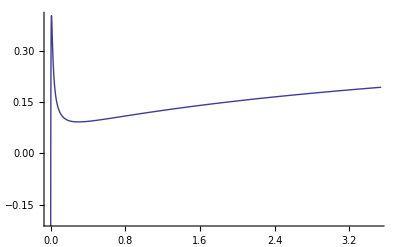

```mathematica
xm=0;
xM=3.5;
ym=-0.2;
yM=0.4;
gr3LP=ListPlot[dataLP,Joined-> True,PlotRange-> {{xm,xM},{ym,yM}}]
```

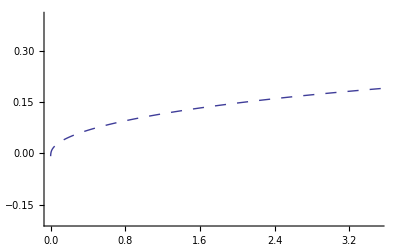

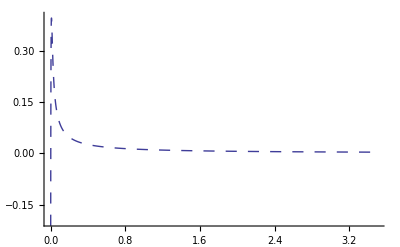

```mathematica
gr4E=ListPlot[dataLPE,Joined->True,PlotStyle->Dashing[{0.02,0.02}],PlotRange->{{xm,xM},{ym,yM}}]
gr4I=ListPlot[dataLPI,Joined->True,PlotStyle->Dashing[{0.02,0.02}],PlotRange->{{xm,xM},{ym,yM}}]
```

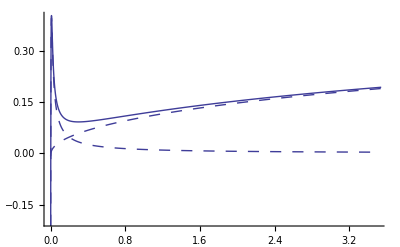

```mathematica
Show[gr3LP,gr4E,gr4I,PlotRange-> {{xm,xM},{ym,yM}}]
```

#### E vs x and range R

```mathematica
Clear[dxELP,ExLP, xELP]
```

```mathematica
dEdxELP=Interpolation[dataLP];
```

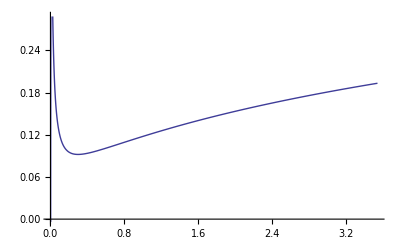

```mathematica
Plot[dEdxELP[e],{e,emin,emax}]
```

```mathematica
E0=emax;
dxELP[E_] :=1/dEdxELP[E]
xELP[E_]   := NIntegrate[1/dEdxELP[Ep],{Ep,E,E0},PrecisionGoal->Automatic]
```

```mathematica
FindRoot[dEdxELP[EE]==0,{EE,0.0.01}];
EzeroLPa=EE /. %
```

InterpolatingFunction::dmval: Input value {0.`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0008217078475221984`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

0.00259111

```mathematica
FindRoot[dEdxELP[EE]==0,{EE, EzeroLPa}];
EzeroLP=EE /. %
```

0.00259111

```mathematica
dEdxELP[EzeroLP]
```

-8.29584×10^-18

```mathematica
eth=1.04*T/1000
dEdxELP[eth]
xELP[eth]
```

0.00312

0.087541

25.6365

```mathematica
NN=1000;
E1=EzeroLP+eps;
E1=eth;
dE=(E0-E1)/NN;
dataExLP=Table[{xELP[E],E},{E,E1,emax,dE}];
```

```mathematica
xy1=dataExLP[[2]]
xy2=dataExLP[[1]]
dxy=xy2-xy1
m=dxy[[2]]/dxy[[1]]
b=xy1[[2]]-m*xy1[[1]]
xRLP=-b/m
```

{25.6208,0.00665688}

{25.6365,0.00312}

{0.0157153,-0.00353688}

-0.225059

5.77285

25.6504

```mathematica
dataExLP=Prepend[dataExLP,{xRLP,0}]
```

{{25.6504,0},{25.6365,0.00312},{25.6208,0.00665688},{25.6118,0.0101938},{25.6028,0.0137306},{25.5932,0.0172675},{25.5827,0.0208044},{25.5711,0.0243413},{25.5584,0.0278782},{25.5446,0.031415},{25.5297,0.0349519},{25.5137,0.0384888},{25.4967,0.0420257},{25.4786,0.0455626},{25.4596,0.0490994},{25.4396,0.0526363},{25.4188,0.0561732},{25.3971,0.0597101},{25.3745,0.063247},{25.3512,0.0667838},{25.3272,0.0703207},{25.3024,0.0738576},{25.2769,0.0773945},{25.2507,0.0809314},{25.224,0.0844682},{25.1966,0.0880051},{25.1687,0.091542},{25.1402,0.0950789},{25.1111,0.0986158},{25.0816,0.102153},{25.0516,0.10569},{25.0211,0.109226},{24.9902,0.112763},{24.9589,0.1163},{24.9272,0.119837},{24.8951,0.123374},{24.8626,0.126911},{24.8298,0.130448},{24.7967,0.133985},{24.7633,0.137521},{24.7295,0.141058},{24.6955,0.144595},{24.6612,0.148132},{24.6266,0.151669},{24.5918,0.155206},{24.5567,0.158743},{24.5215,0.16228},{24.486,0.165816},{24.4503,0.169353},{24.4144,0.17289},{24.3784,0.176427},{24.3421,0.179964},{24.3057,0.183501},{24.2692,0.187038},{24.2325,0.190575},{24.1957,0.194112},{24.1587,0.197648},{24.1216,0.201185},{24.0845,0.204722},{24.0471,0.208259},{24.0097,0.211796},{23.9722,0.215333},{23.9347,0.21887},{23.897,0.222407},{23.8592,0.225943},{23.8214,0.22948},{23.7835,0.233017},{23.7455,0.236554},{23.7075,0.240091},{23.6695,0.243628},{23.6313,0.247165},{23.5932,0.250702},{23.555,0.254238},{23.5167,0.257775},{23.4784,0.261312},{23.4401,0.264849},{23.4018,0.268386},{23.3634,0.271923},{23.3251,0.27546},{23.2867,0.278997},{23.2483,0.282534},{23.2098,0.28607},{23.1714,0.289607},{23.133,0.293144},{23.0945,0.296681},{23.0561,0.300218},{23.0177,0.303755},{22.9792,0.307292},{22.9408,0.310829},{22.9024,0.314365},{22.8639,0.317902},{22.8255,0.321439},{22.7872,0.324976},{22.7488,0.328513},{22.7104,0.33205},{22.6721,0.335587},{22.6338,0.339124},{22.5955,0.34266},{22.5572,0.346197},{22.5189,0.349734},{22.4807,0.353271},{22.4425,0.356808},{22.4043,0.360345},{22.3662,0.363882},{22.328,0.367419},{22.29,0.370956},{22.2519,0.374492},{22.2139,0.378029},{22.1759,0.381566},{22.1379,0.385103},{22.1,0.38864},{22.0621,0.392177},{22.0243,0.395714},{21.9865,0.399251},{21.9487,0.402787},{21.911,0.406324},{21.8733,0.409861},{21.8356,0.413398},{21.798,0.416935},{21.7605,0.420472},{21.723,0.424009},{21.6855,0.427546},{21.648,0.431082},{21.6106,0.434619},{21.5733,0.438156},{21.536,0.441693},{21.4987,0.44523},{21.4615,0.448767},{21.4243,0.452304},{21.3872,0.455841},{21.3502,0.459378},{21.3131,0.462914},{21.2761,0.466451},{21.2392,0.469988},{21.2023,0.473525},{21.1655,0.477062},{21.1287,0.480599},{21.092,0.484136},{21.0553,0.487673},{21.0186,0.491209},{20.982,0.494746},{20.9455,0.498283},{20.909,0.50182},{20.8725,0.505357},{20.8362,0.508894},{20.7998,0.512431},{20.7635,0.515968},{20.7273,0.519504},{20.6911,0.523041},{20.6549,0.526578},{20.6188,0.530115},{20.5828,0.533652},{20.5468,0.537189},{20.5108,0.540726},{20.475,0.544263},{20.4391,0.5478},{20.4033,0.551336},{20.3676,0.554873},{20.3319,0.55841},{20.2962,0.561947},{20.2607,0.565484},{20.2251,0.569021},{20.1896,0.572558},{20.1542,0.576095},{20.1188,0.579631},{20.0835,0.583168},{20.0482,0.586705},{20.013,0.590242},{19.9778,0.593779},{19.9426,0.597316},{19.9076,0.600853},{19.8725,0.60439},{19.8375,0.607926},{19.8026,0.611463},{19.7677,0.615},{19.7329,0.618537},{19.6981,0.622074},{19.6634,0.625611},{19.6287,0.629148},{19.5941,0.632685},{19.5595,0.636222},{19.525,0.639758},{19.4905,0.643295},{19.456,0.646832},{19.4217,0.650369},{19.3873,0.653906},{19.353,0.657443},{19.3188,0.66098},{19.2846,0.664517},{19.2505,0.668053},{19.2164,0.67159},{19.1824,0.675127},{19.1484,0.678664},{19.1144,0.682201},{19.0805,0.685738},{19.0467,0.689275},{19.0129,0.692812},{18.9792,0.696348},{18.9455,0.699885},{18.9118,0.703422},{18.8782,0.706959},{18.8447,0.710496},{18.8111,0.714033},{18.7777,0.71757},{18.7443,0.721107},{18.7109,0.724644},{18.6776,0.72818},{18.6443,0.731717},{18.6111,0.735254},{18.5779,0.738791},{18.5448,0.742328},{18.5117,0.745865},{18.4787,0.749402},{18.4457,0.752939},{18.4127,0.756475},{18.3798,0.760012},{18.347,0.763549},{18.3141,0.767086},{18.2814,0.770623},{18.2487,0.77416},{18.216,0.777697},{18.1834,0.781234},{18.1508,0.78477},{18.1182,0.788307},{18.0858,0.791844},{18.0533,0.795381},{18.0209,0.798918},{17.9885,0.802455},{17.9562,0.805992},{17.924,0.809529},{17.8917,0.813066},{17.8595,0.816602},{17.8274,0.820139},{17.7953,0.823676},{17.7633,0.827213},{17.7312,0.83075},{17.6993,0.834287},{17.6674,0.837824},{17.6355,0.841361},{17.6036,0.844897},{17.5718,0.848434},{17.5401,0.851971},{17.5084,0.855508},{17.4767,0.859045},{17.4451,0.862582},{17.4135,0.866119},{17.382,0.869656},{17.3505,0.873192},{17.319,0.876729},{17.2876,0.880266},{17.2562,0.883803},{17.2249,0.88734},{17.1936,0.890877},{17.1623,0.894414},{17.1311,0.897951},{17.0999,0.901488},{17.0688,0.905024},{17.0377,0.908561},{17.0067,0.912098},{16.9757,0.915635},{16.9447,0.919172},{16.9138,0.922709},{16.8829,0.926246},{16.852,0.929783},{16.8212,0.933319},{16.7904,0.936856},{16.7597,0.940393},{16.729,0.94393},{16.6983,0.947467},{16.6677,0.951004},{16.6372,0.954541},{16.6066,0.958078},{16.5761,0.961614},{16.5456,0.965151},{16.5152,0.968688},{16.4848,0.972225},{16.4545,0.975762},{16.4242,0.979299},{16.3939,0.982836},{16.3637,0.986373},{16.3335,0.98991},{16.3033,0.993446},{16.2732,0.996983},{16.2431,1.00052},{16.213,1.00406},{16.183,1.00759},{16.1531,1.01113},{16.1231,1.01467},{16.0932,1.0182},{16.0633,1.02174},{16.0335,1.02528},{16.0037,1.02882},{15.974,1.03235},{15.9442,1.03589},{15.9145,1.03943},{15.8849,1.04296},{15.8553,1.0465},{15.8257,1.05004},{15.7962,1.05357},{15.7666,1.05711},{15.7372,1.06065},{15.7077,1.06418},{15.6783,1.06772},{15.649,1.07126},{15.6196,1.07479},{15.5903,1.07833},{15.561,1.08187},{15.5318,1.08541},{15.5026,1.08894},{15.4734,1.09248},{15.4443,1.09602},{15.4152,1.09955},{15.3862,1.10309},{15.3571,1.10663},{15.3281,1.11016},{15.2992,1.1137},{15.2702,1.11724},{15.2413,1.12077},{15.2125,1.12431},{15.1836,1.12785},{15.1548,1.13138},{15.1261,1.13492},{15.0973,1.13846},{15.0686,1.142},{15.04,1.14553},{15.0113,1.14907},{14.9827,1.15261},{14.9542,1.15614},{14.9256,1.15968},{14.8971,1.16322},{14.8686,1.16675},{14.8402,1.17029},{14.8118,1.17383},{14.7834,1.17736},{14.7551,1.1809},{14.7267,1.18444},{14.6984,1.18797},{14.6702,1.19151},{14.642,1.19505},{14.6138,1.19859},{14.5856,1.20212},{14.5575,1.20566},{14.5294,1.2092},{14.5013,1.21273},{14.4733,1.21627},{14.4452,1.21981},{14.4173,1.22334},{14.3893,1.22688},{14.3614,1.23042},{14.3335,1.23395},{14.3056,1.23749},{14.2778,1.24103},{14.25,1.24456},{14.2222,1.2481},{14.1945,1.25164},{14.1668,1.25518},{14.1391,1.25871},{14.1114,1.26225},{14.0838,1.26579},{14.0562,1.26932},{14.0286,1.27286},{14.0011,1.2764},{13.9736,1.27993},{13.9461,1.28347},{13.9187,1.28701},{13.8912,1.29054},{13.8638,1.29408},{13.8365,1.29762},{13.8091,1.30115},{13.7818,1.30469},{13.7545,1.30823},{13.7273,1.31177},{13.7001,1.3153},{13.6729,1.31884},{13.6457,1.32238},{13.6185,1.32591},{13.5914,1.32945},{13.5643,1.33299},{13.5373,1.33652},{13.5102,1.34006},{13.4832,1.3436},{13.4562,1.34713},{13.4293,1.35067},{13.4024,1.35421},{13.3755,1.35775},{13.3486,1.36128},{13.3217,1.36482},{13.2949,1.36836},{13.2681,1.37189},{13.2414,1.37543},{13.2146,1.37897},{13.1879,1.3825},{13.1612,1.38604},{13.1346,1.38958},{13.1079,1.39311},{13.0813,1.39665},{13.0547,1.40019},{13.0282,1.40372},{13.0016,1.40726},{12.9751,1.4108},{12.9486,1.41434},{12.9222,1.41787},{12.8958,1.42141},{12.8694,1.42495},{12.843,1.42848},{12.8166,1.43202},{12.7903,1.43556},{12.764,1.43909},{12.7377,1.44263},{12.7115,1.44617},{12.6852,1.4497},{12.659,1.45324},{12.6328,1.45678},{12.6067,1.46031},{12.5806,1.46385},{12.5545,1.46739},{12.5284,1.47093},{12.5023,1.47446},{12.4763,1.478},{12.4503,1.48154},{12.4243,1.48507},{12.3983,1.48861},{12.3724,1.49215},{12.3465,1.49568},{12.3206,1.49922},{12.2947,1.50276},{12.2689,1.50629},{12.2431,1.50983},{12.2173,1.51337},{12.1915,1.5169},{12.1658,1.52044},{12.14,1.52398},{12.1143,1.52752},{12.0887,1.53105},{12.063,1.53459},{12.0374,1.53813},{12.0118,1.54166},{11.9862,1.5452},{11.9606,1.54874},{11.9351,1.55227},{11.9096,1.55581},{11.8841,1.55935},{11.8586,1.56288},{11.8332,1.56642},{11.8077,1.56996},{11.7823,1.57349},{11.757,1.57703},{11.7316,1.58057},{11.7063,1.58411},{11.6809,1.58764},{11.6557,1.59118},{11.6304,1.59472},{11.6051,1.59825},{11.5799,1.60179},{11.5547,1.60533},{11.5295,1.60886},{11.5044,1.6124},{11.4792,1.61594},{11.4541,1.61947},{11.429,1.62301},{11.404,1.62655},{11.3789,1.63008},{11.3539,1.63362},{11.3289,1.63716},{11.3039,1.6407},{11.2789,1.64423},{11.254,1.64777},{11.2291,1.65131},{11.2042,1.65484},{11.1793,1.65838},{11.1544,1.66192},{11.1296,1.66545},{11.1048,1.66899},{11.08,1.67253},{11.0552,1.67606},{11.0304,1.6796},{11.0057,1.68314},{10.981,1.68667},{10.9563,1.69021},{10.9316,1.69375},{10.907,1.69729},{10.8823,1.70082},{10.8577,1.70436},{10.8331,1.7079},{10.8086,1.71143},{10.784,1.71497},{10.7595,1.71851},{10.735,1.72204},{10.7105,1.72558},{10.686,1.72912},{10.6616,1.73265},{10.6371,1.73619},{10.6127,1.73973},{10.5883,1.74326},{10.564,1.7468},{10.5396,1.75034},{10.5153,1.75388},{10.491,1.75741},{10.4667,1.76095},{10.4424,1.76449},{10.4182,1.76802},{10.3939,1.77156},{10.3697,1.7751},{10.3455,1.77863},{10.3213,1.78217},{10.2972,1.78571},{10.273,1.78924},{10.2489,1.79278},{10.2248,1.79632},{10.2008,1.79986},{10.1767,1.80339},{10.1526,1.80693},{10.1286,1.81047},{10.1046,1.814},{10.0806,1.81754},{10.0567,1.82108},{10.0327,1.82461},{10.0088,1.82815},{9.98487,1.83169},{9.96098,1.83522},{9.93711,1.83876},{9.91325,1.8423},{9.88941,1.84583},{9.86559,1.84937},{9.84179,1.85291},{9.81801,1.85645},{9.79424,1.85998},{9.7705,1.86352},{9.74677,1.86706},{9.72306,1.87059},{9.69937,1.87413},{9.67569,1.87767},{9.65204,1.8812},{9.6284,1.88474},{9.60478,1.88828},{9.58117,1.89181},{9.55759,1.89535},{9.53402,1.89889},{9.51047,1.90242},{9.48694,1.90596},{9.46342,1.9095},{9.43993,1.91304},{9.41645,1.91657},{9.39298,1.92011},{9.36954,1.92365},{9.34611,1.92718},{9.3227,1.93072},{9.29931,1.93426},{9.27593,1.93779},{9.25258,1.94133},{9.22923,1.94487},{9.20591,1.9484},{9.1826,1.95194},{9.15931,1.95548},{9.13604,1.95901},{9.11278,1.96255},{9.08954,1.96609},{9.06632,1.96963},{9.04312,1.97316},{9.01993,1.9767},{8.99676,1.98024},{8.9736,1.98377},{8.95046,1.98731},{8.92734,1.99085},{8.90424,1.99438},{8.88115,1.99792},{8.85808,2.00146},{8.83502,2.00499},{8.81198,2.00853},{8.78896,2.01207},{8.76595,2.0156},{8.74296,2.01914},{8.71999,2.02268},{8.69703,2.02622},{8.67409,2.02975},{8.65116,2.03329},{8.62825,2.03683},{8.60536,2.04036},{8.58248,2.0439},{8.55962,2.04744},{8.53678,2.05097},{8.51395,2.05451},{8.49114,2.05805},{8.46834,2.06158},{8.44556,2.06512},{8.42279,2.06866},{8.40004,2.07219},{8.37731,2.07573},{8.35459,2.07927},{8.33189,2.08281},{8.3092,2.08634},{8.28653,2.08988},{8.26387,2.09342},{8.24123,2.09695},{8.21861,2.10049},{8.196,2.10403},{8.1734,2.10756},{8.15082,2.1111},{8.12826,2.11464},{8.10571,2.11817},{8.08318,2.12171},{8.06066,2.12525},{8.03816,2.12878},{8.01567,2.13232},{7.9932,2.13586},{7.97074,2.1394},{7.9483,2.14293},{7.92587,2.14647},{7.90346,2.15001},{7.88107,2.15354},{7.85868,2.15708},{7.83632,2.16062},{7.81396,2.16415},{7.79163,2.16769},{7.7693,2.17123},{7.747,2.17476},{7.7247,2.1783},{7.70242,2.18184},{7.68016,2.18537},{7.65791,2.18891},{7.63568,2.19245},{7.61346,2.19599},{7.59125,2.19952},{7.56906,2.20306},{7.54688,2.2066},{7.52472,2.21013},{7.50257,2.21367},{7.48044,2.21721},{7.45832,2.22074},{7.43622,2.22428},{7.41413,2.22782},{7.39205,2.23135},{7.36999,2.23489},{7.34794,2.23843},{7.32591,2.24197},{7.30389,2.2455},{7.28188,2.24904},{7.25989,2.25258},{7.23791,2.25611},{7.21595,2.25965},{7.194,2.26319},{7.17207,2.26672},{7.15015,2.27026},{7.12824,2.2738},{7.10635,2.27733},{7.08447,2.28087},{7.0626,2.28441},{7.04075,2.28794},{7.01891,2.29148},{6.99708,2.29502},{6.97527,2.29856},{6.95348,2.30209},{6.93169,2.30563},{6.90992,2.30917},{6.88817,2.3127},{6.86642,2.31624},{6.84469,2.31978},{6.82298,2.32331},{6.80127,2.32685},{6.77958,2.33039},{6.75791,2.33392},{6.73625,2.33746},{6.7146,2.341},{6.69296,2.34453},{6.67134,2.34807},{6.64973,2.35161},{6.62813,2.35515},{6.60655,2.35868},{6.58498,2.36222},{6.56343,2.36576},{6.54188,2.36929},{6.52035,2.37283},{6.49883,2.37637},{6.47733,2.3799},{6.45584,2.38344},{6.43436,2.38698},{6.4129,2.39051},{6.39144,2.39405},{6.37,2.39759},{6.34858,2.40112},{6.32716,2.40466},{6.30576,2.4082},{6.28437,2.41174},{6.263,2.41527},{6.24164,2.41881},{6.22029,2.42235},{6.19895,2.42588},{6.17763,2.42942},{6.15631,2.43296},{6.13501,2.43649},{6.11373,2.44003},{6.09245,2.44357},{6.07119,2.4471},{6.04994,2.45064},{6.02871,2.45418},{6.00748,2.45771},{5.98627,2.46125},{5.96507,2.46479},{5.94388,2.46833},{5.92271,2.47186},{5.90155,2.4754},{5.8804,2.47894},{5.85926,2.48247},{5.83814,2.48601},{5.81702,2.48955},{5.79592,2.49308},{5.77483,2.49662},{5.75376,2.50016},{5.73269,2.50369},{5.71164,2.50723},{5.6906,2.51077},{5.66957,2.5143},{5.64856,2.51784},{5.62755,2.52138},{5.60656,2.52492},{5.58558,2.52845},{5.56461,2.53199},{5.54366,2.53553},{5.52271,2.53906},{5.50178,2.5426},{5.48086,2.54614},{5.45995,2.54967},{5.43905,2.55321},{5.41817,2.55675},{5.39729,2.56028},{5.37643,2.56382},{5.35558,2.56736},{5.33475,2.57089},{5.31392,2.57443},{5.2931,2.57797},{5.2723,2.58151},{5.25151,2.58504},{5.23073,2.58858},{5.20996,2.59212},{5.1892,2.59565},{5.16846,2.59919},{5.14772,2.60273},{5.127,2.60626},{5.10629,2.6098},{5.08559,2.61334},{5.0649,2.61687},{5.04423,2.62041},{5.02356,2.62395},{5.00291,2.62748},{4.98226,2.63102},{4.96163,2.63456},{4.94101,2.6381},{4.9204,2.64163},{4.89981,2.64517},{4.87922,2.64871},{4.85864,2.65224},{4.83808,2.65578},{4.81753,2.65932},{4.79698,2.66285},{4.77645,2.66639},{4.75593,2.66993},{4.73542,2.67346},{4.71493,2.677},{4.69444,2.68054},{4.67396,2.68408},{4.6535,2.68761},{4.63305,2.69115},{4.6126,2.69469},{4.59217,2.69822},{4.57175,2.70176},{4.55134,2.7053},{4.53094,2.70883},{4.51055,2.71237},{4.49018,2.71591},{4.46981,2.71944},{4.44945,2.72298},{4.42911,2.72652},{4.40877,2.73005},{4.38845,2.73359},{4.36814,2.73713},{4.34783,2.74067},{4.32754,2.7442},{4.30726,2.74774},{4.28699,2.75128},{4.26673,2.75481},{4.24648,2.75835},{4.22624,2.76189},{4.20601,2.76542},{4.1858,2.76896},{4.16559,2.7725},{4.14539,2.77603},{4.12521,2.77957},{4.10503,2.78311},{4.08486,2.78664},{4.06471,2.79018},{4.04456,2.79372},{4.02443,2.79726},{4.00431,2.80079},{3.98419,2.80433},{3.96409,2.80787},{3.944,2.8114},{3.92391,2.81494},{3.90384,2.81848},{3.88378,2.82201},{3.86373,2.82555},{3.84368,2.82909},{3.82365,2.83262},{3.80363,2.83616},{3.78362,2.8397},{3.76362,2.84323},{3.74363,2.84677},{3.72365,2.85031},{3.70367,2.85385},{3.68371,2.85738},{3.66376,2.86092},{3.64382,2.86446},{3.62389,2.86799},{3.60397,2.87153},{3.58406,2.87507},{3.56416,2.8786},{3.54427,2.88214},{3.52439,2.88568},{3.50451,2.88921},{3.48465,2.89275},{3.4648,2.89629},{3.44496,2.89982},{3.42513,2.90336},{3.4053,2.9069},{3.38549,2.91044},{3.36569,2.91397},{3.3459,2.91751},{3.32611,2.92105},{3.30634,2.92458},{3.28658,2.92812},{3.26682,2.93166},{3.24708,2.93519},{3.22734,2.93873},{3.20762,2.94227},{3.1879,2.9458},{3.1682,2.94934},{3.1485,2.95288},{3.12881,2.95641},{3.10914,2.95995},{3.08947,2.96349},{3.06981,2.96703},{3.05016,2.97056},{3.03052,2.9741},{3.01089,2.97764},{2.99127,2.98117},{2.97166,2.98471},{2.95206,2.98825},{2.93247,2.99178},{2.91289,2.99532},{2.89331,2.99886},{2.87375,3.00239},{2.85419,3.00593},{2.83465,3.00947},{2.81511,3.013},{2.79559,3.01654},{2.77607,3.02008},{2.75656,3.02362},{2.73706,3.02715},{2.71757,3.03069},{2.69809,3.03423},{2.67862,3.03776},{2.65916,3.0413},{2.6397,3.04484},{2.62026,3.04837},{2.60083,3.05191},{2.5814,3.05545},{2.56198,3.05898},{2.54258,3.06252},{2.52318,3.06606},{2.50379,3.06959},{2.48441,3.07313},{2.46504,3.07667},{2.44567,3.08021},{2.42632,3.08374},{2.40698,3.08728},{2.38764,3.09082},{2.36831,3.09435},{2.349,3.09789},{2.32969,3.10143},{2.31039,3.10496},{2.2911,3.1085},{2.27182,3.11204},{2.25254,3.11557},{2.23328,3.11911},{2.21402,3.12265},{2.19478,3.12619},{2.17554,3.12972},{2.15631,3.13326},{2.13709,3.1368},{2.11788,3.14033},{2.09868,3.14387},{2.07948,3.14741},{2.0603,3.15094},{2.04112,3.15448},{2.02195,3.15802},{2.00279,3.16155},{1.98364,3.16509},{1.9645,3.16863},{1.94537,3.17216},{1.92624,3.1757},{1.90713,3.17924},{1.88802,3.18278},{1.86892,3.18631},{1.84983,3.18985},{1.83075,3.19339},{1.81167,3.19692},{1.79261,3.20046},{1.77355,3.204},{1.7545,3.20753},{1.73546,3.21107},{1.71643,3.21461},{1.69741,3.21814},{1.6784,3.22168},{1.65939,3.22522},{1.64039,3.22875},{1.6214,3.23229},{1.60242,3.23583},{1.58345,3.23937},{1.56449,3.2429},{1.54553,3.24644},{1.52659,3.24998},{1.50765,3.25351},{1.48872,3.25705},{1.46979,3.26059},{1.45088,3.26412},{1.43197,3.26766},{1.41308,3.2712},{1.39419,3.27473},{1.37531,3.27827},{1.35643,3.28181},{1.33757,3.28534},{1.31871,3.28888},{1.29986,3.29242},{1.28102,3.29596},{1.26219,3.29949},{1.24337,3.30303},{1.22455,3.30657},{1.20574,3.3101},{1.18694,3.31364},{1.16815,3.31718},{1.14937,3.32071},{1.13059,3.32425},{1.11182,3.32779},{1.09306,3.33132},{1.07431,3.33486},{1.05557,3.3384},{1.03683,3.34193},{1.01811,3.34547},{0.999387,3.34901},{0.980675,3.35255},{0.961971,3.35608},{0.943276,3.35962},{0.924588,3.36316},{0.905907,3.36669},{0.887235,3.37023},{0.868571,3.37377},{0.849914,3.3773},{0.831266,3.38084},{0.812625,3.38438},{0.793992,3.38791},{0.775367,3.39145},{0.75675,3.39499},{0.73814,3.39852},{0.719538,3.40206},{0.700944,3.4056},{0.682358,3.40914},{0.663779,3.41267},{0.645208,3.41621},{0.626645,3.41975},{0.60809,3.42328},{0.589542,3.42682},{0.571002,3.43036},{0.552469,3.43389},{0.533944,3.43743},{0.515427,3.44097},{0.496918,3.4445},{0.478416,3.44804},{0.459921,3.45158},{0.441435,3.45511},{0.422955,3.45865},{0.404484,3.46219},{0.38602,3.46573},{0.367563,3.46926},{0.349114,3.4728},{0.330673,3.47634},{0.312239,3.47987},{0.293813,3.48341},{0.275394,3.48695},{0.256982,3.49048},{0.238578,3.49402},{0.220182,3.49756},{0.201792,3.50109},{0.183411,3.50463},{0.165036,3.50817},{0.14667,3.5117},{0.12831,3.51524},{0.109958,3.51878},{0.0916133,3.52232},{0.073276,3.52585},{0.054946,3.52939},{0.0366233,3.53293},{0.018308,3.53646},{0,3.54}}

```mathematica
ExLP=Interpolation[dataExLP];
```

```mathematica
ExLP[xRLP]
```

0.

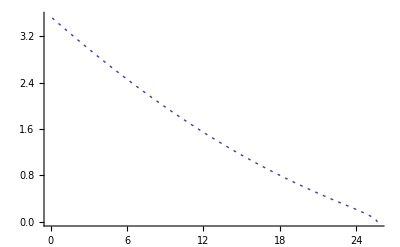

```mathematica
grExLP=ListPlot[dataExLP,Joined->True,PlotStyle->Dashing[{0.005,0.01}]]
```

#### dE/dx vs E: dEdxELP

```mathematica
dEdxEeLP =Interpolation[dataLPE];
dEdxEiLP =Interpolation[dataLPI];
```

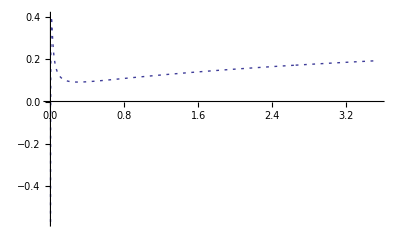

```mathematica
grdEdxELP=Plot[dEdxELP[e],{e,emin,emax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->10000,PlotRange->All]
```

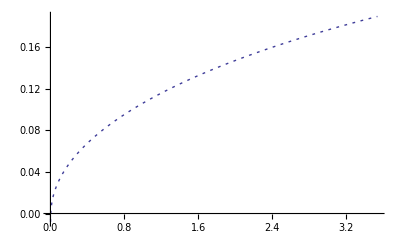

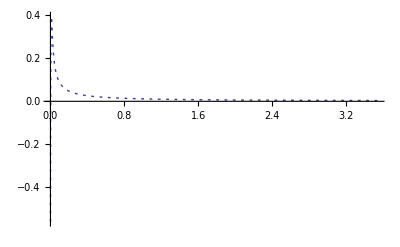

```mathematica
grdEdxEeLP=Plot[dEdxEeLP[e],{e,emin,emax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->1000,PlotRange->All]
grdEdxEiLP=Plot[dEdxEiLP[e],{e,emin,emax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->1000,PlotRange->All]
```

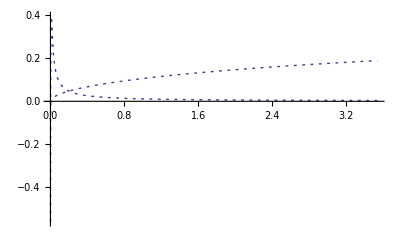

```mathematica
grdEdxEeiLP=Show[grdEdxEeLP,grdEdxEiLP]
```

#### dE/dx vs x: dEdxx LP

```mathematica
dEdxxLP[x_] := dEdxELP[ExLP[x]]
dEdxxeLP[x_] := dEdxEeLP[ExLP[x]]
dEdxxiLP[x_] := dEdxEiLP[ExLP[x]]
```

```mathematica
x0=FindRoot[dEdxxLP[xRLP-x0]==0,{x0,0.01}][[1,2]]
```

0.0110745

```mathematica
dEdxxLP[xRLP]
dEdxxLP[xRLP- x0]
```

InterpolatingFunction::dmval: Input value {0.`} lies outside the range of data in the interpolating function. Extrapolation will be used.

-1.99073

-1.59271×10^-14

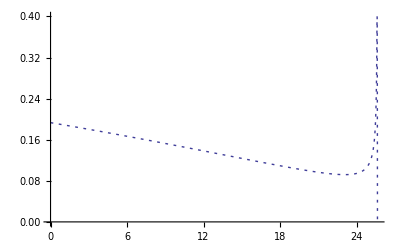

```mathematica
grdEdxxLP=Plot[dEdxxLP[x],{x,0,xRLP-x0},PlotStyle->Dashing[{0.005,0.01}],
PlotPoints->1000,PlotPoints->All,PlotRange->{0,0.4}]
```

```mathematica
xRLP
xRLPmax=xRLP-x0
```

25.6504

25.6393

```mathematica
xRLPmax
```

25.6393

```mathematica
x0=2.5;
NIntegrate[dEdxxLP[x],{x,0,x0},MaxRecursion->10]
NIntegrate[dEdxxLP[x],{x,x0,xRLPmax},MaxRecursion->100]
% + %%
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

0.469714

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

3.06758

3.5373

```mathematica
100*(%-E0)/E0
```

-0.0764047

```mathematica
100*eth/E0
```

0.0881356

partitioned among plasma components

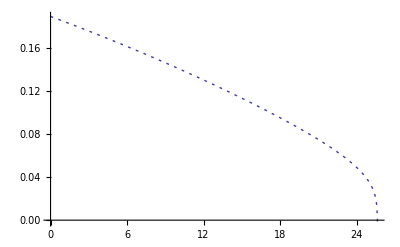

```mathematica
grdEdxxeLP=Plot[dEdxxeLP[x] ,{x,0,xRLPmax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->1000,PlotPoints->All]
```

```mathematica
Ee=NIntegrate[dEdxxeLP[x],{x,0,xRLPmax}]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

3.11794

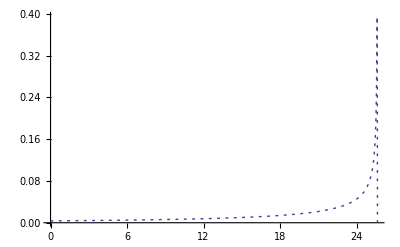

```mathematica
grdEdxxiLP=Plot[dEdxxiLP[x] ,{x,0,xRLPmax},PlotStyle->Dashing[{0.005,0.01}],PlotPoints->1000,PlotRange->All]
```

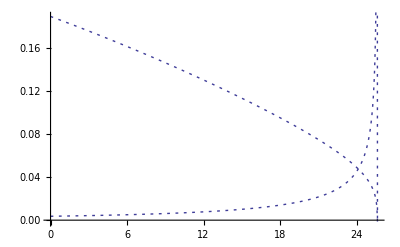

```mathematica
grdEdxxeiLP=Show[grdEdxxeLP,grdEdxxiLP]
```

```mathematica
xRLPmax
```

25.6393

```mathematica
x1=2.5;
NIntegrate[dEdxxiLP[x],{x,0,x1},MaxRecursion->10]
NIntegrate[dEdxxiLP[x],{x,x1,xRLPmax},MaxRecursion->10]
Ei=% + %%
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

0.00966305

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in x near {x} = {25.62423747906763472903524103685413138009607791900634765625`65.954589770191}. NIntegrate obtained 0.409693 and 3.41786×10^-6 for the integral and error estimates.

0.409693

0.419356

```mathematica
{Ee,Ei,Ee+Ei,E0}
```

{3.11794,0.419356,3.5373,3.54}

```mathematica
100*(E0-Ee-Ei)/E0
```

0.0762666

### BPS

#### data The dE/dx between fortran and mathematica agree. See data and fig below.

```mathematica
emin=0.001;
emax=3.54;
```

```mathematica
E1=emin;
E2=0.03;
NN=600;
dE=(E2-E1)/NN;
dataBPSa=Table[{EE,dedxi[VP[EE]]},{EE,E1,E2,dE}];

E1=E2+dE;
E2=0.25;
NN=100;
dE=(E2-E1)/NN;
dataBPSb=Table[{EE,dedxi[VP[EE]]},{EE,E1,E2,dE}];

E1=E2+dE;
E2=emax;
NN=100;
dE=(E2-E1)/NN;
dataBPSc=Table[{EE,dedxi[VP[EE]]},{EE,E1,E2,dE}];
```

```mathematica
dataBPSEI=Join[dataBPSa,dataBPSb,dataBPSc]
```

{{0.001,{-0.0097492,-0.318483,-0.347746}},{0.00104833,{-0.0094054,-0.304527,-0.331119}},{0.00109667,{-0.00908173,-0.291397,-0.315495}},{0.001145,{-0.00877608,-0.279011,-0.300773}},{0.00119333,{-0.00848666,-0.267296,-0.286867}},{0.00124167,{-0.00821191,-0.256191,-0.273704}},{0.00129,{-0.00795046,-0.24564,-0.261217}},{0.00133833,{-0.00770114,-0.235596,-0.249349}},{0.00138667,{-0.0074629,-0.226019,-0.238052}},{0.001435,{-0.00723483,-0.21687,-0.227279}},{0.00148333,{-0.00701611,-0.208117,-0.216991}},{0.00153167,{-0.00680603,-0.199732,-0.207154}},{0.00158,{-0.00660393,-0.191687,-0.197735}},{0.00162833,{-0.00640923,-0.183959,-0.188706}},{0.00167667,{-0.00622142,-0.176527,-0.180041}},{0.001725,{-0.00604002,-0.169372,-0.171717}},{0.00177333,{-0.0058646,-0.162477,-0.163713}},{0.00182167,{-0.00569478,-0.155825,-0.15601}},{0.00187,{-0.0055302,-0.149403,-0.148589}},{0.00191833,{-0.00537054,-0.143196,-0.141436}},{0.00196667,{-0.00521552,-0.137193,-0.134534}},{0.002015,{-0.00506485,-0.131383,-0.127871}},{0.00206333,{-0.0049183,-0.125756,-0.121434}},{0.00211167,{-0.00477562,-0.120301,-0.115211}},{0.00216,{-0.00463662,-0.115011,-0.109192}},{0.00220833,{-0.0045011,-0.109877,-0.103366}},{0.00225667,{-0.00436887,-0.104891,-0.0977251}},{0.002305,{-0.00423977,-0.100048,-0.0922595}},{0.00235333,{-0.00411365,-0.0953389,-0.0869617}},{0.00240167,{-0.00399035,-0.0907594,-0.0818241}},{0.00245,{-0.00386975,-0.0863033,-0.0768397}},{0.00249833,{-0.00375172,-0.0819653,-0.0720019}},{0.00254667,{-0.00363615,-0.0777404,-0.0673045}},{0.002595,{-0.00352291,-0.0736239,-0.0627418}},{0.00264333,{-0.00341191,-0.0696116,-0.0583083}},{0.00269167,{-0.00330306,-0.0656991,-0.0539989}},{0.00274,{-0.00319626,-0.0618828,-0.0498087}},{0.00278833,{-0.00309142,-0.0581588,-0.0457332}},{0.00283667,{-0.00298847,-0.0545238,-0.0417681}},{0.002885,{-0.00288733,-0.0509745,-0.0379093}},{0.00293333,{-0.00278793,-0.0475078,-0.0341528}},{0.00298167,{-0.0026902,-0.0441208,-0.0304952}},{0.00303,{-0.00259408,-0.0408107,-0.0269327}},{0.00307833,{-0.0024995,-0.0375748,-0.0234623}},{0.00312667,{-0.00240642,-0.0344108,-0.0200807}},{0.003175,{-0.00231477,-0.0313161,-0.016785}},{0.00322333,{-0.0022245,-0.0282887,-0.0135722}},{0.00327167,{-0.00213558,-0.0253262,-0.0104398}},{0.00332,{-0.00204794,-0.0224267,-0.00738507}},{0.00336833,{-0.00196155,-0.0195882,-0.00440559}},{0.00341667,{-0.00187636,-0.0168089,-0.001499}},{0.003465,{-0.00179234,-0.0140869,0.00133695}},{0.00351333,{-0.00170944,-0.0114207,0.00410441}},{0.00356167,{-0.00162764,-0.00880847,0.00680545}},{0.00361,{-0.00154689,-0.00624877,0.00944204}},{0.00365833,{-0.00146716,-0.00374009,0.0120161}},{0.00370667,{-0.00138843,-0.001281,0.0145294}},{0.003755,{-0.00131065,0.00112987,0.0169837}},{0.00380333,{-0.00123381,0.00349382,0.0193806}},{0.00385167,{-0.00115788,0.00581212,0.0217219}},{0.0039,{-0.00108282,0.00808596,0.024009}},{0.00394833,{-0.00100862,0.0103165,0.0262434}},{0.00399667,{-0.000935244,0.0125049,0.0284265}},{0.004045,{-0.000862677,0.0146522,0.0305597}},{0.00409333,{-0.000790894,0.0167595,0.0326444}},{0.00414167,{-0.000719874,0.0188276,0.0346818}},{0.00419,{-0.000649596,0.0208577,0.0366732}},{0.00423833,{-0.00058004,0.0228506,0.0386197}},{0.00428667,{-0.000511188,0.0248072,0.0405225}},{0.004335,{-0.000443022,0.0267284,0.0423827}},{0.00438333,{-0.000375524,0.0286149,0.0442014}},{0.00443167,{-0.000308677,0.0304677,0.0459795}},{0.00448,{-0.000242464,0.0322875,0.0477182}},{0.00452833,{-0.000176871,0.034075,0.0494183}},{0.00457667,{-0.000111882,0.0358309,0.0510809}},{0.004625,{-0.0000474834,0.037556,0.0527067}},{0.00467333,{0.0000163399,0.039251,0.0542967}},{0.00472167,{0.0000796009,0.0409164,0.0558518}},{0.00477,{0.000142313,0.042553,0.0573727}},{0.00481833,{0.000204488,0.0441613,0.0588602}},{0.00486667,{0.000266138,0.0457419,0.0603152}},{0.004915,{0.000327276,0.0472955,0.0617383}},{0.00496333,{0.000387913,0.0488226,0.0631303}},{0.00501167,{0.000448058,0.0503237,0.064492}},{0.00506,{0.000507724,0.0517993,0.0658239}},{0.00510833,{0.00056692,0.05325,0.0671268}},{0.00515667,{0.000625657,0.0546763,0.0684012}},{0.005205,{0.000683943,0.0560787,0.0696479}},{0.00525333,{0.000741788,0.0574575,0.0708674}},{0.00530167,{0.000799201,0.0588134,0.0720604}},{0.00535,{0.000856191,0.0601467,0.0732273}},{0.00539833,{0.000912766,0.0614578,0.0743689}},{0.00544667,{0.000968934,0.0627472,0.0754855}},{0.005495,{0.0010247,0.0640153,0.0765777}},{0.00554333,{0.00108008,0.0652626,0.0776461}},{0.00559167,{0.00113508,0.0664892,0.0786912}},{0.00564,{0.0011897,0.0676958,0.0797134}},{0.00568833,{0.00124395,0.0688826,0.0807133}},{0.00573667,{0.00129783,0.0700499,0.0816912}},{0.005785,{0.00135136,0.0711982,0.0826476}},{0.00583333,{0.00140454,0.0723278,0.0835831}},{0.00588167,{0.00145738,0.073439,0.0844979}},{0.00593,{0.00150988,0.0745321,0.0853926}},{0.00597833,{0.00156205,0.0756075,0.0862675}},{0.00602667,{0.00161389,0.0766655,0.0871231}},{0.006075,{0.00166542,0.0777063,0.0879597}},{0.00612333,{0.00171663,0.0787303,0.0887777}},{0.00617167,{0.00176752,0.0797377,0.0895774}},{0.00622,{0.00181812,0.0807288,0.0903594}},{0.00626833,{0.00186841,0.081704,0.0911238}},{0.00631667,{0.00191842,0.0826634,0.091871}},{0.006365,{0.00196813,0.0836074,0.0926014}},{0.00641333,{0.00201755,0.0845362,0.0933153}},{0.00646167,{0.0020667,0.08545,0.0940131}},{0.00651,{0.00211556,0.086349,0.0946949}},{0.00655833,{0.00216416,0.0872337,0.0953612}},{0.00660667,{0.00221249,0.088104,0.0960123}},{0.006655,{0.00226055,0.0889604,0.0966484}},{0.00670333,{0.00230835,0.089803,0.0972698}},{0.00675167,{0.0023559,0.090632,0.0978768}},{0.0068,{0.0024032,0.0914477,0.0984697}},{0.00684833,{0.00245024,0.0922502,0.0990488}},{0.00689667,{0.00249704,0.0930398,0.0996143}},{0.006945,{0.0025436,0.0938167,0.100166}},{0.00699333,{0.00258992,0.0945811,0.100705}},{0.00704167,{0.002636,0.0953331,0.101232}},{0.00709,{0.00268185,0.0960729,0.101745}},{0.00713833,{0.00272747,0.0968008,0.102246}},{0.00718667,{0.00277287,0.097517,0.102736}},{0.007235,{0.00281804,0.0982215,0.103213}},{0.00728333,{0.00286299,0.0989146,0.103678}},{0.00733167,{0.00290773,0.0995965,0.104132}},{0.00738,{0.00295225,0.100267,0.104575}},{0.00742833,{0.00299656,0.100927,0.105007}},{0.00747667,{0.00304066,0.101576,0.105428}},{0.007525,{0.00308455,0.102215,0.105838}},{0.00757333,{0.00312824,0.102843,0.106238}},{0.00762167,{0.00317173,0.103461,0.106627}},{0.00767,{0.00321502,0.104068,0.107007}},{0.00771833,{0.00325811,0.104666,0.107376}},{0.00776667,{0.003301,0.105254,0.107736}},{0.007815,{0.00334371,0.105832,0.108087}},{0.00786333,{0.00338622,0.106401,0.108427}},{0.00791167,{0.00342855,0.10696,0.108759}},{0.00796,{0.00347069,0.10751,0.109082}},{0.00800833,{0.00351265,0.10805,0.109396}},{0.00805667,{0.00355442,0.108582,0.109701}},{0.008105,{0.00359602,0.109105,0.109998}},{0.00815333,{0.00363743,0.109619,0.110286}},{0.00820167,{0.00367868,0.110124,0.110566}},{0.00825,{0.00371975,0.110621,0.110838}},{0.00829833,{0.00376064,0.11111,0.111102}},{0.00834667,{0.00380137,0.11159,0.111358}},{0.008395,{0.00384192,0.112062,0.111606}},{0.00844333,{0.00388231,0.112526,0.111847}},{0.00849167,{0.00392254,0.112982,0.112081}},{0.00854,{0.0039626,0.113431,0.112307}},{0.00858833,{0.0040025,0.113871,0.112526}},{0.00863667,{0.00404224,0.114304,0.112739}},{0.008685,{0.00408182,0.114729,0.112944}},{0.00873333,{0.00412124,0.115147,0.113142}},{0.00878167,{0.00416051,0.115558,0.113334}},{0.00883,{0.00419962,0.115962,0.11352}},{0.00887833,{0.00423858,0.116358,0.113699}},{0.00892667,{0.00427739,0.116747,0.113871}},{0.008975,{0.00431605,0.11713,0.114038}},{0.00902333,{0.00435456,0.117505,0.114198}},{0.00907167,{0.00439292,0.117874,0.114353}},{0.00912,{0.00443114,0.118237,0.114501}},{0.00916833,{0.00446921,0.118592,0.114644}},{0.00921667,{0.00450714,0.118942,0.114781}},{0.009265,{0.00454493,0.119285,0.114913}},{0.00931333,{0.00458257,0.119621,0.115039}},{0.00936167,{0.00462008,0.119951,0.11516}},{0.00941,{0.00465744,0.120276,0.115276}},{0.00945833,{0.00469467,0.120594,0.115386}},{0.00950667,{0.00473177,0.120906,0.115492}},{0.009555,{0.00476873,0.121213,0.115592}},{0.00960333,{0.00480555,0.121513,0.115688}},{0.00965167,{0.00484224,0.121808,0.115778}},{0.0097,{0.0048788,0.122097,0.115864}},{0.00974833,{0.00491523,0.122381,0.115946}},{0.00979667,{0.00495153,0.122659,0.116023}},{0.009845,{0.0049877,0.122932,0.116095}},{0.00989333,{0.00502374,0.123199,0.116163}},{0.00994167,{0.00505966,0.123461,0.116227}},{0.00999,{0.00509545,0.123718,0.116286}},{0.0100383,{0.00513111,0.12397,0.116341}},{0.0100867,{0.00516665,0.124216,0.116392}},{0.010135,{0.00520207,0.124458,0.116439}},{0.0101833,{0.00523737,0.124695,0.116483}},{0.0102317,{0.00527254,0.124926,0.116522}},{0.01028,{0.0053076,0.125153,0.116558}},{0.0103283,{0.00534254,0.125376,0.116589}},{0.0103767,{0.00537735,0.125593,0.116618}},{0.010425,{0.00541205,0.125806,0.116642}},{0.0104733,{0.00544664,0.126014,0.116663}},{0.0105217,{0.0054811,0.126218,0.116681}},{0.01057,{0.00551546,0.126417,0.116695}},{0.0106183,{0.00554969,0.126612,0.116706}},{0.0106667,{0.00558382,0.126803,0.116713}},{0.010715,{0.00561783,0.126989,0.116717}},{0.0107633,{0.00565173,0.127171,0.116718}},{0.0108117,{0.00568552,0.127349,0.116716}},{0.01086,{0.0057192,0.127523,0.116711}},{0.0109083,{0.00575277,0.127693,0.116703}},{0.0109567,{0.00578623,0.127858,0.116692}},{0.011005,{0.00581958,0.12802,0.116679}},{0.0110533,{0.00585282,0.128178,0.116662}},{0.0111017,{0.00588596,0.128332,0.116642}},{0.01115,{0.00591899,0.128482,0.11662}},{0.0111983,{0.00595192,0.128628,0.116595}},{0.0112467,{0.00598474,0.128771,0.116568}},{0.011295,{0.00601746,0.12891,0.116538}},{0.0113433,{0.00605007,0.129045,0.116505}},{0.0113917,{0.00608258,0.129177,0.11647}},{0.01144,{0.00611499,0.129305,0.116432}},{0.0114883,{0.0061473,0.12943,0.116392}},{0.0115367,{0.00617951,0.129551,0.11635}},{0.011585,{0.00621162,0.129669,0.116306}},{0.0116333,{0.00624362,0.129784,0.116259}},{0.0116817,{0.00627553,0.129895,0.11621}},{0.01173,{0.00630735,0.130003,0.116158}},{0.0117783,{0.00633906,0.130108,0.116105}},{0.0118267,{0.00637068,0.13021,0.11605}},{0.011875,{0.0064022,0.130308,0.115992}},{0.0119233,{0.00643362,0.130403,0.115932}},{0.0119717,{0.00646495,0.130496,0.115871}},{0.01202,{0.00649619,0.130585,0.115807}},{0.0120683,{0.00652733,0.130671,0.115742}},{0.0121167,{0.00655838,0.130755,0.115675}},{0.012165,{0.00658933,0.130835,0.115606}},{0.0122133,{0.00662019,0.130913,0.115535}},{0.0122617,{0.00665097,0.130988,0.115462}},{0.01231,{0.00668164,0.13106,0.115388}},{0.0123583,{0.00671223,0.131129,0.115312}},{0.0124067,{0.00674273,0.131195,0.115234}},{0.012455,{0.00677314,0.131259,0.115155}},{0.0125033,{0.00680346,0.13132,0.115074}},{0.0125517,{0.00683369,0.131379,0.114992}},{0.0126,{0.00686384,0.131435,0.114908}},{0.0126483,{0.00689389,0.131488,0.114822}},{0.0126967,{0.00692386,0.131539,0.114735}},{0.012745,{0.00695374,0.131588,0.114647}},{0.0127933,{0.00698354,0.131634,0.114557}},{0.0128417,{0.00701325,0.131677,0.114466}},{0.01289,{0.00704288,0.131718,0.114374}},{0.0129383,{0.00707242,0.131757,0.11428}},{0.0129867,{0.00710187,0.131794,0.114185}},{0.013035,{0.00713125,0.131828,0.114088}},{0.0130833,{0.00716054,0.13186,0.113991}},{0.0131317,{0.00718975,0.131889,0.113892}},{0.01318,{0.00721887,0.131917,0.113792}},{0.0132283,{0.00724792,0.131942,0.113691}},{0.0132767,{0.00727688,0.131965,0.113589}},{0.013325,{0.00730576,0.131986,0.113485}},{0.0133733,{0.00733456,0.132005,0.113381}},{0.0134217,{0.00736328,0.132022,0.113275}},{0.01347,{0.00739193,0.132037,0.113168}},{0.0135183,{0.00742049,0.13205,0.113061}},{0.0135667,{0.00744897,0.13206,0.112952}},{0.013615,{0.00747738,0.132069,0.112842}},{0.0136633,{0.00750571,0.132076,0.112732}},{0.0137117,{0.00753396,0.132081,0.11262}},{0.01376,{0.00756213,0.132084,0.112508}},{0.0138083,{0.00759023,0.132086,0.112395}},{0.0138567,{0.00761825,0.132085,0.11228}},{0.013905,{0.0076462,0.132083,0.112165}},{0.0139533,{0.00767407,0.132078,0.11205}},{0.0140017,{0.00770187,0.132072,0.111933}},{0.01405,{0.00772959,0.132065,0.111815}},{0.0140983,{0.00775724,0.132055,0.111697}},{0.0141467,{0.00778481,0.132044,0.111578}},{0.014195,{0.00781232,0.132031,0.111459}},{0.0142433,{0.00783974,0.132017,0.111338}},{0.0142917,{0.0078671,0.132001,0.111217}},{0.01434,{0.00789439,0.131983,0.111095}},{0.0143883,{0.0079216,0.131964,0.110973}},{0.0144367,{0.00794874,0.131943,0.110849}},{0.014485,{0.00797581,0.131921,0.110726}},{0.0145333,{0.00800281,0.131897,0.110601}},{0.0145817,{0.00802974,0.131871,0.110476}},{0.01463,{0.0080566,0.131844,0.110351}},{0.0146783,{0.00808339,0.131816,0.110225}},{0.0147267,{0.00811012,0.131786,0.110098}},{0.014775,{0.00813677,0.131755,0.109971}},{0.0148233,{0.00816336,0.131722,0.109843}},{0.0148717,{0.00818987,0.131688,0.109715}},{0.01492,{0.00821632,0.131653,0.109586}},{0.0149683,{0.00824271,0.131616,0.109457}},{0.0150167,{0.00826902,0.131578,0.109327}},{0.015065,{0.00829527,0.131539,0.109197}},{0.0151133,{0.00832146,0.131498,0.109066}},{0.0151617,{0.00834758,0.131456,0.108935}},{0.01521,{0.00837363,0.131413,0.108804}},{0.0152583,{0.00839962,0.131369,0.108672}},{0.0153067,{0.00842554,0.131323,0.108539}},{0.015355,{0.0084514,0.131276,0.108407}},{0.0154033,{0.00847719,0.131228,0.108274}},{0.0154517,{0.00850292,0.131179,0.10814}},{0.0155,{0.00852859,0.131129,0.108007}},{0.0155483,{0.0085542,0.131077,0.107873}},{0.0155967,{0.00857974,0.131024,0.107738}},{0.015645,{0.00860522,0.130971,0.107604}},{0.0156933,{0.00863063,0.130916,0.107469}},{0.0157417,{0.00865599,0.13086,0.107334}},{0.01579,{0.00868128,0.130803,0.107198}},{0.0158383,{0.00870652,0.130745,0.107062}},{0.0158867,{0.00873169,0.130686,0.106926}},{0.015935,{0.0087568,0.130626,0.10679}},{0.0159833,{0.00878185,0.130565,0.106653}},{0.0160317,{0.00880685,0.130502,0.106517}},{0.01608,{0.00883178,0.130439,0.10638}},{0.0161283,{0.00885665,0.130375,0.106242}},{0.0161767,{0.00888147,0.13031,0.106105}},{0.016225,{0.00890622,0.130244,0.105967}},{0.0162733,{0.00893092,0.130178,0.10583}},{0.0163217,{0.00895556,0.13011,0.105692}},{0.01637,{0.00898014,0.130041,0.105554}},{0.0164183,{0.00900466,0.129972,0.105415}},{0.0164667,{0.00902913,0.129901,0.105277}},{0.016515,{0.00905354,0.12983,0.105138}},{0.0165633,{0.00907789,0.129758,0.105}},{0.0166117,{0.00910219,0.129685,0.104861}},{0.01666,{0.00912643,0.129611,0.104722}},{0.0167083,{0.00915062,0.129537,0.104583}},{0.0167567,{0.00917475,0.129461,0.104444}},{0.016805,{0.00919882,0.129385,0.104305}},{0.0168533,{0.00922284,0.129308,0.104165}},{0.0169017,{0.00924681,0.129231,0.104026}},{0.01695,{0.00927072,0.129152,0.103887}},{0.0169983,{0.00929458,0.129073,0.103747}},{0.0170467,{0.00931838,0.128993,0.103607}},{0.017095,{0.00934213,0.128913,0.103468}},{0.0171433,{0.00936583,0.128831,0.103328}},{0.0171917,{0.00938947,0.128749,0.103188}},{0.01724,{0.00941306,0.128667,0.103049}},{0.0172883,{0.0094366,0.128583,0.102909}},{0.0173367,{0.00946009,0.128499,0.102769}},{0.017385,{0.00948352,0.128415,0.102629}},{0.0174333,{0.0095069,0.128329,0.102489}},{0.0174817,{0.00953023,0.128243,0.10235}},{0.01753,{0.00955351,0.128157,0.10221}},{0.0175783,{0.00957674,0.12807,0.10207}},{0.0176267,{0.00959992,0.127982,0.10193}},{0.017675,{0.00962305,0.127893,0.10179}},{0.0177233,{0.00964613,0.127804,0.101651}},{0.0177717,{0.00966916,0.127715,0.101511}},{0.01782,{0.00969213,0.127625,0.101371}},{0.0178683,{0.00971506,0.127534,0.101231}},{0.0179167,{0.00973794,0.127443,0.101092}},{0.017965,{0.00976077,0.127351,0.100952}},{0.0180133,{0.00978356,0.127259,0.100813}},{0.0180617,{0.00980629,0.127166,0.100673}},{0.01811,{0.00982898,0.127073,0.100534}},{0.0181583,{0.00985161,0.126979,0.100394}},{0.0182067,{0.0098742,0.126885,0.100255}},{0.018255,{0.00989675,0.12679,0.100116}},{0.0183033,{0.00991924,0.126694,0.0999767}},{0.0183517,{0.00994169,0.126599,0.0998377}},{0.0184,{0.00996409,0.126502,0.0996987}},{0.0184483,{0.00998645,0.126406,0.0995598}},{0.0184967,{0.0100088,0.126309,0.0994211}},{0.018545,{0.010031,0.126211,0.0992824}},{0.0185933,{0.0100532,0.126113,0.0991438}},{0.0186417,{0.0100754,0.126015,0.0990053}},{0.01869,{0.0100975,0.125916,0.0988669}},{0.0187383,{0.0101196,0.125817,0.0987287}},{0.0187867,{0.0101416,0.125717,0.0985906}},{0.018835,{0.0101636,0.125617,0.0984525}},{0.0188833,{0.0101856,0.125516,0.0983146}},{0.0189317,{0.0102075,0.125416,0.0981769}},{0.01898,{0.0102293,0.125314,0.0980392}},{0.0190283,{0.0102511,0.125213,0.0979017}},{0.0190767,{0.0102729,0.125111,0.0977643}},{0.019125,{0.0102946,0.125009,0.0976271}},{0.0191733,{0.0103163,0.124906,0.09749}},{0.0192217,{0.010338,0.124803,0.097353}},{0.01927,{0.0103596,0.1247,0.0972162}},{0.0193183,{0.0103811,0.124596,0.0970796}},{0.0193667,{0.0104026,0.124492,0.0969431}},{0.019415,{0.0104241,0.124388,0.0968067}},{0.0194633,{0.0104455,0.124283,0.0966705}},{0.0195117,{0.0104669,0.124178,0.0965345}},{0.01956,{0.0104882,0.124073,0.0963986}},{0.0196083,{0.0105095,0.123968,0.0962629}},{0.0196567,{0.0105308,0.123862,0.0961273}},{0.019705,{0.010552,0.123756,0.095992}},{0.0197533,{0.0105732,0.123649,0.0958568}},{0.0198017,{0.0105943,0.123543,0.0957217}},{0.01985,{0.0106154,0.123436,0.0955869}},{0.0198983,{0.0106365,0.123329,0.0954522}},{0.0199467,{0.0106575,0.123221,0.0953177}},{0.019995,{0.0106785,0.123114,0.0951834}},{0.0200433,{0.0106994,0.123006,0.0950493}},{0.0200917,{0.0107203,0.122898,0.0949153}},{0.02014,{0.0107412,0.12279,0.0947816}},{0.0201883,{0.010762,0.122681,0.094648}},{0.0202367,{0.0107828,0.122572,0.0945146}},{0.020285,{0.0108035,0.122463,0.0943814}},{0.0203333,{0.0108242,0.122354,0.0942485}},{0.0203817,{0.0108449,0.122245,0.0941157}},{0.02043,{0.0108655,0.122135,0.0939831}},{0.0204783,{0.0108861,0.122025,0.0938507}},{0.0205267,{0.0109066,0.121915,0.0937185}},{0.020575,{0.0109271,0.121805,0.0935865}},{0.0206233,{0.0109476,0.121695,0.0934547}},{0.0206717,{0.010968,0.121584,0.0933232}},{0.02072,{0.0109884,0.121473,0.0931918}},{0.0207683,{0.0110088,0.121362,0.0930606}},{0.0208167,{0.0110291,0.121251,0.0929297}},{0.020865,{0.0110494,0.12114,0.092799}},{0.0209133,{0.0110697,0.121029,0.0926684}},{0.0209617,{0.0110899,0.120917,0.0925381}},{0.02101,{0.01111,0.120806,0.092408}},{0.0210583,{0.0111302,0.120694,0.0922782}},{0.0211067,{0.0111503,0.120582,0.0921485}},{0.021155,{0.0111704,0.12047,0.0920191}},{0.0212033,{0.0111904,0.120357,0.0918898}},{0.0212517,{0.0112104,0.120245,0.0917608}},{0.0213,{0.0112303,0.120133,0.0916321}},{0.0213483,{0.0112503,0.12002,0.0915035}},{0.0213967,{0.0112702,0.119907,0.0913752}},{0.021445,{0.01129,0.119794,0.0912471}},{0.0214933,{0.0113098,0.119682,0.0911192}},{0.0215417,{0.0113296,0.119568,0.0909916}},{0.02159,{0.0113494,0.119455,0.0908641}},{0.0216383,{0.0113691,0.119342,0.0907369}},{0.0216867,{0.0113888,0.119229,0.09061}},{0.021735,{0.0114084,0.119115,0.0904833}},{0.0217833,{0.0114281,0.119002,0.0903568}},{0.0218317,{0.0114476,0.118888,0.0902305}},{0.02188,{0.0114672,0.118774,0.0901044}},{0.0219283,{0.0114867,0.118661,0.0899786}},{0.0219767,{0.0115062,0.118547,0.0898531}},{0.022025,{0.0115256,0.118433,0.0897277}},{0.0220733,{0.0115451,0.118319,0.0896026}},{0.0221217,{0.0115644,0.118205,0.0894778}},{0.02217,{0.0115838,0.118091,0.0893531}},{0.0222183,{0.0116031,0.117977,0.0892288}},{0.0222667,{0.0116224,0.117862,0.0891046}},{0.022315,{0.0116416,0.117748,0.0889807}},{0.0223633,{0.0116609,0.117634,0.088857}},{0.0224117,{0.0116801,0.117519,0.0887336}},{0.02246,{0.0116992,0.117405,0.0886104}},{0.0225083,{0.0117183,0.117291,0.0884874}},{0.0225567,{0.0117374,0.117176,0.0883647}},{0.022605,{0.0117565,0.117062,0.0882422}},{0.0226533,{0.0117755,0.116947,0.08812}},{0.0227017,{0.0117945,0.116832,0.087998}},{0.02275,{0.0118135,0.116718,0.0878763}},{0.0227983,{0.0118324,0.116603,0.0877547}},{0.0228467,{0.0118513,0.116488,0.0876335}},{0.022895,{0.0118702,0.116374,0.0875125}},{0.0229433,{0.0118891,0.116259,0.0873917}},{0.0229917,{0.0119079,0.116144,0.0872711}},{0.02304,{0.0119267,0.11603,0.0871509}},{0.0230883,{0.0119454,0.115915,0.0870308}},{0.0231367,{0.0119642,0.1158,0.086911}},{0.023185,{0.0119829,0.115685,0.0867914}},{0.0232333,{0.0120015,0.115571,0.0866721}},{0.0232817,{0.0120202,0.115456,0.0865531}},{0.02333,{0.0120388,0.115341,0.0864342}},{0.0233783,{0.0120573,0.115226,0.0863156}},{0.0234267,{0.0120759,0.115111,0.0861973}},{0.023475,{0.0120944,0.114997,0.0860792}},{0.0235233,{0.0121129,0.114882,0.0859614}},{0.0235717,{0.0121314,0.114767,0.0858438}},{0.02362,{0.0121498,0.114653,0.0857264}},{0.0236683,{0.0121682,0.114538,0.0856093}},{0.0237167,{0.0121866,0.114423,0.0854925}},{0.023765,{0.0122049,0.114309,0.0853758}},{0.0238133,{0.0122232,0.114194,0.0852595}},{0.0238617,{0.0122415,0.114079,0.0851433}},{0.02391,{0.0122598,0.113965,0.0850275}},{0.0239583,{0.012278,0.11385,0.0849118}},{0.0240067,{0.0122962,0.113736,0.0847964}},{0.024055,{0.0123144,0.113621,0.0846813}},{0.0241033,{0.0123326,0.113507,0.0845664}},{0.0241517,{0.0123507,0.113392,0.0844517}},{0.0242,{0.0123688,0.113278,0.0843373}},{0.0242483,{0.0123869,0.113164,0.0842232}},{0.0242967,{0.0124049,0.113049,0.0841093}},{0.024345,{0.0124229,0.112935,0.0839956}},{0.0243933,{0.0124409,0.112821,0.0838822}},{0.0244417,{0.0124589,0.112707,0.083769}},{0.02449,{0.0124768,0.112593,0.0836561}},{0.0245383,{0.0124947,0.112479,0.0835434}},{0.0245867,{0.0125126,0.112365,0.0834309}},{0.024635,{0.0125305,0.112251,0.0833187}},{0.0246833,{0.0125483,0.112137,0.0832068}},{0.0247317,{0.0125661,0.112023,0.0830951}},{0.02478,{0.0125839,0.111909,0.0829836}},{0.0248283,{0.0126016,0.111796,0.0828724}},{0.0248767,{0.0126193,0.111682,0.0827614}},{0.024925,{0.012637,0.111568,0.0826506}},{0.0249733,{0.0126547,0.111455,0.0825402}},{0.0250217,{0.0126724,0.111341,0.0824299}},{0.02507,{0.01269,0.111228,0.0823199}},{0.0251183,{0.0127076,0.111115,0.0822101}},{0.0251667,{0.0127252,0.111001,0.0821006}},{0.025215,{0.0127427,0.110888,0.0819913}},{0.0252633,{0.0127602,0.110775,0.0818823}},{0.0253117,{0.0127777,0.110662,0.0817735}},{0.02536,{0.0127952,0.110549,0.0816649}},{0.0254083,{0.0128126,0.110436,0.0815566}},{0.0254567,{0.0128301,0.110324,0.0814485}},{0.025505,{0.0128475,0.110211,0.0813407}},{0.0255533,{0.0128648,0.110098,0.0812331}},{0.0256017,{0.0128822,0.109986,0.0811258}},{0.02565,{0.0128995,0.109873,0.0810186}},{0.0256983,{0.0129168,0.109761,0.0809118}},{0.0257467,{0.0129341,0.109648,0.0808051}},{0.025795,{0.0129513,0.109536,0.0806987}},{0.0258433,{0.0129686,0.109424,0.0805926}},{0.0258917,{0.0129858,0.109312,0.0804866}},{0.02594,{0.0130029,0.1092,0.080381}},{0.0259883,{0.0130201,0.109088,0.0802755}},{0.0260367,{0.0130372,0.108976,0.0801703}},{0.026085,{0.0130543,0.108865,0.0800653}},{0.0261333,{0.0130714,0.108753,0.0799606}},{0.0261817,{0.0130885,0.108642,0.0798561}},{0.02623,{0.0131055,0.10853,0.0797518}},{0.0262783,{0.0131226,0.108419,0.0796478}},{0.0263267,{0.0131396,0.108308,0.079544}},{0.026375,{0.0131565,0.108197,0.0794404}},{0.0264233,{0.0131735,0.108086,0.0793371}},{0.0264717,{0.0131904,0.107975,0.079234}},{0.02652,{0.0132073,0.107864,0.0791311}},{0.0265683,{0.0132242,0.107753,0.0790285}},{0.0266167,{0.013241,0.107643,0.0789261}},{0.026665,{0.0132579,0.107532,0.078824}},{0.0267133,{0.0132747,0.107422,0.078722}},{0.0267617,{0.0132915,0.107312,0.0786203}},{0.02681,{0.0133082,0.107201,0.0785188}},{0.0268583,{0.013325,0.107091,0.0784176}},{0.0269067,{0.0133417,0.106981,0.0783166}},{0.026955,{0.0133584,0.106871,0.0782158}},{0.0270033,{0.0133751,0.106762,0.0781153}},{0.0270517,{0.0133918,0.106652,0.0780149}},{0.0271,{0.0134084,0.106543,0.0779148}},{0.0271483,{0.013425,0.106433,0.077815}},{0.0271967,{0.0134416,0.106324,0.0777153}},{0.027245,{0.0134582,0.106215,0.0776159}},{0.0272933,{0.0134747,0.106106,0.0775167}},{0.0273417,{0.0134913,0.105997,0.0774178}},{0.02739,{0.0135078,0.105888,0.077319}},{0.0274383,{0.0135242,0.105779,0.0772205}},{0.0274867,{0.0135407,0.105671,0.0771222}},{0.027535,{0.0135572,0.105562,0.0770242}},{0.0275833,{0.0135736,0.105454,0.0769263}},{0.0276317,{0.01359,0.105346,0.0768287}},{0.02768,{0.0136064,0.105237,0.0767313}},{0.0277283,{0.0136227,0.105129,0.0766342}},{0.0277767,{0.0136391,0.105022,0.0765372}},{0.027825,{0.0136554,0.104914,0.0764405}},{0.0278733,{0.0136717,0.104806,0.076344}},{0.0279217,{0.013688,0.104699,0.0762477}},{0.02797,{0.0137042,0.104591,0.0761516}},{0.0280183,{0.0137205,0.104484,0.0760558}},{0.0280667,{0.0137367,0.104377,0.0759602}},{0.028115,{0.0137529,0.10427,0.0758648}},{0.0281633,{0.0137691,0.104163,0.0757696}},{0.0282117,{0.0137852,0.104056,0.0756746}},{0.02826,{0.0138014,0.10395,0.0755798}},{0.0283083,{0.0138175,0.103843,0.0754853}},{0.0283567,{0.0138336,0.103737,0.075391}},{0.028405,{0.0138497,0.10363,0.0752969}},{0.0284533,{0.0138657,0.103524,0.075203}},{0.0285017,{0.0138818,0.103418,0.0751093}},{0.02855,{0.0138978,0.103312,0.0750158}},{0.0285983,{0.0139138,0.103207,0.0749226}},{0.0286467,{0.0139298,0.103101,0.0748296}},{0.028695,{0.0139457,0.102996,0.0747367}},{0.0287433,{0.0139617,0.10289,0.0746441}},{0.0287917,{0.0139776,0.102785,0.0745517}},{0.02884,{0.0139935,0.10268,0.0744595}},{0.0288883,{0.0140094,0.102575,0.0743676}},{0.0289367,{0.0140252,0.10247,0.0742758}},{0.028985,{0.0140411,0.102365,0.0741842}},{0.0290333,{0.0140569,0.102261,0.0740929}},{0.0290817,{0.0140727,0.102156,0.0740017}},{0.02913,{0.0140885,0.102052,0.0739108}},{0.0291783,{0.0141043,0.101948,0.0738201}},{0.0292267,{0.0141201,0.101844,0.0737296}},{0.029275,{0.0141358,0.10174,0.0736393}},{0.0293233,{0.0141515,0.101636,0.0735492}},{0.0293717,{0.0141672,0.101533,0.0734593}},{0.02942,{0.0141829,0.101429,0.0733696}},{0.0294683,{0.0141986,0.101326,0.0732801}},{0.0295167,{0.0142142,0.101223,0.0731908}},{0.029565,{0.0142298,0.10112,0.0731017}},{0.0296133,{0.0142454,0.101017,0.0730128}},{0.0296617,{0.014261,0.100914,0.0729242}},{0.02971,{0.0142766,0.100811,0.0728357}},{0.0297583,{0.0142921,0.100709,0.0727474}},{0.0298067,{0.0143077,0.100606,0.0726594}},{0.029855,{0.0143232,0.100504,0.0725715}},{0.0299033,{0.0143387,0.100402,0.0724838}},{0.0299517,{0.0143542,0.1003,0.0723964}},{0.03,{0.0143697,0.100198,0.0723091}},{0.0300483,{0.0143851,0.100097,0.072222}},{0.0322479,{0.0150705,0.0956197,0.0684613}},{0.0344474,{0.0157244,0.0914398,0.065064}},{0.0366469,{0.0163508,0.0875519,0.0619864}},{0.0388464,{0.016953,0.0839423,0.0591892}},{0.0410459,{0.0175336,0.0805931,0.0566383}},{0.0432454,{0.0180948,0.0774849,0.054304}},{0.045445,{0.0186384,0.0745979,0.0521605}},{0.0476445,{0.019166,0.0719132,0.0501859}},{0.049844,{0.019679,0.0694129,0.0483613}},{0.0520435,{0.0201786,0.0670806,0.0466703}},{0.054243,{0.0206658,0.0649013,0.0450988}},{0.0564425,{0.0211415,0.0628614,0.0436345}},{0.0586421,{0.0216064,0.0609486,0.0422668}},{0.0608416,{0.0220613,0.0591519,0.0409863}},{0.0630411,{0.0225068,0.0574614,0.039785}},{0.0652406,{0.0229434,0.0558681,0.0386556}},{0.0674401,{0.0233717,0.054364,0.0375917}},{0.0696396,{0.0237922,0.0529421,0.0365879}},{0.0718392,{0.0242053,0.0515956,0.0356389}},{0.0740387,{0.0246112,0.0503189,0.0347405}},{0.0762382,{0.0250105,0.0491067,0.0338887}},{0.0784377,{0.0254034,0.0479542,0.0330797}},{0.0806372,{0.0257901,0.046857,0.0323106}},{0.0828367,{0.0261711,0.0458113,0.0315782}},{0.0850363,{0.0265465,0.0448135,0.03088}},{0.0872358,{0.0269166,0.0438603,0.0302137}},{0.0894353,{0.0272816,0.0429489,0.029577}},{0.0916348,{0.0276417,0.0420764,0.0289681}},{0.0938343,{0.027997,0.0412405,0.028385}},{0.0960338,{0.0283479,0.0404387,0.0278261}},{0.0982334,{0.0286943,0.0396692,0.0272901}},{0.100433,{0.0290366,0.0389298,0.0267753}},{0.102632,{0.0293748,0.038219,0.0262807}},{0.104832,{0.0297091,0.0375349,0.0258049}},{0.107031,{0.0300396,0.0368762,0.025347}},{0.109231,{0.0303664,0.0362413,0.0249059}},{0.11143,{0.0306897,0.0356291,0.0244807}},{0.11363,{0.0310096,0.0350383,0.0240705}},{0.115829,{0.0313261,0.0344678,0.0236746}},{0.118029,{0.0316394,0.0339165,0.0232922}},{0.120229,{0.0319496,0.0333835,0.0229226}},{0.122428,{0.0322568,0.0328678,0.0225651}},{0.124628,{0.032561,0.0323687,0.0222192}},{0.126827,{0.0328623,0.0318853,0.0218843}},{0.129027,{0.0331608,0.0314168,0.0215599}},{0.131226,{0.0334566,0.0309626,0.0212454}},{0.133426,{0.0337498,0.0305221,0.0209405}},{0.135625,{0.0340404,0.0300945,0.0206446}},{0.137825,{0.0343285,0.0296794,0.0203575}},{0.140024,{0.0346141,0.0292762,0.0200786}},{0.142224,{0.0348973,0.0288843,0.0198076}},{0.144423,{0.0351782,0.0285034,0.0195443}},{0.146623,{0.0354569,0.0281328,0.0192882}},{0.148822,{0.0357333,0.0277723,0.0190391}},{0.151022,{0.0360076,0.0274214,0.0187966}},{0.153221,{0.0362797,0.0270797,0.0185606}},{0.155421,{0.0365497,0.0267468,0.0183307}},{0.15762,{0.0368178,0.0264224,0.0181068}},{0.15982,{0.0370838,0.0261062,0.0178885}},{0.162019,{0.0373479,0.0257979,0.0176757}},{0.164219,{0.0376102,0.0254971,0.0174682}},{0.166418,{0.0378705,0.0252037,0.0172657}},{0.168618,{0.038129,0.0249172,0.0170681}},{0.170817,{0.0383858,0.0246375,0.0168752}},{0.173017,{0.0386408,0.0243644,0.0166868}},{0.175216,{0.0388941,0.0240975,0.0165028}},{0.177416,{0.0391457,0.0238367,0.016323}},{0.179615,{0.0393956,0.0235818,0.0161473}},{0.181815,{0.0396439,0.0233326,0.0159755}},{0.184015,{0.0398907,0.0230888,0.0158075}},{0.186214,{0.0401359,0.0228503,0.0156432}},{0.188414,{0.0403795,0.0226169,0.0154824}},{0.190613,{0.0406217,0.0223885,0.0153251}},{0.192813,{0.0408624,0.0221649,0.0151711}},{0.195012,{0.0411016,0.021946,0.0150203}},{0.197212,{0.0413394,0.0217315,0.0148726}},{0.199411,{0.0415759,0.0215214,0.0147279}},{0.201611,{0.0418109,0.0213155,0.0145862}},{0.20381,{0.0420446,0.0211137,0.0144473}},{0.20601,{0.0422769,0.0209159,0.0143111}},{0.208209,{0.042508,0.020722,0.0141776}},{0.210409,{0.0427377,0.0205318,0.0140467}},{0.212608,{0.0429662,0.0203452,0.0139184}},{0.214808,{0.0431935,0.0201621,0.0137924}},{0.217007,{0.0434195,0.0199825,0.0136688}},{0.219207,{0.0436443,0.0198062,0.0135475}},{0.221406,{0.0438679,0.0196331,0.0134285}},{0.223606,{0.0440904,0.0194632,0.0133116}},{0.225805,{0.0443117,0.0192963,0.0131969}},{0.228005,{0.0445318,0.0191324,0.0130842}},{0.230204,{0.0447509,0.0189714,0.0129735}},{0.232404,{0.0449688,0.0188132,0.0128647}},{0.234603,{0.0451857,0.0186578,0.0127579}},{0.236803,{0.0454015,0.018505,0.0126528}},{0.239002,{0.0456162,0.0183548,0.0125496}},{0.241202,{0.0458299,0.0182072,0.0124481}},{0.243401,{0.0460425,0.018062,0.0123484}},{0.245601,{0.0462542,0.0179192,0.0122503}},{0.2478,{0.0464648,0.0177788,0.0121538}},{0.25,{0.0466745,0.0176407,0.0120589}},{3.57288,{0.168199,0.00154463,0.00104946}},{3.57255,{0.168193,0.00154476,0.00104955}},{3.57222,{0.168186,0.0015449,0.00104964}},{3.57189,{0.168179,0.00154503,0.00104973}},{3.57156,{0.168172,0.00154517,0.00104982}},{3.57123,{0.168166,0.0015453,0.00104992}},{3.57091,{0.168159,0.00154543,0.00105001}},{3.57058,{0.168152,0.00154557,0.0010501}},{3.57025,{0.168145,0.0015457,0.00105019}},{3.56992,{0.168139,0.00154584,0.00105028}},{3.56959,{0.168132,0.00154597,0.00105037}},{3.56926,{0.168125,0.0015461,0.00105046}},{3.56893,{0.168118,0.00154624,0.00105055}},{3.5686,{0.168112,0.00154637,0.00105065}},{3.56828,{0.168105,0.00154651,0.00105074}},{3.56795,{0.168098,0.00154664,0.00105083}},{3.56762,{0.168091,0.00154678,0.00105092}},{3.56729,{0.168084,0.00154691,0.00105101}},{3.56696,{0.168078,0.00154704,0.0010511}},{3.56663,{0.168071,0.00154718,0.00105119}},{3.5663,{0.168064,0.00154731,0.00105128}},{3.56597,{0.168057,0.00154745,0.00105138}},{3.56564,{0.168051,0.00154758,0.00105147}},{3.56532,{0.168044,0.00154772,0.00105156}},{3.56499,{0.168037,0.00154785,0.00105165}},{3.56466,{0.16803,0.00154798,0.00105174}},{3.56433,{0.168024,0.00154812,0.00105183}},{3.564,{0.168017,0.00154825,0.00105192}},{3.56367,{0.16801,0.00154839,0.00105202}},{3.56334,{0.168003,0.00154852,0.00105211}},{3.56301,{0.167997,0.00154866,0.0010522}},{3.56269,{0.16799,0.00154879,0.00105229}},{3.56236,{0.167983,0.00154893,0.00105238}},{3.56203,{0.167976,0.00154906,0.00105247}},{3.5617,{0.16797,0.0015492,0.00105257}},{3.56137,{0.167963,0.00154933,0.00105266}},{3.56104,{0.167956,0.00154946,0.00105275}},{3.56071,{0.167949,0.0015496,0.00105284}},{3.56038,{0.167943,0.00154973,0.00105293}},{3.56006,{0.167936,0.00154987,0.00105302}},{3.55973,{0.167929,0.00155,0.00105312}},{3.5594,{0.167922,0.00155014,0.00105321}},{3.55907,{0.167915,0.00155027,0.0010533}},{3.55874,{0.167909,0.00155041,0.00105339}},{3.55841,{0.167902,0.00155054,0.00105348}},{3.55808,{0.167895,0.00155068,0.00105357}},{3.55775,{0.167888,0.00155081,0.00105367}},{3.55743,{0.167882,0.00155095,0.00105376}},{3.5571,{0.167875,0.00155108,0.00105385}},{3.55677,{0.167868,0.00155122,0.00105394}},{3.55644,{0.167861,0.00155135,0.00105403}},{3.55611,{0.167855,0.00155149,0.00105413}},{3.55578,{0.167848,0.00155162,0.00105422}},{3.55545,{0.167841,0.00155176,0.00105431}},{3.55512,{0.167834,0.00155189,0.0010544}},{3.5548,{0.167827,0.00155203,0.00105449}},{3.55447,{0.167821,0.00155216,0.00105459}},{3.55414,{0.167814,0.0015523,0.00105468}},{3.55381,{0.167807,0.00155243,0.00105477}},{3.55348,{0.1678,0.00155257,0.00105486}},{3.55315,{0.167794,0.00155271,0.00105495}},{3.55282,{0.167787,0.00155284,0.00105505}},{3.55249,{0.16778,0.00155298,0.00105514}},{3.55216,{0.167773,0.00155311,0.00105523}},{3.55184,{0.167767,0.00155325,0.00105532}},{3.55151,{0.16776,0.00155338,0.00105541}},{3.55118,{0.167753,0.00155352,0.00105551}},{3.55085,{0.167746,0.00155365,0.0010556}},{3.55052,{0.167739,0.00155379,0.00105569}},{3.55019,{0.167733,0.00155392,0.00105578}},{3.54986,{0.167726,0.00155406,0.00105587}},{3.54953,{0.167719,0.0015542,0.00105597}},{3.54921,{0.167712,0.00155433,0.00105606}},{3.54888,{0.167706,0.00155447,0.00105615}},{3.54855,{0.167699,0.0015546,0.00105624}},{3.54822,{0.167692,0.00155474,0.00105634}},{3.54789,{0.167685,0.00155487,0.00105643}},{3.54756,{0.167678,0.00155501,0.00105652}},{3.54723,{0.167672,0.00155514,0.00105661}},{3.5469,{0.167665,0.00155528,0.0010567}},{3.54658,{0.167658,0.00155542,0.0010568}},{3.54625,{0.167651,0.00155555,0.00105689}},{3.54592,{0.167644,0.00155569,0.00105698}},{3.54559,{0.167638,0.00155582,0.00105707}},{3.54526,{0.167631,0.00155596,0.00105717}},{3.54493,{0.167624,0.0015561,0.00105726}},{3.5446,{0.167617,0.00155623,0.00105735}},{3.54427,{0.167611,0.00155637,0.00105744}},{3.54395,{0.167604,0.0015565,0.00105754}},{3.54362,{0.167597,0.00155664,0.00105763}},{3.54329,{0.16759,0.00155678,0.00105772}},{3.54296,{0.167583,0.00155691,0.00105781}},{3.54263,{0.167577,0.00155705,0.00105791}},{3.5423,{0.16757,0.00155718,0.001058}},{3.54197,{0.167563,0.00155732,0.00105809}},{3.54164,{0.167556,0.00155746,0.00105818}},{3.54132,{0.167549,0.00155759,0.00105828}},{3.54099,{0.167543,0.00155773,0.00105837}},{3.54066,{0.167536,0.00155786,0.00105846}},{3.54033,{0.167529,0.001558,0.00105856}},{3.54,{0.167522,0.00155814,0.00105865}}}

```mathematica
dataBPSE=
Table[
{dataBPSEI[[i,1]],dataBPSEI[[i,2,1]]},{i,1,Length[dataBPSEI]}
];
```

```mathematica
nnb=Length[nb];
dataBPSI=
Table[{dataBPSEI[[i,1]],Sum[dataBPSEI[[i,2,j]],{j,2,nnb}]},
{i,1,Length[dataBPSEI]}
];
```

```mathematica
dataBPS=Table[{dataBPSEI[[i,1]],dataBPSE[[i,2]]+dataBPSI[[i,2]]},{i,1,Length[dataBPSEI]}]
```

{{0.001,-0.675978},{0.00104833,-0.645051},{0.00109667,-0.615974},{0.001145,-0.58856},{0.00119333,-0.56265},{0.00124167,-0.538106},{0.00129,-0.514807},{0.00133833,-0.492647},{0.00138667,-0.471533},{0.001435,-0.451384},{0.00148333,-0.432125},{0.00153167,-0.413692},{0.00158,-0.396026},{0.00162833,-0.379074},{0.00167667,-0.36279},{0.001725,-0.34713},{0.00177333,-0.332055},{0.00182167,-0.31753},{0.00187,-0.303522},{0.00191833,-0.290002},{0.00196667,-0.276943},{0.002015,-0.264319},{0.00206333,-0.252108},{0.00211167,-0.240288},{0.00216,-0.228839},{0.00220833,-0.217744},{0.00225667,-0.206985},{0.002305,-0.196547},{0.00235333,-0.186414},{0.00240167,-0.176574},{0.00245,-0.167013},{0.00249833,-0.157719},{0.00254667,-0.148681},{0.002595,-0.139889},{0.00264333,-0.131332},{0.00269167,-0.123001},{0.00274,-0.114888},{0.00278833,-0.106983},{0.00283667,-0.0992804},{0.002885,-0.0917711},{0.00293333,-0.0844486},{0.00298167,-0.0773061},{0.00303,-0.0703375},{0.00307833,-0.0635367},{0.00312667,-0.0568979},{0.003175,-0.0504159},{0.00322333,-0.0440854},{0.00327167,-0.0379016},{0.00332,-0.0318597},{0.00336833,-0.0259554},{0.00341667,-0.0201843},{0.003465,-0.0145423},{0.00351333,-0.00902571},{0.00356167,-0.00363066},{0.00361,0.00164638},{0.00365833,0.00680882},{0.00370667,0.0118599},{0.003755,0.0168029},{0.00380333,0.0216406},{0.00385167,0.0263761},{0.0039,0.0310121},{0.00394833,0.0355513},{0.00399667,0.0399962},{0.004045,0.0443493},{0.00409333,0.048613},{0.00414167,0.0527896},{0.00419,0.0568813},{0.00423833,0.0608903},{0.00428667,0.0648185},{0.004335,0.068668},{0.00438333,0.0724408},{0.00443167,0.0761386},{0.00448,0.0797632},{0.00452833,0.0833164},{0.00457667,0.0867999},{0.004625,0.0902153},{0.00467333,0.093564},{0.00472167,0.0968478},{0.00477,0.100068},{0.00481833,0.103226},{0.00486667,0.106323},{0.004915,0.109361},{0.00496333,0.112341},{0.00501167,0.115264},{0.00506,0.118131},{0.00510833,0.120944},{0.00515667,0.123703},{0.005205,0.126411},{0.00525333,0.129067},{0.00530167,0.131673},{0.00535,0.13423},{0.00539833,0.136739},{0.00544667,0.139202},{0.005495,0.141618},{0.00554333,0.143989},{0.00559167,0.146316},{0.00564,0.148599},{0.00568833,0.15084},{0.00573667,0.153039},{0.005785,0.155197},{0.00583333,0.157315},{0.00588167,0.159394},{0.00593,0.161435},{0.00597833,0.163437},{0.00602667,0.165402},{0.006075,0.167331},{0.00612333,0.169225},{0.00617167,0.171083},{0.00622,0.172906},{0.00626833,0.174696},{0.00631667,0.176453},{0.006365,0.178177},{0.00641333,0.179869},{0.00646167,0.18153},{0.00651,0.18316},{0.00655833,0.184759},{0.00660667,0.186329},{0.006655,0.187869},{0.00670333,0.189381},{0.00675167,0.190865},{0.0068,0.192321},{0.00684833,0.193749},{0.00689667,0.195151},{0.006945,0.196527},{0.00699333,0.197876},{0.00704167,0.199201},{0.00709,0.2005},{0.00713833,0.201775},{0.00718667,0.203025},{0.007235,0.204252},{0.00728333,0.205456},{0.00733167,0.206637},{0.00738,0.207795},{0.00742833,0.208931},{0.00747667,0.210045},{0.007525,0.211137},{0.00757333,0.212209},{0.00762167,0.21326},{0.00767,0.21429},{0.00771833,0.2153},{0.00776667,0.216291},{0.007815,0.217262},{0.00786333,0.218214},{0.00791167,0.219148},{0.00796,0.220062},{0.00800833,0.220959},{0.00805667,0.221838},{0.008105,0.222699},{0.00815333,0.223542},{0.00820167,0.224369},{0.00825,0.225179},{0.00829833,0.225972},{0.00834667,0.226749},{0.008395,0.227511},{0.00844333,0.228256},{0.00849167,0.228986},{0.00854,0.2297},{0.00858833,0.2304},{0.00863667,0.231085},{0.008685,0.231755},{0.00873333,0.232411},{0.00878167,0.233053},{0.00883,0.233681},{0.00887833,0.234295},{0.00892667,0.234896},{0.008975,0.235484},{0.00902333,0.236058},{0.00907167,0.23662},{0.00912,0.237169},{0.00916833,0.237706},{0.00921667,0.23823},{0.009265,0.238743},{0.00931333,0.239243},{0.00936167,0.239732},{0.00941,0.240209},{0.00945833,0.240675},{0.00950667,0.24113},{0.009555,0.241574},{0.00960333,0.242006},{0.00965167,0.242429},{0.0097,0.242841},{0.00974833,0.243242},{0.00979667,0.243633},{0.009845,0.244014},{0.00989333,0.244386},{0.00994167,0.244747},{0.00999,0.245099},{0.0100383,0.245442},{0.0100867,0.245775},{0.010135,0.2461},{0.0101833,0.246415},{0.0102317,0.246721},{0.01028,0.247019},{0.0103283,0.247308},{0.0103767,0.247588},{0.010425,0.24786},{0.0104733,0.248124},{0.0105217,0.24838},{0.01057,0.248628},{0.0106183,0.248867},{0.0106667,0.2491},{0.010715,0.249324},{0.0107633,0.249541},{0.0108117,0.249751},{0.01086,0.249953},{0.0109083,0.250149},{0.0109567,0.250337},{0.011005,0.250518},{0.0110533,0.250692},{0.0111017,0.25086},{0.01115,0.251021},{0.0111983,0.251175},{0.0112467,0.251323},{0.011295,0.251465},{0.0113433,0.2516},{0.0113917,0.251729},{0.01144,0.251853},{0.0114883,0.25197},{0.0115367,0.252081},{0.011585,0.252186},{0.0116333,0.252286},{0.0116817,0.25238},{0.01173,0.252469},{0.0117783,0.252552},{0.0118267,0.25263},{0.011875,0.252702},{0.0119233,0.25277},{0.0119717,0.252832},{0.01202,0.252889},{0.0120683,0.252941},{0.0121167,0.252988},{0.012165,0.25303},{0.0122133,0.253068},{0.0122617,0.253101},{0.01231,0.253129},{0.0123583,0.253153},{0.0124067,0.253173},{0.012455,0.253188},{0.0125033,0.253198},{0.0125517,0.253205},{0.0126,0.253207},{0.0126483,0.253205},{0.0126967,0.253199},{0.012745,0.253189},{0.0127933,0.253175},{0.0128417,0.253157},{0.01289,0.253135},{0.0129383,0.25311},{0.0129867,0.25308},{0.013035,0.253048},{0.0130833,0.253011},{0.0131317,0.252971},{0.01318,0.252928},{0.0132283,0.252881},{0.0132767,0.252831},{0.013325,0.252777},{0.0133733,0.25272},{0.0134217,0.25266},{0.01347,0.252597},{0.0135183,0.252531},{0.0135667,0.252462},{0.013615,0.252389},{0.0136633,0.252314},{0.0137117,0.252236},{0.01376,0.252154},{0.0138083,0.25207},{0.0138567,0.251984},{0.013905,0.251894},{0.0139533,0.251802},{0.0140017,0.251707},{0.01405,0.25161},{0.0140983,0.25151},{0.0141467,0.251407},{0.014195,0.251302},{0.0142433,0.251195},{0.0142917,0.251085},{0.01434,0.250973},{0.0143883,0.250858},{0.0144367,0.250741},{0.014485,0.250622},{0.0145333,0.250501},{0.0145817,0.250377},{0.01463,0.250252},{0.0146783,0.250124},{0.0147267,0.249994},{0.014775,0.249863},{0.0148233,0.249729},{0.0148717,0.249593},{0.01492,0.249455},{0.0149683,0.249316},{0.0150167,0.249174},{0.015065,0.249031},{0.0151133,0.248886},{0.0151617,0.248739},{0.01521,0.24859},{0.0152583,0.24844},{0.0153067,0.248288},{0.015355,0.248134},{0.0154033,0.247979},{0.0154517,0.247822},{0.0155,0.247664},{0.0155483,0.247504},{0.0155967,0.247343},{0.015645,0.24718},{0.0156933,0.247015},{0.0157417,0.246849},{0.01579,0.246682},{0.0158383,0.246514},{0.0158867,0.246344},{0.015935,0.246172},{0.0159833,0.246},{0.0160317,0.245826},{0.01608,0.245651},{0.0161283,0.245474},{0.0161767,0.245297},{0.016225,0.245118},{0.0162733,0.244938},{0.0163217,0.244757},{0.01637,0.244575},{0.0164183,0.244392},{0.0164667,0.244207},{0.016515,0.244022},{0.0165633,0.243836},{0.0166117,0.243648},{0.01666,0.24346},{0.0167083,0.24327},{0.0167567,0.24308},{0.016805,0.242889},{0.0168533,0.242697},{0.0169017,0.242503},{0.01695,0.24231},{0.0169983,0.242115},{0.0170467,0.241919},{0.017095,0.241723},{0.0171433,0.241525},{0.0171917,0.241327},{0.01724,0.241128},{0.0172883,0.240929},{0.0173367,0.240728},{0.017385,0.240527},{0.0174333,0.240326},{0.0174817,0.240123},{0.01753,0.23992},{0.0175783,0.239716},{0.0176267,0.239512},{0.017675,0.239307},{0.0177233,0.239101},{0.0177717,0.238895},{0.01782,0.238688},{0.0178683,0.23848},{0.0179167,0.238272},{0.017965,0.238064},{0.0180133,0.237855},{0.0180617,0.237645},{0.01811,0.237435},{0.0181583,0.237225},{0.0182067,0.237014},{0.018255,0.236802},{0.0183033,0.23659},{0.0183517,0.236378},{0.0184,0.236165},{0.0184483,0.235952},{0.0184967,0.235738},{0.018545,0.235524},{0.0185933,0.23531},{0.0186417,0.235095},{0.01869,0.23488},{0.0187383,0.234665},{0.0187867,0.234449},{0.018835,0.234233},{0.0188833,0.234017},{0.0189317,0.2338},{0.01898,0.233583},{0.0190283,0.233366},{0.0190767,0.233148},{0.019125,0.23293},{0.0191733,0.232712},{0.0192217,0.232494},{0.01927,0.232275},{0.0193183,0.232057},{0.0193667,0.231838},{0.019415,0.231619},{0.0194633,0.231399},{0.0195117,0.23118},{0.01956,0.23096},{0.0196083,0.23074},{0.0196567,0.23052},{0.019705,0.2303},{0.0197533,0.230079},{0.0198017,0.229859},{0.01985,0.229638},{0.0198983,0.229418},{0.0199467,0.229197},{0.019995,0.228976},{0.0200433,0.228755},{0.0200917,0.228534},{0.02014,0.228312},{0.0201883,0.228091},{0.0202367,0.22787},{0.020285,0.227648},{0.0203333,0.227427},{0.0203817,0.227205},{0.02043,0.226984},{0.0204783,0.226762},{0.0205267,0.22654},{0.020575,0.226319},{0.0206233,0.226097},{0.0206717,0.225875},{0.02072,0.225654},{0.0207683,0.225432},{0.0208167,0.22521},{0.020865,0.224989},{0.0209133,0.224767},{0.0209617,0.224545},{0.02101,0.224324},{0.0210583,0.224102},{0.0211067,0.223881},{0.021155,0.223659},{0.0212033,0.223438},{0.0212517,0.223216},{0.0213,0.222995},{0.0213483,0.222774},{0.0213967,0.222553},{0.021445,0.222332},{0.0214933,0.222111},{0.0215417,0.22189},{0.02159,0.221669},{0.0216383,0.221448},{0.0216867,0.221227},{0.021735,0.221007},{0.0217833,0.220787},{0.0218317,0.220566},{0.02188,0.220346},{0.0219283,0.220126},{0.0219767,0.219906},{0.022025,0.219686},{0.0220733,0.219467},{0.0221217,0.219247},{0.02217,0.219028},{0.0222183,0.218808},{0.0222667,0.218589},{0.022315,0.21837},{0.0223633,0.218152},{0.0224117,0.217933},{0.02246,0.217715},{0.0225083,0.217496},{0.0225567,0.217278},{0.022605,0.21706},{0.0226533,0.216842},{0.0227017,0.216625},{0.02275,0.216407},{0.0227983,0.21619},{0.0228467,0.215973},{0.022895,0.215756},{0.0229433,0.21554},{0.0229917,0.215323},{0.02304,0.215107},{0.0230883,0.214891},{0.0231367,0.214675},{0.023185,0.21446},{0.0232333,0.214244},{0.0232817,0.214029},{0.02333,0.213814},{0.0233783,0.213599},{0.0234267,0.213385},{0.023475,0.21317},{0.0235233,0.212956},{0.0235717,0.212742},{0.02362,0.212529},{0.0236683,0.212315},{0.0237167,0.212102},{0.023765,0.211889},{0.0238133,0.211677},{0.0238617,0.211464},{0.02391,0.211252},{0.0239583,0.21104},{0.0240067,0.210828},{0.024055,0.210617},{0.0241033,0.210406},{0.0241517,0.210195},{0.0242,0.209984},{0.0242483,0.209774},{0.0242967,0.209564},{0.024345,0.209354},{0.0243933,0.209144},{0.0244417,0.208935},{0.02449,0.208726},{0.0245383,0.208517},{0.0245867,0.208308},{0.024635,0.2081},{0.0246833,0.207892},{0.0247317,0.207684},{0.02478,0.207477},{0.0248283,0.20727},{0.0248767,0.207063},{0.024925,0.206856},{0.0249733,0.20665},{0.0250217,0.206444},{0.02507,0.206238},{0.0251183,0.206032},{0.0251667,0.205827},{0.025215,0.205622},{0.0252633,0.205418},{0.0253117,0.205213},{0.02536,0.205009},{0.0254083,0.204806},{0.0254567,0.204602},{0.025505,0.204399},{0.0255533,0.204196},{0.0256017,0.203994},{0.02565,0.203791},{0.0256983,0.203589},{0.0257467,0.203388},{0.025795,0.203186},{0.0258433,0.202985},{0.0258917,0.202784},{0.02594,0.202584},{0.0259883,0.202384},{0.0260367,0.202184},{0.026085,0.201984},{0.0261333,0.201785},{0.0261817,0.201586},{0.02623,0.201388},{0.0262783,0.201189},{0.0263267,0.200991},{0.026375,0.200794},{0.0264233,0.200596},{0.0264717,0.200399},{0.02652,0.200202},{0.0265683,0.200006},{0.0266167,0.19981},{0.026665,0.199614},{0.0267133,0.199418},{0.0267617,0.199223},{0.02681,0.199028},{0.0268583,0.198834},{0.0269067,0.19864},{0.026955,0.198446},{0.0270033,0.198252},{0.0270517,0.198059},{0.0271,0.197866},{0.0271483,0.197673},{0.0271967,0.197481},{0.027245,0.197289},{0.0272933,0.197097},{0.0273417,0.196906},{0.02739,0.196715},{0.0274383,0.196524},{0.0274867,0.196334},{0.027535,0.196143},{0.0275833,0.195954},{0.0276317,0.195764},{0.02768,0.195575},{0.0277283,0.195386},{0.0277767,0.195198},{0.027825,0.19501},{0.0278733,0.194822},{0.0279217,0.194634},{0.02797,0.194447},{0.0280183,0.19426},{0.0280667,0.194074},{0.028115,0.193887},{0.0281633,0.193702},{0.0282117,0.193516},{0.02826,0.193331},{0.0283083,0.193146},{0.0283567,0.192961},{0.028405,0.192777},{0.0284533,0.192593},{0.0285017,0.192409},{0.02855,0.192226},{0.0285983,0.192043},{0.0286467,0.19186},{0.028695,0.191678},{0.0287433,0.191496},{0.0287917,0.191314},{0.02884,0.191133},{0.0288883,0.190952},{0.0289367,0.190771},{0.028985,0.190591},{0.0290333,0.190411},{0.0290817,0.190231},{0.02913,0.190052},{0.0291783,0.189872},{0.0292267,0.189694},{0.029275,0.189515},{0.0293233,0.189337},{0.0293717,0.189159},{0.02942,0.188982},{0.0294683,0.188805},{0.0295167,0.188628},{0.029565,0.188451},{0.0296133,0.188275},{0.0296617,0.188099},{0.02971,0.187924},{0.0297583,0.187748},{0.0298067,0.187574},{0.029855,0.187399},{0.0299033,0.187225},{0.0299517,0.187051},{0.03,0.186877},{0.0300483,0.186704},{0.0322479,0.179151},{0.0344474,0.172228},{0.0366469,0.165889},{0.0388464,0.160085},{0.0410459,0.154765},{0.0432454,0.149884},{0.045445,0.145397},{0.0476445,0.141265},{0.049844,0.137453},{0.0520435,0.13393},{0.054243,0.130666},{0.0564425,0.127637},{0.0586421,0.124822},{0.0608416,0.1222},{0.0630411,0.119753},{0.0652406,0.117467},{0.0674401,0.115328},{0.0696396,0.113322},{0.0718392,0.11144},{0.0740387,0.109671},{0.0762382,0.108006},{0.0784377,0.106437},{0.0806372,0.104958},{0.0828367,0.103561},{0.0850363,0.10224},{0.0872358,0.100991},{0.0894353,0.0998075},{0.0916348,0.0986861},{0.0938343,0.0976225},{0.0960338,0.0966127},{0.0982334,0.0956535},{0.100433,0.0947417},{0.102632,0.0938744},{0.104832,0.0930489},{0.107031,0.0922627},{0.109231,0.0915137},{0.11143,0.0907995},{0.11363,0.0901184},{0.115829,0.0894685},{0.118029,0.0888481},{0.120229,0.0882557},{0.122428,0.0876897},{0.124628,0.0871489},{0.126827,0.0866318},{0.129027,0.0861375},{0.131226,0.0856647},{0.133426,0.0852124},{0.135625,0.0847795},{0.137825,0.0843653},{0.140024,0.0839689},{0.142224,0.0835893},{0.144423,0.0832259},{0.146623,0.0828779},{0.148822,0.0825447},{0.151022,0.0822256},{0.153221,0.08192},{0.155421,0.0816273},{0.15762,0.081347},{0.15982,0.0810786},{0.162019,0.0808215},{0.164219,0.0805755},{0.166418,0.0803398},{0.168618,0.0801143},{0.170817,0.0798985},{0.173017,0.0796919},{0.175216,0.0794943},{0.177416,0.0793054},{0.179615,0.0791247},{0.181815,0.078952},{0.184015,0.078787},{0.186214,0.0786294},{0.188414,0.0784789},{0.190613,0.0783353},{0.192813,0.0781984},{0.195012,0.0780679},{0.197212,0.0779435},{0.199411,0.0778252},{0.201611,0.0777126},{0.20381,0.0776056},{0.20601,0.077504},{0.208209,0.0774076},{0.210409,0.0773162},{0.212608,0.0772297},{0.214808,0.077148},{0.217007,0.0770708},{0.219207,0.076998},{0.221406,0.0769295},{0.223606,0.0768652},{0.225805,0.0768048},{0.228005,0.0767484},{0.230204,0.0766957},{0.232404,0.0766467},{0.234603,0.0766013},{0.236803,0.0765593},{0.239002,0.0765206},{0.241202,0.0764852},{0.243401,0.0764529},{0.245601,0.0764237},{0.2478,0.0763975},{0.25,0.0763741},{3.57288,0.170793},{3.57255,0.170787},{3.57222,0.17078},{3.57189,0.170774},{3.57156,0.170767},{3.57123,0.170761},{3.57091,0.170754},{3.57058,0.170748},{3.57025,0.170741},{3.56992,0.170735},{3.56959,0.170728},{3.56926,0.170722},{3.56893,0.170715},{3.5686,0.170709},{3.56828,0.170702},{3.56795,0.170695},{3.56762,0.170689},{3.56729,0.170682},{3.56696,0.170676},{3.56663,0.170669},{3.5663,0.170663},{3.56597,0.170656},{3.56564,0.17065},{3.56532,0.170643},{3.56499,0.170637},{3.56466,0.17063},{3.56433,0.170624},{3.564,0.170617},{3.56367,0.170611},{3.56334,0.170604},{3.56301,0.170598},{3.56269,0.170591},{3.56236,0.170584},{3.56203,0.170578},{3.5617,0.170571},{3.56137,0.170565},{3.56104,0.170558},{3.56071,0.170552},{3.56038,0.170545},{3.56006,0.170539},{3.55973,0.170532},{3.5594,0.170526},{3.55907,0.170519},{3.55874,0.170513},{3.55841,0.170506},{3.55808,0.170499},{3.55775,0.170493},{3.55743,0.170486},{3.5571,0.17048},{3.55677,0.170473},{3.55644,0.170467},{3.55611,0.17046},{3.55578,0.170454},{3.55545,0.170447},{3.55512,0.170441},{3.5548,0.170434},{3.55447,0.170427},{3.55414,0.170421},{3.55381,0.170414},{3.55348,0.170408},{3.55315,0.170401},{3.55282,0.170395},{3.55249,0.170388},{3.55216,0.170382},{3.55184,0.170375},{3.55151,0.170369},{3.55118,0.170362},{3.55085,0.170355},{3.55052,0.170349},{3.55019,0.170342},{3.54986,0.170336},{3.54953,0.170329},{3.54921,0.170323},{3.54888,0.170316},{3.54855,0.17031},{3.54822,0.170303},{3.54789,0.170296},{3.54756,0.17029},{3.54723,0.170283},{3.5469,0.170277},{3.54658,0.17027},{3.54625,0.170264},{3.54592,0.170257},{3.54559,0.170251},{3.54526,0.170244},{3.54493,0.170237},{3.5446,0.170231},{3.54427,0.170224},{3.54395,0.170218},{3.54362,0.170211},{3.54329,0.170205},{3.54296,0.170198},{3.54263,0.170192},{3.5423,0.170185},{3.54197,0.170178},{3.54164,0.170172},{3.54132,0.170165},{3.54099,0.170159},{3.54066,0.170152},{3.54033,0.170146},{3.54,0.170139}}

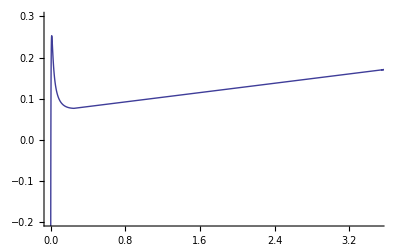

```mathematica
xm=0;
xM=3.5;
ym=-0.2;
yM=0.3;
gr3BPS=ListPlot[dataBPS,Joined-> True, PlotRange-> {{xm,xM},{ym,yM}}]
```

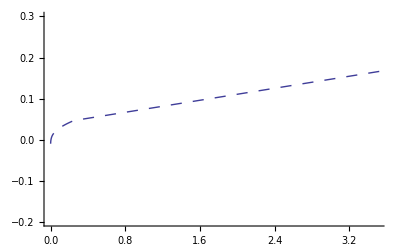

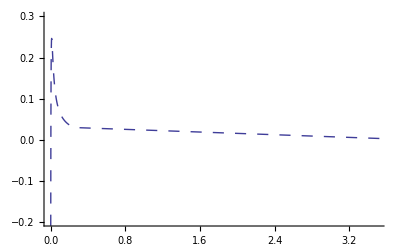

```mathematica
gr4E=ListPlot[dataBPSE,Joined->True,PlotStyle->Dashing[{0.02,0.02}],PlotRange->{{xm,xM},{ym,yM}}]
gr4I=ListPlot[dataBPSI,Joined->True,PlotStyle->Dashing[{0.02,0.02}],PlotRange->{{xm,xM},{ym,yM}}]
```

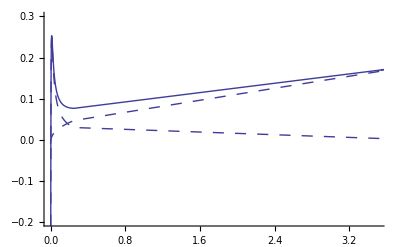

```mathematica
Show[gr3BPS,gr4E,gr4I,PlotRange-> {{xm,xM},{ym,yM}}]
```

```mathematica
st=OpenRead["range/1.3_coulombLog/range1.1.out"];
Do[Read[st,String],{i,1,19}];
ne=Read[st,Number]
Te=Read[st,Number]
Ti=Read[st,Number]
nn=Read[st,{Number,Number,Number}]
proj=Read[st,{Number,Number,Number}]
nts=81; (* stop reading when Ep goes critical,
            in this case when Ep < 0 *)
data=
Table[Read[st,{Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,nts}];
Close[st];
data
```

1.0000000000000001×10^25

3.

3.

{1.5000000000000001×10^-12,100,40}

{3540.,3.75309×10^6,2.}

{{0,0.,0.,1.30209×10^9,3540.,0.169597,0.00260936,0.166987},{1,1.5×10^-14,0.000019351,1.2779×10^9,3409.74,0.166978,0.00270316,0.164275},{2,3.×10^-14,0.000038342,1.2541×10^9,3283.87,0.164384,0.00280059,0.161583},{3,4.5×10^-14,0.0000569787,1.23066×10^9,3162.28,0.161816,0.0029018,0.158914},{4,6.×10^-14,0.0000752665,1.20759×10^9,3044.84,0.159274,0.00300694,0.156267},{5,7.5×10^-14,0.0000932111,1.18489×10^9,2931.42,0.156759,0.00311617,0.153643},{6,9.×10^-14,0.000110818,1.16254×10^9,2821.89,0.154273,0.00322966,0.151043},{7,1.05×10^-13,0.000128092,1.14055×10^9,2716.14,0.151816,0.00334758,0.148468},{8,1.2×10^-13,0.000145039,1.11891×10^9,2614.04,0.149389,0.0034701,0.145919},{9,1.35×10^-13,0.000161663,1.09761×10^9,2515.5,0.146992,0.00359743,0.143395},{10,1.5×10^-13,0.000177971,1.07666×10^9,2420.38,0.144626,0.00372975,0.140897},{11,1.65×10^-13,0.000193968,1.05605×10^9,2328.58,0.142293,0.00386728,0.138425},{12,1.8×10^-13,0.000209657,1.03577×10^9,2240.01,0.139991,0.00401022,0.135981},{13,1.95×10^-13,0.000225045,1.0158×10^9,2154.48,0.13788,0.00415892,0.133721},{14,2.1×10^-13,0.000240135,9.96151×10^8,2071.93,0.135628,0.00431358,0.131314},{15,2.25×10^-13,0.000254933,9.76822×10^8,1992.3,0.13341,0.00447439,0.128936},{16,2.4×10^-13,0.000269444,9.57809×10^8,1915.5,0.131228,0.00464159,0.126586},{17,2.55×10^-13,0.000283671,9.39107×10^8,1841.43,0.129082,0.00481548,0.124266},{18,2.7×10^-13,0.000297621,9.2071×10^8,1769.99,0.126971,0.00499634,0.121975},{19,2.85×10^-13,0.000311297,9.02615×10^8,1701.1,0.124897,0.00518448,0.119713},{20,3.×10^-13,0.000324703,8.84815×10^8,1634.67,0.122859,0.00538022,0.117479},{21,3.15×10^-13,0.000337845,8.67305×10^8,1570.61,0.120858,0.00558392,0.115274},{22,3.3×10^-13,0.000350726,8.50079×10^8,1508.84,0.118894,0.00579592,0.113098},{23,3.45×10^-13,0.000363351,8.33134×10^8,1449.29,0.116966,0.00601662,0.110949},{24,3.6×10^-13,0.000375723,8.16463×10^8,1391.87,0.115075,0.00624642,0.108829},{25,3.75×10^-13,0.000387848,8.00061×10^8,1336.5,0.113222,0.00648575,0.106736},{26,3.9×10^-13,0.000399728,7.83922×10^8,1283.13,0.111406,0.00673506,0.104671},{27,4.05×10^-13,0.000411369,7.68042×10^8,1231.67,0.109628,0.00699485,0.102633},{28,4.2×10^-13,0.000422773,7.52415×10^8,1182.06,0.107887,0.00726562,0.100622},{29,4.35×10^-13,0.000433944,7.37035×10^8,1134.23,0.106185,0.00754793,0.0986368},{30,4.5×10^-13,0.000444887,7.21897×10^8,1088.11,0.10452,0.00784236,0.096678},{31,4.65×10^-13,0.000455604,7.06995×10^8,1043.66,0.102894,0.00814955,0.0947447},{32,4.8×10^-13,0.0004661,6.92324×10^8,1000.79,0.101307,0.00847016,0.0928367},{33,4.95×10^-13,0.000476377,6.77879×10^8,959.464,0.0997584,0.00880492,0.0909535},{34,5.1×10^-13,0.000486439,6.63653×10^8,919.617,0.0982491,0.00915461,0.0890945},{35,5.25×10^-13,0.00049629,6.49641×10^8,881.195,0.0967794,0.00952005,0.0872594},{36,5.4×10^-13,0.000505931,6.35838×10^8,844.146,0.0953497,0.00990215,0.0854475},{37,5.55×10^-13,0.000515367,6.22237×10^8,808.419,0.0939603,0.0103019,0.0836584},{38,5.7×10^-13,0.000524601,6.08833×10^8,773.965,0.0926119,0.0107203,0.0818915},{39,5.85×10^-13,0.000533635,5.9562×10^8,740.735,0.0913048,0.0111586,0.0801463},{40,6.×10^-13,0.000542472,5.82591×10^8,708.684,0.0900399,0.0116179,0.078422},{41,6.15×10^-13,0.000551115,5.69742×10^8,677.767,0.0888178,0.0120997,0.0767181},{42,6.3×10^-13,0.000559567,5.57064×10^8,647.941,0.0876393,0.0126054,0.075034},{43,6.45×10^-13,0.00056783,5.44553×10^8,619.163,0.0865055,0.0131366,0.0733688},{44,6.6×10^-13,0.000575906,5.32202×10^8,591.394,0.0854172,0.0136952,0.071722},{45,6.75×10^-13,0.000583798,5.20003×10^8,564.595,0.0843759,0.0142831,0.0700928},{46,6.9×10^-13,0.000591508,5.07951×10^8,538.727,0.0833829,0.0149026,0.0684803},{47,7.05×10^-13,0.000599039,4.96038×10^8,513.753,0.0824397,0.015556,0.0668837},{48,7.2×10^-13,0.000606391,4.84257×10^8,489.639,0.0815482,0.016246,0.0653022},{49,7.35×10^-13,0.000613568,4.726×10^8,466.35,0.0807105,0.0169757,0.0637348},{50,7.5×10^-13,0.000620572,4.6106×10^8,443.853,0.079929,0.0177485,0.0621805},{51,7.65×10^-13,0.000627402,4.49627×10^8,422.114,0.0792066,0.0185682,0.0606384},{52,7.8×10^-13,0.000634062,4.38294×10^8,401.103,0.0785464,0.0194391,0.0591072},{53,7.95×10^-13,0.000640553,4.27052×10^8,380.79,0.0779521,0.0203663,0.0575859},{54,8.1×10^-13,0.000646876,4.15889×10^8,361.144,0.0774283,0.0213552,0.056073},{55,8.25×10^-13,0.000653031,4.04797×10^8,342.136,0.0769798,0.0224125,0.0545673},{56,8.4×10^-13,0.000659021,3.93763×10^8,323.739,0.0766128,0.0235456,0.0530672},{57,8.55×10^-13,0.000664846,3.82776×10^8,305.924,0.0763342,0.0247632,0.051571},{58,8.7×10^-13,0.000670506,3.71822×10^8,288.666,0.0761526,0.0260757,0.0500769},{59,8.85×10^-13,0.000676002,3.60887×10^8,271.936,0.076078,0.0274951,0.0485829},{60,9.×10^-13,0.000681334,3.49954×10^8,255.709,0.0761226,0.0290358,0.0470868},{61,9.15×10^-13,0.000686502,3.39005×10^8,239.959,0.076301,0.0307151,0.0455858},{62,9.3×10^-13,0.000691505,3.28021×10^8,224.66,0.0766313,0.0325541,0.0440772},{63,9.45×10^-13,0.000696344,3.16976×10^8,209.786,0.0771361,0.0345786,0.0425575},{64,9.6×10^-13,0.000701016,3.05845×10^8,195.311,0.0778436,0.0368208,0.0410228},{65,9.75×10^-13,0.00070552,2.94596×10^8,181.208,0.0787896,0.0393211,0.0394686},{66,9.9×10^-13,0.000709854,2.83191×10^8,167.449,0.0800235,0.0421344,0.0378891},{67,1.005×10^-12,0.000714016,2.71585×10^8,154.005,0.0816014,0.0453236,0.0362778},{68,1.02×10^-12,0.000718002,2.59723×10^8,140.846,0.0836079,0.0489816,0.0346263},{69,1.035×10^-12,0.000721807,2.47535×10^8,127.938,0.0861566,0.0532326,0.032924},{70,1.05×10^-12,0.000725427,2.34934×10^8,115.243,0.0894118,0.0582544,0.0311575},{71,1.065×10^-12,0.000728854,2.21801×10^8,102.719,0.0936055,0.064297,0.0293085},{72,1.08×10^-12,0.00073208,2.07978×10^8,90.3147,0.0991043,0.0717525,0.0273518},{73,1.095×10^-12,0.000735091,1.93239×10^8,77.9674,0.1065,0.0812487,0.0252512},{74,1.11×10^-12,0.000737872,1.77245×10^8,65.5952,0.116821,0.0938703,0.0229507},{75,1.125×10^-12,0.000740402,1.59453×10^8,53.0871,0.132015,0.111659,0.0203561},{76,1.14×10^-12,0.000742645,1.38911×10^8,40.2901,0.156129,0.138839,0.0172896},{77,1.155×10^-12,0.000744549,1.13805×10^8,27.0424,0.197675,0.184323,0.0133522},{78,1.17×10^-12,0.000746025,8.12791×10^7,13.7937,0.251887,0.244326,0.00756118},{79,1.185×10^-12,0.000746991,5.0317×10^7,5.28633,0.128848,0.128069,0.000778961},{80,1.2×10^-12,0.000747665,4.22907×10^7,3.73433,0.0156623,0.0170024,-0.00134011}}

81

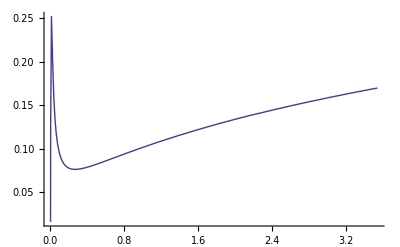

```mathematica
nmax=Length[data]
grdedx=ListPlot[Table[{data[[i,5]]/1000,data[[i,6]]},{i,1,nmax}],Joined-> True ](* {Energy,dE/dx}}  *)
```

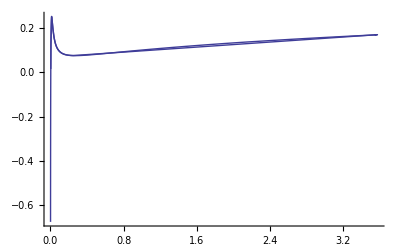

```mathematica
Show[grdedx,gr3BPS]
```

#### E vs x and range R

```mathematica
dEdxEBPS=Interpolation[dataBPS];
```

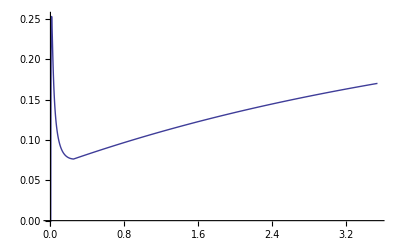

```mathematica
Plot[dEdxEBPS[e],{e,emin,emax}]
```

```mathematica
E0=emax;
dxEBPS[E_] :=1/dEdxEBPS[E]
xEBPS[E_]   := NIntegrate[1/dEdxEBPS[Ep],{Ep,E,E0},PrecisionGoal->Automatic]
```

```mathematica
FindRoot[dEdxEBPS[EE]==0,{EE,0.0.01}];
EzeroBPSa=EE /. %
```

InterpolatingFunction::dmval: Input value {0.`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0008690785226912976`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

0.00359481

```mathematica
FindRoot[dEdxEBPS[EE]==0,{EE, EzeroBPSa}];
EzeroBPS=EE /. %
```

0.00359481

```mathematica
dEdxEBPS[EzeroBPS]
```

-3.85644×10^-14

```mathematica
eth=2*T/1000
dEdxEBPS[eth]
xEBPS[eth]
```

0.006

0.164323

29.4227

```mathematica
NN=1000;
E1=EzeroBPS+eps;
E1=eth;
dE=(E0-E1)/NN;
dataExBPS=Table[{xEBPS[E],E},{E,E1,emax,dE}];
```

```mathematica
xy1=dataExBPS[[2]]
xy2=dataExBPS[[1]]
dxy=xy2-xy1
m=dxy[[2]]/dxy[[1]]
b=xy1[[2]]-m*xy1[[1]]
xRBPS=-b/m
```

{29.4058,0.009534}

{29.4227,0.006}

{0.0168569,-0.003534}

-0.209648

6.17439

29.4513

```mathematica
dataExBPS=Prepend[dataExBPS,{xRBPS,0}]
```

{{29.4513,0},{29.4227,0.006},{29.4058,0.009534},{29.3917,0.013068},{29.3775,0.016602},{29.3625,0.020136},{29.3465,0.02367},{29.3292,0.027204},{29.3107,0.030738},{29.2908,0.034272},{29.2698,0.037806},{29.2474,0.04134},{29.2239,0.044874},{29.1992,0.048408},{29.1734,0.051942},{29.1465,0.055476},{29.1186,0.05901},{29.0897,0.062544},{29.0599,0.066078},{29.0291,0.069612},{28.9975,0.073146},{28.9651,0.07668},{28.9319,0.080214},{28.8979,0.083748},{28.8633,0.087282},{28.8279,0.090816},{28.792,0.09435},{28.7554,0.097884},{28.7182,0.101418},{28.6805,0.104952},{28.6422,0.108486},{28.6035,0.11202},{28.5642,0.115554},{28.5245,0.119088},{28.4844,0.122622},{28.4439,0.126156},{28.403,0.12969},{28.3617,0.133224},{28.3201,0.136758},{28.2781,0.140292},{28.2359,0.143826},{28.1933,0.14736},{28.1505,0.150894},{28.1074,0.154428},{28.064,0.157962},{28.0204,0.161496},{27.9766,0.16503},{27.9326,0.168564},{27.8884,0.172098},{27.844,0.175632},{27.7995,0.179166},{27.7548,0.1827},{27.7099,0.186234},{27.6649,0.189768},{27.6197,0.193302},{27.5745,0.196836},{27.5291,0.20037},{27.4836,0.203904},{27.438,0.207438},{27.3923,0.210972},{27.3466,0.214506},{27.3007,0.21804},{27.2548,0.221574},{27.2088,0.225108},{27.1628,0.228642},{27.1167,0.232176},{27.0706,0.23571},{27.0244,0.239244},{26.9782,0.242778},{26.932,0.246312},{26.8857,0.249846},{26.8395,0.25338},{26.7933,0.256914},{26.7473,0.260448},{26.7013,0.263982},{26.6554,0.267516},{26.6096,0.27105},{26.5638,0.274584},{26.5182,0.278118},{26.4726,0.281652},{26.4271,0.285186},{26.3817,0.28872},{26.3364,0.292254},{26.2911,0.295788},{26.246,0.299322},{26.2009,0.302856},{26.1559,0.30639},{26.1109,0.309924},{26.0661,0.313458},{26.0213,0.316992},{25.9766,0.320526},{25.932,0.32406},{25.8874,0.327594},{25.843,0.331128},{25.7986,0.334662},{25.7543,0.338196},{25.71,0.34173},{25.6659,0.345264},{25.6218,0.348798},{25.5778,0.352332},{25.5338,0.355866},{25.4899,0.3594},{25.4462,0.362934},{25.4024,0.366468},{25.3588,0.370002},{25.3152,0.373536},{25.2717,0.37707},{25.2283,0.380604},{25.1849,0.384138},{25.1417,0.387672},{25.0985,0.391206},{25.0553,0.39474},{25.0122,0.398274},{24.9692,0.401808},{24.9263,0.405342},{24.8835,0.408876},{24.8407,0.41241},{24.798,0.415944},{24.7553,0.419478},{24.7127,0.423012},{24.6702,0.426546},{24.6278,0.43008},{24.5854,0.433614},{24.5431,0.437148},{24.5009,0.440682},{24.4587,0.444216},{24.4166,0.44775},{24.3746,0.451284},{24.3326,0.454818},{24.2907,0.458352},{24.2488,0.461886},{24.2071,0.46542},{24.1654,0.468954},{24.1237,0.472488},{24.0821,0.476022},{24.0406,0.479556},{23.9992,0.48309},{23.9578,0.486624},{23.9165,0.490158},{23.8752,0.493692},{23.8341,0.497226},{23.7929,0.50076},{23.7519,0.504294},{23.7109,0.507828},{23.6699,0.511362},{23.629,0.514896},{23.5882,0.51843},{23.5475,0.521964},{23.5068,0.525498},{23.4662,0.529032},{23.4256,0.532566},{23.3851,0.5361},{23.3447,0.539634},{23.3043,0.543168},{23.2639,0.546702},{23.2237,0.550236},{23.1835,0.55377},{23.1433,0.557304},{23.1032,0.560838},{23.0632,0.564372},{23.0233,0.567906},{22.9833,0.57144},{22.9435,0.574974},{22.9037,0.578508},{22.864,0.582042},{22.8243,0.585576},{22.7847,0.58911},{22.7451,0.592644},{22.7056,0.596178},{22.6662,0.599712},{22.6268,0.603246},{22.5875,0.60678},{22.5482,0.610314},{22.509,0.613848},{22.4698,0.617382},{22.4307,0.620916},{22.3917,0.62445},{22.3527,0.627984},{22.3137,0.631518},{22.2748,0.635052},{22.236,0.638586},{22.1972,0.64212},{22.1585,0.645654},{22.1198,0.649188},{22.0812,0.652722},{22.0427,0.656256},{22.0042,0.65979},{21.9657,0.663324},{21.9273,0.666858},{21.889,0.670392},{21.8507,0.673926},{21.8125,0.67746},{21.7743,0.680994},{21.7361,0.684528},{21.6981,0.688062},{21.66,0.691596},{21.6221,0.69513},{21.5841,0.698664},{21.5463,0.702198},{21.5084,0.705732},{21.4707,0.709266},{21.4329,0.7128},{21.3953,0.716334},{21.3577,0.719868},{21.3201,0.723402},{21.2826,0.726936},{21.2451,0.73047},{21.2077,0.734004},{21.1703,0.737538},{21.133,0.741072},{21.0957,0.744606},{21.0585,0.74814},{21.0213,0.751674},{20.9842,0.755208},{20.9472,0.758742},{20.9101,0.762276},{20.8732,0.76581},{20.8362,0.769344},{20.7993,0.772878},{20.7625,0.776412},{20.7257,0.779946},{20.689,0.78348},{20.6523,0.787014},{20.6157,0.790548},{20.5791,0.794082},{20.5425,0.797616},{20.506,0.80115},{20.4696,0.804684},{20.4332,0.808218},{20.3968,0.811752},{20.3605,0.815286},{20.3242,0.81882},{20.288,0.822354},{20.2519,0.825888},{20.2157,0.829422},{20.1796,0.832956},{20.1436,0.83649},{20.1076,0.840024},{20.0717,0.843558},{20.0358,0.847092},{19.9999,0.850626},{19.9641,0.85416},{19.9283,0.857694},{19.8926,0.861228},{19.8569,0.864762},{19.8213,0.868296},{19.7857,0.87183},{19.7501,0.875364},{19.7146,0.878898},{19.6792,0.882432},{19.6438,0.885966},{19.6084,0.8895},{19.5731,0.893034},{19.5378,0.896568},{19.5025,0.900102},{19.4673,0.903636},{19.4322,0.90717},{19.397,0.910704},{19.362,0.914238},{19.3269,0.917772},{19.2919,0.921306},{19.257,0.92484},{19.2221,0.928374},{19.1872,0.931908},{19.1524,0.935442},{19.1176,0.938976},{19.0829,0.94251},{19.0482,0.946044},{19.0135,0.949578},{18.9789,0.953112},{18.9443,0.956646},{18.9098,0.96018},{18.8753,0.963714},{18.8408,0.967248},{18.8064,0.970782},{18.772,0.974316},{18.7377,0.97785},{18.7034,0.981384},{18.6691,0.984918},{18.6349,0.988452},{18.6007,0.991986},{18.5666,0.99552},{18.5325,0.999054},{18.4985,1.00259},{18.4644,1.00612},{18.4305,1.00966},{18.3965,1.01319},{18.3626,1.01672},{18.3287,1.02026},{18.2949,1.02379},{18.2611,1.02733},{18.2274,1.03086},{18.1937,1.03439},{18.16,1.03793},{18.1264,1.04146},{18.0928,1.045},{18.0592,1.04853},{18.0257,1.05206},{17.9922,1.0556},{17.9587,1.05913},{17.9253,1.06267},{17.892,1.0662},{17.8586,1.06973},{17.8253,1.07327},{17.7921,1.0768},{17.7588,1.08034},{17.7256,1.08387},{17.6925,1.0874},{17.6594,1.09094},{17.6263,1.09447},{17.5932,1.09801},{17.5602,1.10154},{17.5273,1.10507},{17.4943,1.10861},{17.4614,1.11214},{17.4286,1.11568},{17.3957,1.11921},{17.3629,1.12274},{17.3302,1.12628},{17.2974,1.12981},{17.2648,1.13335},{17.2321,1.13688},{17.1995,1.14041},{17.1669,1.14395},{17.1343,1.14748},{17.1018,1.15102},{17.0693,1.15455},{17.0369,1.15808},{17.0045,1.16162},{16.9721,1.16515},{16.9398,1.16869},{16.9075,1.17222},{16.8752,1.17575},{16.8429,1.17929},{16.8107,1.18282},{16.7786,1.18636},{16.7464,1.18989},{16.7143,1.19342},{16.6822,1.19696},{16.6502,1.20049},{16.6182,1.20403},{16.5862,1.20756},{16.5543,1.21109},{16.5224,1.21463},{16.4905,1.21816},{16.4586,1.2217},{16.4268,1.22523},{16.395,1.22876},{16.3633,1.2323},{16.3316,1.23583},{16.2999,1.23937},{16.2683,1.2429},{16.2366,1.24643},{16.2051,1.24997},{16.1735,1.2535},{16.142,1.25704},{16.1105,1.26057},{16.079,1.2641},{16.0476,1.26764},{16.0162,1.27117},{15.9848,1.27471},{15.9535,1.27824},{15.9222,1.28177},{15.8909,1.28531},{15.8597,1.28884},{15.8285,1.29238},{15.7973,1.29591},{15.7662,1.29944},{15.735,1.30298},{15.704,1.30651},{15.6729,1.31005},{15.6419,1.31358},{15.6109,1.31711},{15.5799,1.32065},{15.549,1.32418},{15.5181,1.32772},{15.4872,1.33125},{15.4564,1.33478},{15.4256,1.33832},{15.3948,1.34185},{15.364,1.34539},{15.3333,1.34892},{15.3026,1.35245},{15.2719,1.35599},{15.2413,1.35952},{15.2107,1.36306},{15.1801,1.36659},{15.1496,1.37012},{15.119,1.37366},{15.0885,1.37719},{15.0581,1.38073},{15.0277,1.38426},{14.9972,1.38779},{14.9669,1.39133},{14.9365,1.39486},{14.9062,1.3984},{14.8759,1.40193},{14.8457,1.40546},{14.8154,1.409},{14.7852,1.41253},{14.755,1.41607},{14.7249,1.4196},{14.6948,1.42313},{14.6647,1.42667},{14.6346,1.4302},{14.6046,1.43374},{14.5746,1.43727},{14.5446,1.4408},{14.5146,1.44434},{14.4847,1.44787},{14.4548,1.45141},{14.4249,1.45494},{14.3951,1.45847},{14.3653,1.46201},{14.3355,1.46554},{14.3057,1.46908},{14.276,1.47261},{14.2463,1.47614},{14.2166,1.47968},{14.1869,1.48321},{14.1573,1.48675},{14.1277,1.49028},{14.0981,1.49381},{14.0686,1.49735},{14.0391,1.50088},{14.0096,1.50442},{13.9801,1.50795},{13.9507,1.51148},{13.9212,1.51502},{13.8919,1.51855},{13.8625,1.52209},{13.8331,1.52562},{13.8038,1.52915},{13.7746,1.53269},{13.7453,1.53622},{13.7161,1.53976},{13.6868,1.54329},{13.6577,1.54682},{13.6285,1.55036},{13.5994,1.55389},{13.5703,1.55743},{13.5412,1.56096},{13.5121,1.56449},{13.4831,1.56803},{13.4541,1.57156},{13.4251,1.5751},{13.3962,1.57863},{13.3672,1.58216},{13.3383,1.5857},{13.3094,1.58923},{13.2806,1.59277},{13.2518,1.5963},{13.2229,1.59983},{13.1942,1.60337},{13.1654,1.6069},{13.1367,1.61044},{13.108,1.61397},{13.0793,1.6175},{13.0506,1.62104},{13.022,1.62457},{12.9934,1.62811},{12.9648,1.63164},{12.9362,1.63517},{12.9077,1.63871},{12.8792,1.64224},{12.8507,1.64578},{12.8222,1.64931},{12.7938,1.65284},{12.7653,1.65638},{12.737,1.65991},{12.7086,1.66345},{12.6802,1.66698},{12.6519,1.67051},{12.6236,1.67405},{12.5953,1.67758},{12.5671,1.68112},{12.5388,1.68465},{12.5106,1.68818},{12.4824,1.69172},{12.4543,1.69525},{12.4261,1.69879},{12.398,1.70232},{12.3699,1.70585},{12.3419,1.70939},{12.3138,1.71292},{12.2858,1.71646},{12.2578,1.71999},{12.2298,1.72352},{12.2019,1.72706},{12.1739,1.73059},{12.146,1.73413},{12.1181,1.73766},{12.0903,1.74119},{12.0624,1.74473},{12.0346,1.74826},{12.0068,1.7518},{11.979,1.75533},{11.9513,1.75886},{11.9235,1.7624},{11.8958,1.76593},{11.8681,1.76947},{11.8405,1.773},{11.8128,1.77653},{11.7852,1.78007},{11.7576,1.7836},{11.73,1.78714},{11.7025,1.79067},{11.6749,1.7942},{11.6474,1.79774},{11.6199,1.80127},{11.5924,1.80481},{11.565,1.80834},{11.5376,1.81187},{11.5102,1.81541},{11.4828,1.81894},{11.4554,1.82248},{11.4281,1.82601},{11.4007,1.82954},{11.3734,1.83308},{11.3462,1.83661},{11.3189,1.84015},{11.2917,1.84368},{11.2645,1.84721},{11.2373,1.85075},{11.2101,1.85428},{11.1829,1.85782},{11.1558,1.86135},{11.1287,1.86488},{11.1016,1.86842},{11.0745,1.87195},{11.0475,1.87549},{11.0204,1.87902},{10.9934,1.88255},{10.9664,1.88609},{10.9395,1.88962},{10.9125,1.89316},{10.8856,1.89669},{10.8587,1.90022},{10.8318,1.90376},{10.8049,1.90729},{10.7781,1.91083},{10.7512,1.91436},{10.7244,1.91789},{10.6976,1.92143},{10.6709,1.92496},{10.6441,1.9285},{10.6174,1.93203},{10.5907,1.93556},{10.564,1.9391},{10.5373,1.94263},{10.5107,1.94617},{10.484,1.9497},{10.4574,1.95323},{10.4308,1.95677},{10.4043,1.9603},{10.3777,1.96384},{10.3512,1.96737},{10.3247,1.9709},{10.2982,1.97444},{10.2717,1.97797},{10.2453,1.98151},{10.2188,1.98504},{10.1924,1.98857},{10.166,1.99211},{10.1396,1.99564},{10.1133,1.99918},{10.0869,2.00271},{10.0606,2.00624},{10.0343,2.00978},{10.008,2.01331},{9.98174,2.01685},{9.95549,2.02038},{9.92926,2.02391},{9.90305,2.02745},{9.87686,2.03098},{9.85069,2.03452},{9.82454,2.03805},{9.7984,2.04158},{9.77228,2.04512},{9.74618,2.04865},{9.7201,2.05219},{9.69404,2.05572},{9.668,2.05925},{9.64197,2.06279},{9.61597,2.06632},{9.58998,2.06986},{9.56401,2.07339},{9.53805,2.07692},{9.51212,2.08046},{9.4862,2.08399},{9.4603,2.08753},{9.43442,2.09106},{9.40856,2.09459},{9.38272,2.09813},{9.35689,2.10166},{9.33108,2.1052},{9.30529,2.10873},{9.27952,2.11226},{9.25376,2.1158},{9.22802,2.11933},{9.2023,2.12287},{9.1766,2.1264},{9.15091,2.12993},{9.12524,2.13347},{9.09959,2.137},{9.07396,2.14054},{9.04835,2.14407},{9.02275,2.1476},{8.99717,2.15114},{8.9716,2.15467},{8.94606,2.15821},{8.92053,2.16174},{8.89502,2.16527},{8.86952,2.16881},{8.84404,2.17234},{8.81858,2.17588},{8.79314,2.17941},{8.76771,2.18294},{8.7423,2.18648},{8.71691,2.19001},{8.69154,2.19355},{8.66618,2.19708},{8.64083,2.20061},{8.61551,2.20415},{8.5902,2.20768},{8.56491,2.21122},{8.53963,2.21475},{8.51438,2.21828},{8.48913,2.22182},{8.46391,2.22535},{8.4387,2.22889},{8.41351,2.23242},{8.38833,2.23595},{8.36317,2.23949},{8.33803,2.24302},{8.31291,2.24656},{8.2878,2.25009},{8.2627,2.25362},{8.23763,2.25716},{8.21256,2.26069},{8.18752,2.26423},{8.16249,2.26776},{8.13748,2.27129},{8.11248,2.27483},{8.0875,2.27836},{8.06254,2.2819},{8.03759,2.28543},{8.01266,2.28896},{7.98774,2.2925},{7.96284,2.29603},{7.93796,2.29957},{7.91309,2.3031},{7.88824,2.30663},{7.8634,2.31017},{7.83858,2.3137},{7.81377,2.31724},{7.78898,2.32077},{7.76421,2.3243},{7.73945,2.32784},{7.71471,2.33137},{7.68998,2.33491},{7.66527,2.33844},{7.64057,2.34197},{7.61589,2.34551},{7.59123,2.34904},{7.56658,2.35258},{7.54194,2.35611},{7.51732,2.35964},{7.49272,2.36318},{7.46813,2.36671},{7.44356,2.37025},{7.419,2.37378},{7.39446,2.37731},{7.36993,2.38085},{7.34542,2.38438},{7.32092,2.38792},{7.29644,2.39145},{7.27197,2.39498},{7.24752,2.39852},{7.22309,2.40205},{7.19866,2.40559},{7.17426,2.40912},{7.14986,2.41265},{7.12549,2.41619},{7.10113,2.41972},{7.07678,2.42326},{7.05245,2.42679},{7.02813,2.43032},{7.00382,2.43386},{6.97954,2.43739},{6.95526,2.44093},{6.931,2.44446},{6.90676,2.44799},{6.88253,2.45153},{6.85831,2.45506},{6.83411,2.4586},{6.80993,2.46213},{6.78575,2.46566},{6.7616,2.4692},{6.73745,2.47273},{6.71333,2.47627},{6.68921,2.4798},{6.66511,2.48333},{6.64103,2.48687},{6.61696,2.4904},{6.5929,2.49394},{6.56886,2.49747},{6.54483,2.501},{6.52081,2.50454},{6.49681,2.50807},{6.47283,2.51161},{6.44886,2.51514},{6.4249,2.51867},{6.40095,2.52221},{6.37702,2.52574},{6.35311,2.52928},{6.32921,2.53281},{6.30532,2.53634},{6.28145,2.53988},{6.25759,2.54341},{6.23374,2.54695},{6.20991,2.55048},{6.18609,2.55401},{6.16228,2.55755},{6.13849,2.56108},{6.11472,2.56462},{6.09095,2.56815},{6.0672,2.57168},{6.04347,2.57522},{6.01974,2.57875},{5.99604,2.58229},{5.97234,2.58582},{5.94866,2.58935},{5.92499,2.59289},{5.90134,2.59642},{5.87769,2.59996},{5.85407,2.60349},{5.83045,2.60702},{5.80685,2.61056},{5.78326,2.61409},{5.75969,2.61763},{5.73613,2.62116},{5.71258,2.62469},{5.68905,2.62823},{5.66553,2.63176},{5.64202,2.6353},{5.61852,2.63883},{5.59504,2.64236},{5.57157,2.6459},{5.54812,2.64943},{5.52468,2.65297},{5.50125,2.6565},{5.47783,2.66003},{5.45443,2.66357},{5.43104,2.6671},{5.40766,2.67064},{5.3843,2.67417},{5.36095,2.6777},{5.33761,2.68124},{5.31428,2.68477},{5.29097,2.68831},{5.26767,2.69184},{5.24438,2.69537},{5.22111,2.69891},{5.19785,2.70244},{5.1746,2.70598},{5.15137,2.70951},{5.12814,2.71304},{5.10493,2.71658},{5.08173,2.72011},{5.05855,2.72365},{5.03538,2.72718},{5.01222,2.73071},{4.98907,2.73425},{4.96594,2.73778},{4.94281,2.74132},{4.9197,2.74485},{4.89661,2.74838},{4.87352,2.75192},{4.85045,2.75545},{4.82739,2.75899},{4.80434,2.76252},{4.78131,2.76605},{4.75828,2.76959},{4.73527,2.77312},{4.71228,2.77666},{4.68929,2.78019},{4.66632,2.78372},{4.64335,2.78726},{4.62041,2.79079},{4.59747,2.79433},{4.57454,2.79786},{4.55163,2.80139},{4.52873,2.80493},{4.50584,2.80846},{4.48297,2.812},{4.4601,2.81553},{4.43725,2.81906},{4.41441,2.8226},{4.39158,2.82613},{4.36876,2.82967},{4.34596,2.8332},{4.32317,2.83673},{4.30039,2.84027},{4.27762,2.8438},{4.25486,2.84734},{4.23212,2.85087},{4.20938,2.8544},{4.18666,2.85794},{4.16395,2.86147},{4.14125,2.86501},{4.11857,2.86854},{4.09589,2.87207},{4.07323,2.87561},{4.05058,2.87914},{4.02794,2.88268},{4.00531,2.88621},{3.9827,2.88974},{3.96009,2.89328},{3.9375,2.89681},{3.91492,2.90035},{3.89235,2.90388},{3.86979,2.90741},{3.84725,2.91095},{3.82471,2.91448},{3.80219,2.91802},{3.77967,2.92155},{3.75717,2.92508},{3.73468,2.92862},{3.71221,2.93215},{3.68974,2.93569},{3.66728,2.93922},{3.64484,2.94275},{3.62241,2.94629},{3.59998,2.94982},{3.57757,2.95336},{3.55518,2.95689},{3.53279,2.96042},{3.51041,2.96396},{3.48805,2.96749},{3.46569,2.97103},{3.44335,2.97456},{3.42102,2.97809},{3.3987,2.98163},{3.37639,2.98516},{3.35409,2.9887},{3.3318,2.99223},{3.30952,2.99576},{3.28726,2.9993},{3.265,3.00283},{3.24276,3.00637},{3.22053,3.0099},{3.19831,3.01343},{3.17609,3.01697},{3.15389,3.0205},{3.13171,3.02404},{3.10953,3.02757},{3.08736,3.0311},{3.0652,3.03464},{3.04306,3.03817},{3.02092,3.04171},{2.9988,3.04524},{2.97669,3.04877},{2.95458,3.05231},{2.93249,3.05584},{2.91041,3.05938},{2.88834,3.06291},{2.86628,3.06644},{2.84423,3.06998},{2.82219,3.07351},{2.80016,3.07705},{2.77815,3.08058},{2.75614,3.08411},{2.73414,3.08765},{2.71216,3.09118},{2.69018,3.09472},{2.66822,3.09825},{2.64627,3.10178},{2.62432,3.10532},{2.60239,3.10885},{2.58047,3.11239},{2.55855,3.11592},{2.53665,3.11945},{2.51476,3.12299},{2.49288,3.12652},{2.47101,3.13006},{2.44915,3.13359},{2.4273,3.13712},{2.40546,3.14066},{2.38363,3.14419},{2.36181,3.14773},{2.34,3.15126},{2.3182,3.15479},{2.29641,3.15833},{2.27463,3.16186},{2.25287,3.1654},{2.23111,3.16893},{2.20936,3.17246},{2.18762,3.176},{2.16589,3.17953},{2.14418,3.18307},{2.12247,3.1866},{2.10077,3.19013},{2.07909,3.19367},{2.05741,3.1972},{2.03574,3.20074},{2.01408,3.20427},{1.99244,3.2078},{1.9708,3.21134},{1.94917,3.21487},{1.92755,3.21841},{1.90595,3.22194},{1.88435,3.22547},{1.86276,3.22901},{1.84118,3.23254},{1.81962,3.23608},{1.79806,3.23961},{1.77651,3.24314},{1.75497,3.24668},{1.73344,3.25021},{1.71192,3.25375},{1.69041,3.25728},{1.66891,3.26081},{1.64743,3.26435},{1.62595,3.26788},{1.60447,3.27142},{1.58301,3.27495},{1.56156,3.27848},{1.54012,3.28202},{1.51869,3.28555},{1.49727,3.28909},{1.47586,3.29262},{1.45445,3.29615},{1.43306,3.29969},{1.41168,3.30322},{1.3903,3.30676},{1.36894,3.31029},{1.34758,3.31382},{1.32624,3.31736},{1.3049,3.32089},{1.28358,3.32443},{1.26226,3.32796},{1.24095,3.33149},{1.21965,3.33503},{1.19836,3.33856},{1.17708,3.3421},{1.15581,3.34563},{1.13455,3.34916},{1.1133,3.3527},{1.09206,3.35623},{1.07083,3.35977},{1.0496,3.3633},{1.02839,3.36683},{1.00719,3.37037},{0.98599,3.3739},{0.964804,3.37744},{0.943627,3.38097},{0.92246,3.3845},{0.901301,3.38804},{0.880152,3.39157},{0.859012,3.39511},{0.837881,3.39864},{0.816759,3.40217},{0.795646,3.40571},{0.774543,3.40924},{0.753448,3.41278},{0.732363,3.41631},{0.711286,3.41984},{0.690219,3.42338},{0.669161,3.42691},{0.648112,3.43045},{0.627072,3.43398},{0.606041,3.43751},{0.585019,3.44105},{0.564006,3.44458},{0.543002,3.44812},{0.522007,3.45165},{0.50102,3.45518},{0.480043,3.45872},{0.459075,3.46225},{0.438115,3.46579},{0.417165,3.46932},{0.396223,3.47285},{0.37529,3.47639},{0.354366,3.47992},{0.333451,3.48346},{0.312545,3.48699},{0.291647,3.49052},{0.270759,3.49406},{0.249879,3.49759},{0.229008,3.50113},{0.208145,3.50466},{0.187292,3.50819},{0.166447,3.51173},{0.14561,3.51526},{0.124783,3.5188},{0.103964,3.52233},{0.083154,3.52586},{0.0623525,3.5294},{0.0415597,3.53293},{0.0207756,3.53647},{0,3.54}}

```mathematica
ExBPS=Interpolation[dataExBPS];
```

```mathematica
ExBPS[xRBPS]
```

0.

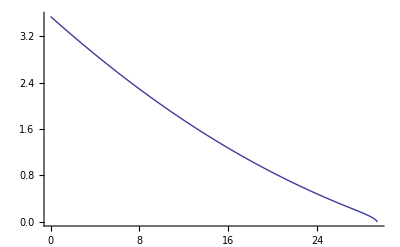

```mathematica
grExBPS=ListPlot[dataExBPS,Joined->True]
```

#### dE/dx vs E: dEdxEBPS

```mathematica
dEdxEeBPS =Interpolation[dataBPSE];
dEdxEiBPS =Interpolation[dataBPSI];
```

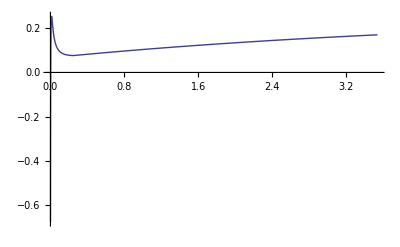

```mathematica
grdEdxEBPS=Plot[dEdxEBPS[e],{e,emin,emax},PlotPoints->10000,PlotRange->All]
```

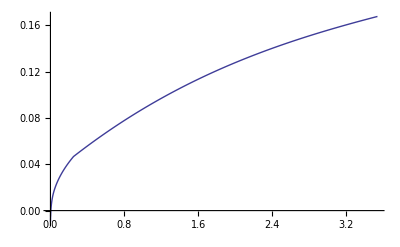

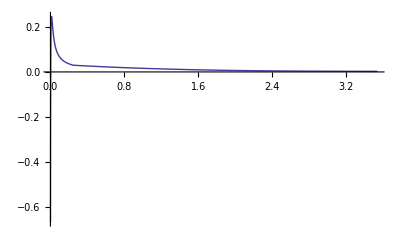

```mathematica
grdEdxEeBPS=Plot[dEdxEeBPS[e],{e,emin,emax},PlotPoints->1000,PlotRange->All]
grdEdxEiBPS=Plot[dEdxEiBPS[e],{e,emin,emax},PlotPoints->1000,PlotRange->All]
```

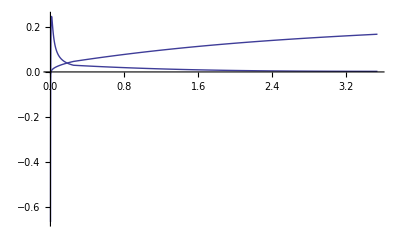

```mathematica
grdEdxEeiBPS=Show[grdEdxEeBPS,grdEdxEiBPS]
```

#### dE/dx vs x: dEdxx BPS

```mathematica
dEdxxBPS[x_] := dEdxEBPS[ExBPS[x]]
dEdxxeBPS[x_] := dEdxEeBPS[ExBPS[x]]
dEdxxiBPS[x_] := dEdxEiBPS[ExBPS[x]]
```

```mathematica
x0=FindRoot[dEdxxBPS[xRBPS-x0]==0,{x0,0.01}][[1,2]]
```

0.0165486

```mathematica
dEdxxBPS[xRBPS]
dEdxxBPS[xRBPS- x0]
```

InterpolatingFunction::dmval: Input value {0.`} lies outside the range of data in the interpolating function. Extrapolation will be used.

-2.0462

-3.55936×10^-14

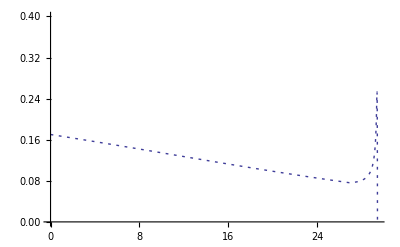

```mathematica
grdEdxxBPS=Plot[dEdxxBPS[x],{x,0,xRBPS-x0},PlotStyle->Dashing[{0.005,0.01}],
PlotPoints->1000,PlotRange->{0,0.4}]
```

```mathematica
xRBPS
xRBPSmax=xRBPS-x0
```

29.4513

29.4347

```mathematica
xRBPSmax
```

29.4347

```mathematica
x0=3.5;
NIntegrate[dEdxxBPS[x],{x,0,x0},MaxRecursion->10]
NIntegrate[dEdxxBPS[x],{x,x0,xRBPSmax},MaxRecursion->10]
% + %%
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

0.574397

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

2.96076

3.53516

```mathematica
100*(%-E0)/E0
```

-0.136816

partitioned among plasma components

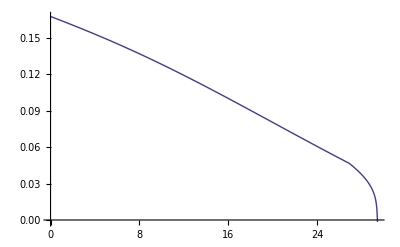

```mathematica
grdEdxxeBPS=Plot[dEdxxeBPS[x] ,{x,0,xRBPSmax},PlotPoints->1000,PlotPoints->All]
```

```mathematica
Ee=NIntegrate[dEdxxeBPS[x],{x,0,xRBPSmax}]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

3.05571

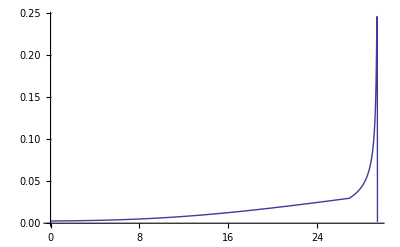

```mathematica
grdEdxxiBPS=Plot[dEdxxiBPS[x] ,{x,0,xRBPSmax},PlotPoints->1000,PlotRange->All]
```

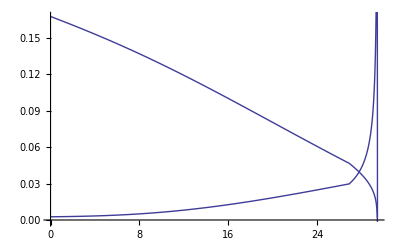

```mathematica
grdEdxxeiBPS=Show[grdEdxxeBPS,grdEdxxiBPS]
```

```mathematica
xRBPSmax
```

29.4347

```mathematica
x1=3.5;
NIntegrate[dEdxxiBPS[x],{x,0,x1},MaxRecursion->10]
NIntegrate[dEdxxiBPS[x],{x,x1,xRBPSmax},MaxRecursion->10]
Ei=% + %%
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

0.0100503

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

0.469393

0.479444

```mathematica
{Ee,Ei,Ee+Ei,E0}
```

{3.05571,0.479444,3.53516,3.54}

```mathematica
100*(E0-Ee-Ei)/E0
```

0.136818

### LP cf BPS: Figs

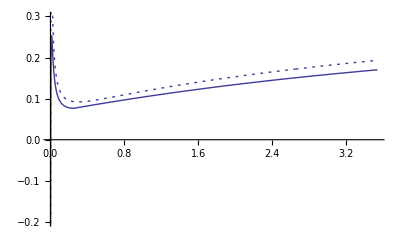

```mathematica
grdEdxELPBPS=Show[grdEdxELP,grdEdxEBPS,PlotRange->{ym,yM}]
```

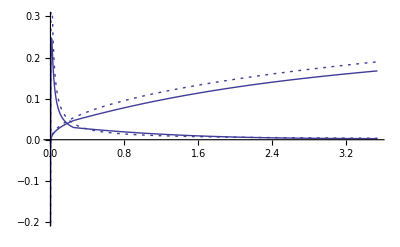

```mathematica
grdEdxEeiLPBPS=Show[grdEdxEeLP,grdEdxEiLP,
grdEdxEeBPS,grdEdxEiBPS,PlotRange->{ym,yM}]
```

```mathematica
id
```

```mathematica
NN=300;
Emin=emin;
Emax=0.2;
dE=(Emax-Emin)/NN;
data1=
Table[{EE,dEdxELP[EE],dEdxEeLP[EE],dEdxEiLP[EE],
dEdxEBPS[EE],dEdxEeBPS[EE],dEdxEiBPS[EE]},{EE,Emin,Emax,dE}];


NN=100;
Emin=Emax;
Emax=emax;
dE=(Emax-Emin)/NN;
data2=
Table[{EE,dEdxELP[EE],dEdxEeLP[EE],dEdxEiLP[EE],
dEdxEBPS[EE],dEdxEeBPS[EE],dEdxEiBPS[EE]},{EE,Emin,Emax,dE}];

data=Join[data1,data2]

Export["LPvsBPS.dEdxE.aDT300127.dat",data,"Table",ConversionOptions-> {"FormatType"-> FortranForm}];
```

{{0.001,-0.56991,-0.00806644,-0.561844,-0.675978,-0.0097492,-0.666229},{0.00166333,-0.242043,-0.00448541,-0.237558,-0.367218,-0.00627257,-0.360945},{0.00232667,-0.0547331,-0.00229673,-0.0524363,-0.191968,-0.00418287,-0.187785},{0.00299,0.0682993,-0.000706602,0.0690059,-0.0760924,-0.00267351,-0.0734189},{0.00365333,0.15429,0.000554358,0.153735,0.00628,-0.00147536,0.00775536},{0.00431667,0.228685,0.00160803,0.227077,0.067217,-0.000468799,0.0676858},{0.00498,0.277313,0.00251937,0.274793,0.113355,0.000408707,0.112946},{0.00564333,0.312501,0.00332696,0.309174,0.148755,0.00119345,0.147561},{0.00630667,0.34952,0.00405549,0.345464,0.176092,0.00190809,0.174184},{0.00697,0.370135,0.00472171,0.365414,0.197228,0.00256759,0.19466},{0.00763333,0.384361,0.0053375,0.379023,0.21351,0.00318219,0.210328},{0.00829667,0.393717,0.00591158,0.387805,0.225945,0.00375923,0.222186},{0.00896,0.399327,0.00645054,0.392877,0.235303,0.00430407,0.230999},{0.00962333,0.402039,0.0069595,0.395079,0.242183,0.00482075,0.237362},{0.0102867,0.402501,0.0074425,0.395058,0.247059,0.00531243,0.241747},{0.01095,0.401216,0.00790278,0.393314,0.250311,0.00578162,0.24453},{0.0116133,0.398581,0.008343,0.390238,0.252246,0.00623039,0.246015},{0.0122767,0.394907,0.00876536,0.386141,0.25311,0.0066605,0.24645},{0.01294,0.390441,0.00917171,0.381269,0.253109,0.00707343,0.246035},{0.0136033,0.38538,0.00956359,0.375817,0.252407,0.00747053,0.244936},{0.0142667,0.379884,0.00994235,0.369942,0.251142,0.00785296,0.243289},{0.01493,0.374078,0.0103091,0.363769,0.249427,0.00822179,0.241205},{0.0155933,0.368064,0.0106649,0.357399,0.247354,0.00857798,0.238776},{0.0162567,0.361922,0.0110106,0.350911,0.245,0.00892241,0.236078},{0.01692,0.355718,0.0113469,0.344371,0.24243,0.00925588,0.233174},{0.0175833,0.349503,0.0116746,0.337828,0.239695,0.00957914,0.230116},{0.0182467,0.343317,0.0119942,0.331323,0.236839,0.00989286,0.226946},{0.01891,0.337195,0.0123062,0.324888,0.233897,0.0101977,0.223699},{0.0195733,0.331159,0.0126112,0.318548,0.230899,0.0104941,0.220405},{0.0202367,0.32523,0.0129096,0.31232,0.22787,0.0107828,0.217087},{0.0209,0.319422,0.0132018,0.30622,0.224828,0.0110641,0.213764},{0.0215633,0.313746,0.0134881,0.300258,0.221791,0.0113385,0.210452},{0.0222267,0.30821,0.0137688,0.294441,0.218771,0.0116064,0.207164},{0.02289,0.302818,0.0140443,0.288774,0.215779,0.0118683,0.203911},{0.0235533,0.297574,0.0143148,0.283259,0.212824,0.0121244,0.200699},{0.0242167,0.292479,0.0145806,0.277898,0.209912,0.012375,0.197537},{0.02488,0.287533,0.0148419,0.272691,0.207048,0.0126206,0.194428},{0.0255433,0.282735,0.0150989,0.267636,0.204238,0.0128612,0.191377},{0.0262067,0.278084,0.0153518,0.262732,0.201483,0.0130973,0.188386},{0.02687,0.273576,0.0156008,0.257976,0.198787,0.013329,0.185458},{0.0275333,0.26921,0.0158461,0.253364,0.19615,0.0135566,0.182593},{0.0281967,0.264981,0.0160878,0.248893,0.193574,0.0137802,0.179793},{0.02886,0.260886,0.0163261,0.244559,0.191058,0.0140001,0.177058},{0.0295233,0.25692,0.016561,0.240359,0.188603,0.0142164,0.174387},{0.0301867,0.253082,0.0167928,0.236289,0.18621,0.0144292,0.17178},{0.03085,0.249365,0.0170216,0.232343,0.183876,0.0146388,0.169237},{0.0315133,0.245766,0.0172474,0.228519,0.181602,0.0148453,0.166756},{0.0321767,0.242282,0.0174704,0.224811,0.179386,0.0150488,0.164337},{0.03284,0.238907,0.0176907,0.221217,0.177228,0.0152494,0.161978},{0.0335033,0.235639,0.0179084,0.217731,0.175125,0.0154473,0.159678},{0.0341667,0.232473,0.0181235,0.21435,0.173078,0.0156426,0.157436},{0.03483,0.229406,0.0183361,0.211069,0.171085,0.0158353,0.15525},{0.0354933,0.226433,0.0185464,0.207887,0.169144,0.0160255,0.153118},{0.0361567,0.223552,0.0187544,0.204797,0.167254,0.0162134,0.15104},{0.03682,0.220758,0.0189601,0.201798,0.165413,0.0163991,0.149014},{0.0374833,0.218049,0.0191637,0.198886,0.163621,0.0165826,0.147039},{0.0381467,0.215422,0.0193652,0.196057,0.161876,0.0167639,0.145112},{0.03881,0.212872,0.0195647,0.193308,0.160177,0.0169433,0.143233},{0.0394733,0.210398,0.0197622,0.190636,0.158521,0.0171206,0.1414},{0.0401367,0.207997,0.0199577,0.188039,0.156908,0.0172961,0.139612},{0.0408,0.205665,0.0201514,0.185513,0.155337,0.0174697,0.137868},{0.0414633,0.2034,0.0203433,0.183056,0.153806,0.0176415,0.136165},{0.0421267,0.201199,0.0205335,0.180665,0.152315,0.0178116,0.134503},{0.04279,0.19906,0.0207219,0.178339,0.150861,0.0179801,0.13288},{0.0434533,0.196982,0.0209086,0.176073,0.149443,0.0181469,0.131296},{0.0441167,0.19496,0.0210937,0.173866,0.148061,0.0183121,0.129749},{0.04478,0.192994,0.0212773,0.171717,0.146714,0.0184758,0.128238},{0.0454433,0.191082,0.0214592,0.169622,0.1454,0.018638,0.126762},{0.0461067,0.18922,0.0216397,0.167581,0.144118,0.0187987,0.125319},{0.04677,0.187408,0.0218187,0.16559,0.142868,0.0189581,0.123909},{0.0474333,0.185644,0.0219962,0.163648,0.141647,0.019116,0.122531},{0.0480967,0.183926,0.0221724,0.161754,0.140456,0.0192726,0.121184},{0.04876,0.182253,0.0223471,0.159905,0.139294,0.019428,0.119866},{0.0494233,0.180622,0.0225206,0.158101,0.138159,0.019582,0.118577},{0.0500867,0.179032,0.0226927,0.156339,0.137051,0.0197348,0.117316},{0.05075,0.177482,0.0228635,0.154619,0.135968,0.0198864,0.116082},{0.0514133,0.175971,0.023033,0.152938,0.134911,0.0200368,0.114874},{0.0520767,0.174497,0.0232014,0.151295,0.133878,0.0201861,0.113692},{0.05274,0.173058,0.0233685,0.14969,0.132869,0.0203342,0.112535},{0.0534033,0.171655,0.0235345,0.14812,0.131883,0.0204812,0.111401},{0.0540667,0.170284,0.0236993,0.146585,0.130919,0.0206272,0.110291},{0.05473,0.168947,0.0238629,0.145084,0.129976,0.0207721,0.109204},{0.0553933,0.16764,0.0240255,0.143615,0.129054,0.0209159,0.108138},{0.0560567,0.166364,0.024187,0.142177,0.128153,0.0210588,0.107094},{0.05672,0.165118,0.0243474,0.14077,0.127271,0.0212007,0.10607},{0.0573833,0.163899,0.0245067,0.139393,0.126408,0.0213416,0.105067},{0.0580467,0.162709,0.024665,0.138043,0.125564,0.0214815,0.104082},{0.05871,0.161544,0.0248224,0.136722,0.124738,0.0216206,0.103117},{0.0593733,0.160406,0.0249787,0.135427,0.123929,0.0217587,0.102171},{0.0600367,0.159293,0.0251341,0.134159,0.123138,0.0218959,0.101242},{0.0607,0.158204,0.0252885,0.132915,0.122363,0.0220323,0.100331},{0.0613633,0.157138,0.025442,0.131696,0.121604,0.0221678,0.0994361},{0.0620267,0.156095,0.0255945,0.130501,0.120861,0.0223024,0.0985581},{0.06269,0.155075,0.0257462,0.129329,0.120132,0.0224363,0.0976962},{0.0633533,0.154076,0.0258969,0.128179,0.119419,0.0225693,0.0968499},{0.0640167,0.153097,0.0260468,0.12705,0.11872,0.0227015,0.0960187},{0.06468,0.152139,0.0261959,0.125943,0.118035,0.0228329,0.0952023},{0.0653433,0.151201,0.0263441,0.124857,0.117364,0.0229636,0.0944004},{0.0660067,0.150281,0.0264914,0.12379,0.116706,0.0230935,0.0936124},{0.06667,0.149381,0.026638,0.122743,0.116061,0.0232227,0.0928381},{0.0673333,0.148498,0.0267837,0.121714,0.115428,0.0233511,0.0920771},{0.0679967,0.147633,0.0269287,0.120704,0.114808,0.0234789,0.091329},{0.06866,0.146785,0.0270729,0.119712,0.114199,0.0236059,0.0905936},{0.0693233,0.145953,0.0272163,0.118737,0.113603,0.0237322,0.0898705},{0.0699867,0.145138,0.0273589,0.117779,0.113017,0.0238579,0.0891594},{0.07065,0.144338,0.0275009,0.116837,0.112443,0.0239829,0.0884599},{0.0713133,0.143554,0.0276421,0.115912,0.111879,0.0241072,0.087772},{0.0719767,0.142784,0.0277825,0.115002,0.111326,0.0242308,0.0870952},{0.07264,0.142029,0.0279223,0.114107,0.110783,0.0243539,0.0864292},{0.0733033,0.141288,0.0280614,0.113227,0.11025,0.0244763,0.0857738},{0.0739667,0.140561,0.0281997,0.112361,0.109727,0.024598,0.0851289},{0.07463,0.139847,0.0283374,0.11151,0.109213,0.0247192,0.084494},{0.0752933,0.139147,0.0284745,0.110672,0.108709,0.0248398,0.083869},{0.0759567,0.138459,0.0286108,0.109848,0.108213,0.0249597,0.0832537},{0.07662,0.137783,0.0287465,0.109037,0.107727,0.0250791,0.0826477},{0.0772833,0.13712,0.0288816,0.108238,0.107249,0.0251979,0.082051},{0.0779467,0.136468,0.0290161,0.107452,0.106779,0.0253162,0.0814633},{0.07861,0.135828,0.0291499,0.106678,0.106318,0.0254339,0.0808844},{0.0792733,0.135199,0.0292831,0.105916,0.105865,0.025551,0.080314},{0.0799367,0.134581,0.0294157,0.105166,0.10542,0.0256676,0.0797521},{0.0806,0.133974,0.0295477,0.104427,0.104982,0.0257837,0.0791984},{0.0812633,0.133378,0.0296791,0.103699,0.104552,0.0258992,0.0786527},{0.0819267,0.132791,0.0298099,0.102981,0.104129,0.0260142,0.0781149},{0.08259,0.132215,0.0299402,0.102275,0.103713,0.0261287,0.0775847},{0.0832533,0.131648,0.0300699,0.101578,0.103305,0.0262426,0.0770621},{0.0839167,0.131091,0.030199,0.100892,0.102903,0.0263561,0.0765469},{0.08458,0.130543,0.0303276,0.100216,0.102508,0.0264691,0.0760388},{0.0852433,0.130004,0.0304556,0.0995488,0.102119,0.0265816,0.0755379},{0.0859067,0.129475,0.0305831,0.0988915,0.101737,0.0266936,0.0750438},{0.08657,0.128953,0.03071,0.0982434,0.101362,0.0268051,0.0745565},{0.0872333,0.128441,0.0308364,0.0976044,0.100992,0.0269162,0.0740758},{0.0878967,0.127937,0.0309624,0.0969742,0.100628,0.0270268,0.0736016},{0.08856,0.12744,0.0310877,0.0963527,0.100271,0.0271369,0.0731337},{0.0892233,0.126952,0.0312126,0.0957397,0.0999187,0.0272466,0.0726721},{0.0898867,0.126472,0.031337,0.0951349,0.0995725,0.0273559,0.0722166},{0.09055,0.125999,0.0314609,0.0945383,0.0992317,0.0274647,0.0717671},{0.0912133,0.125534,0.0315843,0.0939497,0.0988964,0.027573,0.0713234},{0.0918767,0.125076,0.0317072,0.0933688,0.0985664,0.027681,0.0708854},{0.09254,0.124625,0.0318296,0.0927956,0.0982416,0.0277885,0.0704531},{0.0932033,0.124181,0.0319516,0.0922299,0.0979219,0.0278955,0.0700264},{0.0938667,0.123745,0.0320731,0.0916715,0.0976072,0.0280022,0.069605},{0.09453,0.123314,0.0321941,0.0911204,0.0972974,0.0281085,0.069189},{0.0951933,0.122891,0.0323146,0.0905762,0.0969924,0.0282143,0.0687781},{0.0958567,0.122474,0.0324348,0.090039,0.0966921,0.0283198,0.0683724},{0.09652,0.122063,0.0325544,0.0895086,0.0963965,0.0284248,0.0679717},{0.0971833,0.121658,0.0326737,0.0889848,0.0961053,0.0285295,0.0675759},{0.0978467,0.12126,0.0327924,0.0884675,0.0958187,0.0286337,0.0671849},{0.09851,0.120867,0.0329108,0.0879567,0.0955363,0.0287376,0.0667987},{0.0991733,0.120481,0.0330287,0.0874521,0.0952582,0.0288411,0.0664171},{0.0998367,0.1201,0.0331462,0.0869537,0.0949844,0.0289442,0.0660402},{0.1005,0.119725,0.0332633,0.0864613,0.0947146,0.029047,0.0656677},{0.101163,0.119355,0.0333799,0.0859748,0.0944489,0.0291493,0.0652995},{0.101827,0.11899,0.0334962,0.0854942,0.0941871,0.0292514,0.0649358},{0.10249,0.118631,0.033612,0.0850193,0.0939293,0.029353,0.0645762},{0.103153,0.118277,0.0337275,0.0845499,0.0936752,0.0294543,0.0642209},{0.103817,0.117929,0.0338425,0.0840861,0.0934249,0.0295553,0.0638696},{0.10448,0.117585,0.0339572,0.0836278,0.0931783,0.0296559,0.0635224},{0.105143,0.117246,0.0340714,0.0831747,0.0929352,0.0297561,0.0631791},{0.105807,0.116912,0.0341853,0.0827268,0.0926958,0.029856,0.0628398},{0.10647,0.116583,0.0342988,0.0822841,0.0924598,0.0299556,0.0625042},{0.107133,0.116258,0.0344119,0.0818464,0.0922272,0.0300548,0.0621724},{0.107797,0.115938,0.0345246,0.0814137,0.091998,0.0301537,0.0618443},{0.10846,0.115623,0.034637,0.0809858,0.0917721,0.0302523,0.0615198},{0.109123,0.115312,0.034749,0.0805627,0.0915495,0.0303505,0.061199},{0.109787,0.115005,0.0348606,0.0801443,0.09133,0.0304484,0.0608816},{0.11045,0.114702,0.0349719,0.0797306,0.0911137,0.030546,0.0605676},{0.111113,0.114404,0.0350828,0.0793214,0.0909004,0.0306433,0.0602571},{0.111777,0.11411,0.0351934,0.0789166,0.0906902,0.0307403,0.0599499},{0.11244,0.11382,0.0353036,0.0785162,0.0904829,0.030837,0.059646},{0.113103,0.113534,0.0354134,0.0781202,0.0902786,0.0309333,0.0593453},{0.113767,0.113251,0.0355229,0.0777284,0.0900771,0.0310294,0.0590478},{0.11443,0.112973,0.0356321,0.0773407,0.0898785,0.0311251,0.0587534},{0.115093,0.112698,0.0357409,0.0769572,0.0896827,0.0312205,0.0584621},{0.115757,0.112427,0.0358494,0.0765777,0.0894896,0.0313157,0.0581739},{0.11642,0.11216,0.0359576,0.0762022,0.0892991,0.0314106,0.0578886},{0.117083,0.111896,0.0360654,0.0758307,0.0891113,0.0315051,0.0576062},{0.117747,0.111636,0.0361729,0.0754629,0.0889262,0.0315994,0.0573268},{0.11841,0.111379,0.0362801,0.075099,0.0887435,0.0316934,0.0570502},{0.119073,0.111126,0.036387,0.0747388,0.0885634,0.0317871,0.0567763},{0.119737,0.110876,0.0364935,0.0743822,0.0883858,0.0318805,0.0565053},{0.1204,0.110629,0.0365998,0.0740293,0.0882106,0.0319737,0.0562369},{0.121063,0.110386,0.0367057,0.0736799,0.0880378,0.0320665,0.0559713},{0.121727,0.110145,0.0368113,0.073334,0.0878674,0.0321591,0.0557082},{0.12239,0.109908,0.0369166,0.0729916,0.0876993,0.0322515,0.0554478},{0.123053,0.109674,0.0370216,0.0726526,0.0875334,0.0323435,0.0551899},{0.123717,0.109443,0.0371263,0.0723169,0.0873699,0.0324353,0.0549345},{0.12438,0.109215,0.0372307,0.0719846,0.0872085,0.0325269,0.0546816},{0.125043,0.10899,0.0373348,0.0716554,0.0870493,0.0326181,0.0544312},{0.125707,0.108768,0.0374386,0.0713295,0.0868923,0.0327091,0.0541832},{0.12637,0.108549,0.0375421,0.0710067,0.0867374,0.0327999,0.0539375},{0.127033,0.108332,0.0376453,0.070687,0.0865845,0.0328904,0.0536941},{0.127697,0.108119,0.0377482,0.0703704,0.0864337,0.0329806,0.0534531},{0.12836,0.107908,0.0378509,0.0700568,0.086285,0.0330706,0.0532144},{0.129023,0.107699,0.0379533,0.0697461,0.0861382,0.0331604,0.0529778},{0.129687,0.107494,0.0380553,0.0694384,0.0859934,0.0332499,0.0527435},{0.13035,0.107291,0.0381571,0.0691336,0.0858505,0.0333391,0.0525114},{0.131013,0.10709,0.0382587,0.0688316,0.0857095,0.0334281,0.0522814},{0.131677,0.106892,0.0383599,0.0685324,0.0855704,0.0335169,0.0520535},{0.13234,0.106697,0.0384609,0.0682359,0.0854331,0.0336054,0.0518277},{0.133003,0.106504,0.0385616,0.0679422,0.0852976,0.0336937,0.0516039},{0.133667,0.106313,0.0386621,0.0676512,0.085164,0.0337818,0.0513822},{0.13433,0.106125,0.0387623,0.0673628,0.0850321,0.0338696,0.0511625},{0.134993,0.105939,0.0388622,0.0670771,0.0849019,0.0339572,0.0509448},{0.135657,0.105756,0.0389619,0.0667939,0.0847735,0.0340445,0.050729},{0.13632,0.105574,0.0390613,0.0665132,0.0846467,0.0341317,0.0505151},{0.136983,0.105395,0.0391604,0.0662351,0.0845216,0.0342186,0.0503031},{0.137647,0.105219,0.0392593,0.0659594,0.0843982,0.0343052,0.0500929},{0.13831,0.105044,0.0393579,0.0656861,0.0842764,0.0343917,0.0498847},{0.138973,0.104872,0.0394563,0.0654153,0.0841561,0.0344779,0.0496782},{0.139637,0.104701,0.0395544,0.0651468,0.0840375,0.0345639,0.0494735},{0.1403,0.104533,0.0396523,0.0648807,0.0839203,0.0346497,0.0492706},{0.140963,0.104367,0.03975,0.0646168,0.0838048,0.0347353,0.0490694},{0.141627,0.104203,0.0398474,0.0643553,0.0836907,0.0348207,0.04887},{0.14229,0.104041,0.0399445,0.064096,0.0835781,0.0349058,0.0486723},{0.142953,0.10388,0.0400414,0.0638389,0.083467,0.0349908,0.0484762},{0.143617,0.103722,0.0401381,0.063584,0.0833573,0.0350755,0.0482818},{0.14428,0.103566,0.0402346,0.0633313,0.0832491,0.03516,0.048089},{0.144943,0.103411,0.0403308,0.0630807,0.0831422,0.0352443,0.0478979},{0.145607,0.103259,0.0404267,0.0628322,0.0830368,0.0353284,0.0477083},{0.14627,0.103108,0.0405225,0.0625858,0.0829327,0.0354124,0.0475203},{0.146933,0.102959,0.040618,0.0623414,0.08283,0.0354961,0.0473339},{0.147597,0.102812,0.0407132,0.062099,0.0827286,0.0355796,0.047149},{0.14826,0.102667,0.0408083,0.0618587,0.0826285,0.0356629,0.0469656},{0.148923,0.102523,0.0409031,0.0616203,0.0825297,0.035746,0.0467838},{0.149587,0.102382,0.0409977,0.0613839,0.0824322,0.0358289,0.0466033},{0.15025,0.102241,0.0410921,0.0611494,0.082336,0.0359116,0.0464244},{0.150913,0.102103,0.0411862,0.0609168,0.082241,0.0359941,0.0462469},{0.151577,0.101966,0.0412802,0.0606861,0.0821472,0.0360764,0.0460708},{0.15224,0.101831,0.0413739,0.0604572,0.0820547,0.0361585,0.0458961},{0.152903,0.101698,0.0414674,0.0602302,0.0819633,0.0362405,0.0457228},{0.153567,0.101566,0.0415607,0.0600049,0.0818732,0.0363222,0.0455509},{0.15423,0.101435,0.0416538,0.0597815,0.0817842,0.0364038,0.0453804},{0.154893,0.101306,0.0417466,0.0595598,0.0816963,0.0364852,0.0452111},{0.155557,0.101179,0.0418393,0.0593399,0.0816096,0.0365664,0.0450432},{0.15622,0.101053,0.0419317,0.0591217,0.081524,0.0366474,0.0448767},{0.156883,0.100929,0.0420239,0.0589052,0.0814396,0.0367282,0.0447114},{0.157547,0.100806,0.042116,0.0586903,0.0813562,0.0368088,0.0445473},{0.15821,0.100685,0.0422078,0.0584772,0.0812739,0.0368893,0.0443846},{0.158873,0.100565,0.0422994,0.0582656,0.0811927,0.0369696,0.0442231},{0.159537,0.100447,0.0423908,0.0580557,0.0811125,0.0370497,0.0440628},{0.1602,0.100329,0.042482,0.0578474,0.0810333,0.0371296,0.0439037},{0.160863,0.100214,0.042573,0.0576407,0.0809552,0.0372094,0.0437459},{0.161527,0.100099,0.0426638,0.0574356,0.0808782,0.037289,0.0435892},{0.16219,0.0999864,0.0427544,0.057232,0.0808021,0.0373684,0.0434337},{0.162853,0.0998748,0.0428449,0.0570299,0.080727,0.0374476,0.0432794},{0.163517,0.0997645,0.0429351,0.0568294,0.0806529,0.0375266,0.0431262},{0.16418,0.0996554,0.0430251,0.0566303,0.0805797,0.0376055,0.0429742},{0.164843,0.0995477,0.0431149,0.0564327,0.0805075,0.0376843,0.0428233},{0.165507,0.0994412,0.0432046,0.0562366,0.0804363,0.0377628,0.0426734},{0.16617,0.099336,0.043294,0.0560419,0.0803659,0.0378412,0.0425247},{0.166833,0.099232,0.0433833,0.0558487,0.0802965,0.0379194,0.0423771},{0.167497,0.0991292,0.0434724,0.0556568,0.080228,0.0379975,0.0422306},{0.16816,0.0990277,0.0435613,0.0554664,0.0801605,0.0380754,0.0420851},{0.168823,0.0989273,0.04365,0.0552774,0.0800938,0.0381531,0.0419407},{0.169487,0.0988282,0.0437385,0.0550897,0.0800279,0.0382307,0.0417973},{0.17015,0.0987302,0.0438268,0.0549033,0.079963,0.0383081,0.0416549},{0.170813,0.0986333,0.043915,0.0547183,0.0798989,0.0383853,0.0415136},{0.171477,0.0985376,0.044003,0.0545346,0.0798356,0.0384624,0.0413732},{0.17214,0.098443,0.0440908,0.0543523,0.0797732,0.0385393,0.0412339},{0.172803,0.0983496,0.0441784,0.0541712,0.0797116,0.0386161,0.0410955},{0.173467,0.0982572,0.0442658,0.0539914,0.0796508,0.0386927,0.0409581},{0.17413,0.0981659,0.0443531,0.0538128,0.0795908,0.0387692,0.0408217},{0.174793,0.0980757,0.0444401,0.0536356,0.0795317,0.0388455,0.0406862},{0.175457,0.0979866,0.0445271,0.0534595,0.0794733,0.0389216,0.0405517},{0.17612,0.0978985,0.0446138,0.0532847,0.0794157,0.0389976,0.0404181},{0.176783,0.0978114,0.0447003,0.0531111,0.0793589,0.0390735,0.0402854},{0.177447,0.0977254,0.0447867,0.0529386,0.0793028,0.0391492,0.0401536},{0.17811,0.0976404,0.0448729,0.0527674,0.0792475,0.0392247,0.0400228},{0.178773,0.0975564,0.044959,0.0525974,0.0791929,0.0393001,0.0398928},{0.179437,0.0974733,0.0450449,0.0524285,0.0791391,0.0393754,0.0397637},{0.1801,0.0973913,0.0451306,0.0522607,0.079086,0.0394505,0.0396355},{0.180763,0.0973102,0.0452161,0.0520941,0.0790336,0.0395254,0.0395082},{0.181427,0.0972301,0.0453015,0.0519286,0.0789819,0.0396002,0.0393817},{0.18209,0.097151,0.0453867,0.0517643,0.0789309,0.0396749,0.0392561},{0.182753,0.0970728,0.0454718,0.051601,0.0788807,0.0397494,0.0391313},{0.183417,0.0969955,0.0455567,0.0514388,0.0788311,0.0398238,0.0390073},{0.18408,0.0969191,0.0456414,0.0512777,0.0787822,0.039898,0.0388842},{0.184743,0.0968436,0.0457259,0.0511177,0.0787339,0.0399721,0.0387618},{0.185407,0.0967691,0.0458103,0.0509587,0.0786864,0.0400461,0.0386403},{0.18607,0.0966954,0.0458946,0.0508008,0.0786395,0.0401199,0.0385196},{0.186733,0.0966226,0.0459787,0.0506439,0.0785932,0.0401936,0.0383997},{0.187397,0.0965506,0.0460626,0.050488,0.0785476,0.0402671,0.0382805},{0.18806,0.0964796,0.0461463,0.0503332,0.0785026,0.0403405,0.0381621},{0.188723,0.0964093,0.04623,0.0501794,0.0784583,0.0404137,0.0380445},{0.189387,0.0963399,0.0463134,0.0500265,0.0784145,0.0404869,0.0379277},{0.19005,0.0962714,0.0463967,0.0498747,0.0783714,0.0405599,0.0378116},{0.190713,0.0962036,0.0464799,0.0497238,0.0783289,0.0406327,0.0376962},{0.191377,0.0961367,0.0465629,0.0495739,0.078287,0.0407054,0.0375816},{0.19204,0.0960706,0.0466457,0.0494249,0.0782457,0.040778,0.0374677},{0.192703,0.0960053,0.0467284,0.0492769,0.078205,0.0408505,0.0373546},{0.193367,0.0959408,0.0468109,0.0491298,0.0781649,0.0409228,0.0372421},{0.19403,0.095877,0.0468933,0.0489837,0.0781254,0.040995,0.0371304},{0.194693,0.095814,0.0469756,0.0488385,0.0780864,0.041067,0.0370194},{0.195357,0.0957518,0.0470576,0.0486942,0.078048,0.041139,0.036909},{0.19602,0.0956903,0.0471396,0.0485508,0.0780101,0.0412108,0.0367994},{0.196683,0.0956296,0.0472214,0.0484082,0.0779729,0.0412825,0.0366904},{0.197347,0.0955697,0.047303,0.0482666,0.0779361,0.041354,0.0365821},{0.19801,0.0955104,0.0473845,0.0481259,0.0778999,0.0414254,0.0364745},{0.198673,0.0954519,0.0474659,0.047986,0.0778642,0.0414967,0.0363675},{0.199337,0.0953941,0.0475471,0.047847,0.0778291,0.0415679,0.0362612},{0.2,0.095337,0.0476282,0.0477088,0.0777945,0.0416389,0.0361556},{0.2,0.095337,0.0476282,0.0477088,0.0777945,0.0416389,0.0361556},{0.2334,0.0932386,0.0515407,0.0416979,0.0766257,0.0450672,0.0315586},{0.2668,0.0922609,0.0551667,0.0370942,0.0770343,0.0477138,0.0293204},{0.3002,0.0920078,0.0585594,0.0334484,0.0783401,0.0497626,0.0285775},{0.3336,0.0922427,0.0617573,0.0304854,0.0796371,0.0517883,0.0278488},{0.367,0.0928162,0.0647893,0.0280269,0.0809252,0.053791,0.0271343},{0.4004,0.0936298,0.0676775,0.0259523,0.0822046,0.0557709,0.0264337},{0.4338,0.0946165,0.0704397,0.0241768,0.0834752,0.0577283,0.0257469},{0.4672,0.0957292,0.0730902,0.022639,0.0847372,0.0596633,0.0250739},{0.5006,0.0969343,0.0756408,0.0212935,0.0859905,0.0615761,0.0244144},{0.534,0.0982069,0.0781012,0.0201057,0.0872352,0.0634669,0.0237683},{0.5674,0.0995288,0.0804798,0.0190491,0.0884714,0.0653359,0.0231355},{0.6008,0.100886,0.0827835,0.0181026,0.0896991,0.0671833,0.0225158},{0.6342,0.102268,0.0850185,0.0172497,0.0909184,0.0690093,0.0219091},{0.6676,0.103667,0.0871901,0.0164769,0.0921293,0.070814,0.0213153},{0.701,0.105076,0.0893029,0.0157733,0.0933318,0.0725977,0.0207341},{0.7344,0.106491,0.091361,0.0151298,0.094526,0.0743605,0.0201655},{0.7678,0.107907,0.093368,0.0145389,0.095712,0.0761027,0.0196093},{0.8012,0.109322,0.0953272,0.0139943,0.0968898,0.0778244,0.0190654},{0.8346,0.110732,0.0972415,0.0134907,0.0980594,0.0795259,0.0185335},{0.868,0.112137,0.0991134,0.0130236,0.0992209,0.0812072,0.0180137},{0.9014,0.113534,0.100945,0.012589,0.100374,0.0828687,0.0175057},{0.9348,0.114923,0.10274,0.0121837,0.10152,0.0845104,0.0170095},{0.9682,0.116303,0.104498,0.0118047,0.102657,0.0861326,0.0165247},{1.0016,0.117672,0.106222,0.0114495,0.103787,0.0877355,0.0160514},{1.035,0.11903,0.107914,0.0111159,0.104909,0.0893193,0.0155894},{1.0684,0.120377,0.109575,0.010802,0.106023,0.0908841,0.0151385},{1.1018,0.121712,0.111206,0.010506,0.107129,0.0924302,0.0146985},{1.1352,0.123036,0.112809,0.0102265,0.108227,0.0939577,0.0142694},{1.1686,0.124347,0.114385,0.00996197,0.109318,0.0954668,0.013851},{1.202,0.125647,0.115935,0.00971135,0.110401,0.0969577,0.0134432},{1.2354,0.126934,0.117461,0.00947352,0.111476,0.0984307,0.0130458},{1.2688,0.12821,0.118962,0.00924751,0.112544,0.0998859,0.0126586},{1.3022,0.129473,0.12044,0.00903245,0.113605,0.101323,0.0122816},{1.3356,0.130724,0.121896,0.00882755,0.114658,0.102744,0.0119146},{1.369,0.131963,0.123331,0.00863209,0.115704,0.104146,0.0115574},{1.4024,0.133191,0.124745,0.00844543,0.116742,0.105532,0.0112099},{1.4358,0.134406,0.12614,0.00826698,0.117773,0.106901,0.0108719},{1.4692,0.135611,0.127514,0.0080962,0.118797,0.108254,0.0105434},{1.5026,0.136803,0.128871,0.0079326,0.119814,0.10959,0.0102242},{1.536,0.137985,0.130209,0.00777573,0.120823,0.110909,0.00991405},{1.5694,0.139155,0.131529,0.00762517,0.121826,0.112213,0.00961292},{1.6028,0.140314,0.132833,0.00748055,0.122821,0.113501,0.00932063},{1.6362,0.141462,0.13412,0.00734152,0.12381,0.114772,0.00903704},{1.6696,0.142599,0.135392,0.00720776,0.124791,0.116029,0.00876201},{1.703,0.143726,0.136647,0.00707896,0.125765,0.11727,0.0084954},{1.7364,0.144843,0.137888,0.00695485,0.126733,0.118496,0.00823706},{1.7698,0.145949,0.139114,0.00683519,0.127694,0.119707,0.00798685},{1.8032,0.147045,0.140325,0.00671972,0.128648,0.120903,0.00774463},{1.8366,0.148131,0.141523,0.00660823,0.129595,0.122085,0.00751026},{1.87,0.149207,0.142707,0.00650051,0.130536,0.123253,0.00728358},{1.9034,0.150274,0.143878,0.00639638,0.13147,0.124406,0.00706447},{1.9368,0.151331,0.145036,0.00629566,0.132398,0.125545,0.00685277},{1.9702,0.152379,0.146181,0.00619817,0.133319,0.126671,0.00664835},{2.0036,0.153418,0.147314,0.00610376,0.134233,0.127782,0.00645106},{2.037,0.154447,0.148435,0.0060123,0.135142,0.128881,0.00626075},{2.0704,0.155468,0.149544,0.00592363,0.136043,0.129966,0.0060773},{2.1038,0.15648,0.150642,0.00583763,0.136939,0.131038,0.00590055},{2.1372,0.157483,0.151728,0.00575418,0.137828,0.132098,0.00573035},{2.1706,0.158477,0.152804,0.00567317,0.138711,0.133144,0.00556658},{2.204,0.159464,0.153869,0.0055945,0.139588,0.134178,0.00540908},{2.2374,0.160441,0.154923,0.00551805,0.140458,0.1352,0.00525772},{2.2708,0.161411,0.155968,0.00544374,0.141323,0.13621,0.00511234},{2.3042,0.162373,0.157002,0.00537147,0.142181,0.137208,0.00497281},{2.3376,0.163327,0.158026,0.00530117,0.143034,0.138195,0.00483899},{2.371,0.164273,0.15904,0.00523274,0.14388,0.139169,0.00471073},{2.4044,0.165211,0.160045,0.00516613,0.144721,0.140133,0.00458789},{2.4378,0.166142,0.161041,0.00510124,0.145556,0.141085,0.00447032},{2.4712,0.167066,0.162028,0.00503803,0.146385,0.142027,0.00435789},{2.5046,0.167982,0.163005,0.00497642,0.147208,0.142957,0.00425045},{2.538,0.16889,0.163974,0.00491635,0.148025,0.143878,0.00414786},{2.5714,0.169792,0.164934,0.00485776,0.148837,0.144787,0.00404997},{2.6048,0.170687,0.165886,0.0048006,0.149644,0.145687,0.00395665},{2.6382,0.171574,0.16683,0.00474482,0.150444,0.146577,0.00386774},{2.6716,0.172455,0.167765,0.00469037,0.15124,0.147456,0.00378312},{2.705,0.173329,0.168692,0.00463719,0.152029,0.148327,0.00370263},{2.7384,0.174197,0.169611,0.00458525,0.152814,0.149188,0.00362613},{2.7718,0.175058,0.170523,0.0045345,0.153593,0.150039,0.00355348},{2.8052,0.175912,0.171427,0.0044849,0.154366,0.150882,0.00348454},{2.8386,0.17676,0.172323,0.00443641,0.155135,0.151716,0.00341916},{2.872,0.177602,0.173213,0.00438899,0.155898,0.152541,0.0033572},{2.9054,0.178437,0.174094,0.00434262,0.156656,0.153357,0.00329852},{2.9388,0.179266,0.174969,0.00429724,0.157409,0.154166,0.00324298},{2.9722,0.18009,0.175837,0.00425284,0.158157,0.154966,0.00319043},{3.0056,0.180907,0.176697,0.00420938,0.158899,0.155759,0.00314073},{3.039,0.181718,0.177551,0.00416682,0.159637,0.156543,0.00309374},{3.0724,0.182524,0.178398,0.00412515,0.16037,0.157321,0.00304931},{3.1058,0.183323,0.179239,0.00408433,0.161098,0.158091,0.00300731},{3.1392,0.184117,0.180073,0.00404434,0.161821,0.158854,0.00296759},{3.1726,0.184906,0.180901,0.00400516,0.16254,0.15961,0.00293},{3.206,0.185689,0.181722,0.00396675,0.163253,0.160359,0.00289441},{3.2394,0.186466,0.182537,0.00392909,0.163962,0.161101,0.00286067},{3.2728,0.187238,0.183346,0.00389217,0.164666,0.161838,0.00282864},{3.3062,0.188005,0.184149,0.00385596,0.165366,0.162568,0.00279817},{3.3396,0.188766,0.184946,0.00382044,0.166061,0.163292,0.00276913},{3.373,0.189522,0.185736,0.00378558,0.166752,0.16401,0.00274137},{3.4064,0.190273,0.186522,0.00375139,0.167438,0.164723,0.00271475},{3.4398,0.191019,0.187301,0.00371782,0.16812,0.165431,0.00268912},{3.4732,0.19176,0.188075,0.00368487,0.168797,0.166133,0.00266435},{3.5066,0.192495,0.188843,0.00365252,0.16947,0.16683,0.00264028},{3.54,0.193226,0.189605,0.00362075,0.170139,0.167522,0.00261678}}

Export::convoptobs: ConversionOptions is obsolete. See the Table format page for available options.

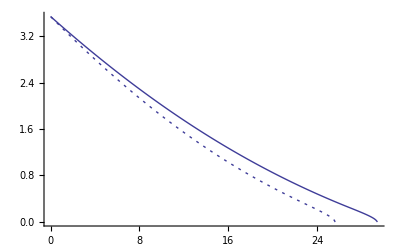

```mathematica
Show[grExLP,grExBPS]
```

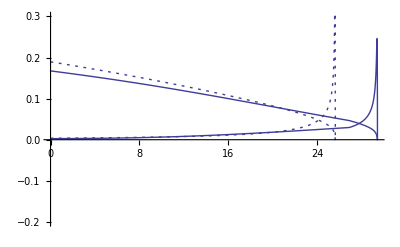

```mathematica
Show[grdEdxxeLP,grdEdxxiLP,grdEdxxeBPS,
grdEdxxiBPS,PlotRange->{ym,yM}]
```

```mathematica
NN=500;
xmin=0;
xmax=xRLPmax;
dx=(xmax-xmin)/NN;
data=Table[{x,dEdxxLP[x],dEdxxeLP[x],dEdxxiLP[x],ExLP[x]},{x,xmin,xmax,dx}]

(* Export["LPvsBPS.dEdxxExLP.aDT300127.dat",data,"Table",ConversionOptions-> {"FormatType"-> FortranForm}];
*)
```

```mathematica
NN=500;
xmin=0;
xmax=xRBPSmax;
dx=(xmax-xmin)/NN;
data=Table[{x,dEdxxBPS[x],dEdxxeBPS[x],dEdxxiBPS[x],ExBPS[x]},{x,xmin,xmax,dx}]

(*
Export["LPvsBPS.dEdxxExBPS.aDT300127.dat",data,"Table",ConversionOptions-> {"FormatType"-> FortranForm}];
*)
```